## Main

### Equations

#### Defintions

```mathematica
Clear[b,j,k,e,xp,xm,θp,θm];
es={
e-b Cos[xp] Sin[xm],
-b Sin[xp] Cos[xm]-j/2 Sin[2 xm]Cos[2 θm],
e-b Cos[θp] Sin[θm],
-b Sin[θp] Cos[θm]-k/2 Sin[2 θm]Cos[2xm]
}/.b->1;
TableForm[es]
```

e-Cos[xp] Sin[xm]
-1/2 j Cos[2 θm] Sin[2 xm]-Cos[xm] Sin[xp]
e-Cos[θp] Sin[θm]
-1/2 k Cos[2 xm] Sin[2 θm]-Cos[θm] Sin[θp]

#### Prepare

```mathematica
tempSub=Solve[es[[{1,3}]]=={0,0},{xm,θm}]/.C[1]->0/.C[2]->0;
TableForm[tempSub]
```

xm→π-ArcSin[e Sec[xp]] | θm→π-ArcSin[e Sec[θp]]
xm→π-ArcSin[e Sec[xp]] | θm→ArcSin[e Sec[θp]]
xm→ArcSin[e Sec[xp]] | θm→π-ArcSin[e Sec[θp]]
xm→ArcSin[e Sec[xp]] | θm→ArcSin[e Sec[θp]]

```mathematica
etemp=(es[[{2,4}]]//TrigExpand)/.tempSub[[4]]//FullSimplify;
TableForm[etemp]
```

√(1-e^2 Sec[xp]^2) (e j Sec[xp] (-1+2 e^2 Sec[θp]^2)-Sin[xp])
√(1-e^2 Sec[θp]^2) (e k (-1+2 e^2 Sec[xp]^2) Sec[θp]-Sin[θp])

#### Order parameter definition

```mathematica
e3={xp==1/2(x1+x2),xm==1/2(x1-x2),θp==1/2(θ1+θ2),θm==1/2(θ1-θ2)};
sub3=Solve[e3,{x1,x2,θ1,θ2}];
Wp=1/2(Exp[ⅈ(x1+θ1)]+Exp[ⅈ(x2+θ2)]);
Wm=1/2(Exp[ⅈ(x1-θ1)]+Exp[ⅈ(x2-θ2)]);
{Wp,Wm}=({Wp,Wm}/.sub3[[1]])//ExpToTrig//FullSimplify;
Wm=ExpToTrig[Wm]//Simplify;
TableForm[{Wp,Wm}]
```

Cos[xm+θm] (Cos[xp+θp]+ⅈ Sin[xp+θp])
Cos[xm-θm] (Cos[xp-θp]+ⅈ Sin[xp-θp])

### Fixed point 1

#### FP

```mathematica
etemp=(es[[{2,4}]]//TrigExpand)/.tempSub[[4]]//FullSimplify;
etemp//TableForm
e11={etemp[[1,1]],etemp[[2,1]]}//FullSimplify;
TableForm[e11]
fp1=Solve[e11==0,{xp,θp}]//FullSimplify
Length[fp1]
```

√(1-e^2 Sec[xp]^2) (e j Sec[xp] (-1+2 e^2 Sec[θp]^2)-Sin[xp])
√(1-e^2 Sec[θp]^2) (e k (-1+2 e^2 Sec[xp]^2) Sec[θp]-Sin[θp])

√(1-e^2 Sec[xp]^2)
√(1-e^2 Sec[θp]^2)

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{xp→-ArcCos[-e],θp→-ArcCos[-e]},{xp→-ArcCos[-e],θp→ArcCos[-e]},{xp→-ArcCos[-e],θp→-ArcCos[e]},{xp→-ArcCos[-e],θp→ArcCos[e]},{xp→ArcCos[-e],θp→-ArcCos[-e]},{xp→ArcCos[-e],θp→ArcCos[-e]},{xp→ArcCos[-e],θp→-ArcCos[e]},{xp→ArcCos[-e],θp→ArcCos[e]},{xp→-ArcCos[e],θp→-ArcCos[-e]},{xp→-ArcCos[e],θp→ArcCos[-e]},{xp→-ArcCos[e],θp→-ArcCos[e]},{xp→-ArcCos[e],θp→ArcCos[e]},{xp→ArcCos[e],θp→-ArcCos[-e]},{xp→ArcCos[e],θp→ArcCos[-e]},{xp→ArcCos[e],θp→-ArcCos[e]},{xp→ArcCos[e],θp→ArcCos[e]}}

16

#### Eigenvalues

```mathematica
$Assumptions={};
ParallelTable[
J={D[es, xp],D[es, xm],D[es, θp],D[es, θm]}//FullSimplify;
J1=J/.tempSub[[4]]/.fp1[[i]]//FullSimplify;
λ=FullSimplify[Eigenvalues[J1]]/.j->-1;
fixedpoint=({xp,xm,θp,θm}/.tempSub[[4]]/.fp1[[i]]);
condFixedPointReal=fixedpoint∈Reals;
condLamStable=Re[λ[[1]]]<=0&&Re[λ[[2]]]<=0&&Re[λ[[3]]]<=0&&Re[λ[[4]]]<=0;
RegionPlot[condFixedPointReal&&condLamStable,{k,-6,6},{e,0,2},PlotLabel->"i = "<>ToString[i]],
{i,1,Length[fp1]}
]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
i=7;
J={D[es, xp],D[es, xm],D[es, θp],D[es, θm]}//FullSimplify;
J1=J/.tempSub[[4]]/.fp1[[i]]//FullSimplify;
λ=FullSimplify[Eigenvalues[J1]];
TableForm[λ]
```

-√(1-e^2)
-√(1-e^2)
-√(1-e^2)-j
-√(1-e^2)-k

```mathematica
Solve[λ[[3]]==0,e]//FullSimplify
```

{{e→-√(1-j^2)},{e→√(1-j^2)}}

```mathematica
Solve[λ[[4]]==0,e]//FullSimplify
```

{{e→-√(1-k^2)},{e→√(1-k^2)}}

```mathematica
λ
```

{-√(1-e^2),-√(1-e^2),-√(1-e^2)-j,-√(1-e^2)-k}

```mathematica
RegionPlot3D[Re[λ[[2]]]<0&&Re[λ[[3]]]<0&&Re[λ[[4]]]<0,{k,-5,5},{j,-5,5},{e,0,2},PlotTheme->"Monochrome",]
```

-Graphics3D-

```mathematica
Plot3D[√(1-k^2),{k,-3,3},{j,-3,3},RegionFunction->Function[{x,y,z},-√(1-z^2)-y],AxesLabel->{"K","J","E"},LabelStyle->15]
```

-Graphics3D-

#### Order parameter

```mathematica
i=6;
Wp1=(Wp/.tempSub[[4]]//TrigExpand//FullSimplify)/.fp1[[i]]//TrigExpand//FullSimplify;
Wm1=(Wm/.tempSub[[4]]//TrigExpand//FullSimplify)/.fp1[[i]]//TrigExpand//FullSimplify;
TableForm[{Wp1,Wm1}]
```

1-2 e^2+2 ⅈ e √(1-e^2)
1

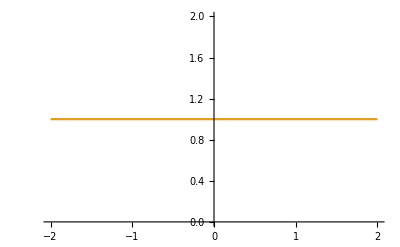

```mathematica
Plot[{Abs[Wp1],Abs[Wm1]},{k,-2,2}]
```

```mathematica
$Assumptions={};
ParallelTable[
Wp1=(Wp/.tempSub[[4]]//TrigExpand//FullSimplify)/.fp1[[i]]//TrigExpand//FullSimplify;
Wm1=(Wm/.tempSub[[4]]//TrigExpand//FullSimplify)/.fp1[[i]]//TrigExpand//FullSimplify;
ContourPlot[{S==Abs[Wp1]/.e->0.1,S==Abs[Wm1]/.e->0.1},{k,-5,5},{S,0,1},PlotLabel->"i = "<>ToString[i],PlotLegends->{"S_+","S_-"},LabelStyle->15],
{i,1,Length[fp1]}
]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

### Fixed point 2

#### FP

```mathematica
etemp=(es[[{2,4}]]//TrigExpand)/.tempSub[[4]]//FullSimplify;
etemp//TableForm
e3={etemp[[1,1]],etemp[[2,2]]}//FullSimplify;
TableForm[e3]
fp2=Solve[e3==0,{xp,θp}]//FullSimplify
Length[fp2]
```

√(1-e^2 Sec[xp]^2) (e j Sec[xp] (-1+2 e^2 Sec[θp]^2)-Sin[xp])
√(1-e^2 Sec[θp]^2) (e k (-1+2 e^2 Sec[xp]^2) Sec[θp]-Sin[θp])

√(1-e^2 Sec[xp]^2)
e k (-1+2 e^2 Sec[xp]^2) Sec[θp]-Sin[θp]

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{xp→-ArcCos[-e],θp→-ArcSec[-(√2)/(√(1-√(1-4 e^2 k^2)))]},{xp→-ArcCos[-e],θp→ArcSec[-(√2)/(√(1-√(1-4 e^2 k^2)))]},{xp→-ArcCos[-e],θp→-ArcSec[(√2)/(√(1-√(1-4 e^2 k^2)))]},{xp→-ArcCos[-e],θp→ArcSec[(√2)/(√(1-√(1-4 e^2 k^2)))]},{xp→-ArcCos[-e],θp→-ArcSec[(√2)/(√(1+√(1-4 e^2 k^2)))]},{xp→-ArcCos[-e],θp→ArcSec[(√2)/(√(1+√(1-4 e^2 k^2)))]},{xp→-ArcCos[-e],θp→-ArcSec[-(√2)/(√(1+√(1-4 e^2 k^2)))]},{xp→-ArcCos[-e],θp→ArcSec[-(√2)/(√(1+√(1-4 e^2 k^2)))]},{xp→ArcCos[-e],θp→-ArcSec[-(√2)/(√(1-√(1-4 e^2 k^2)))]},{xp→ArcCos[-e],θp→ArcSec[-(√2)/(√(1-√(1-4 e^2 k^2)))]},{xp→ArcCos[-e],θp→-ArcSec[(√2)/(√(1-√(1-4 e^2 k^2)))]},{xp→ArcCos[-e],θp→ArcSec[(√2)/(√(1-√(1-4 e^2 k^2)))]},{xp→ArcCos[-e],θp→-ArcSec[(√2)/(√(1+√(1-4 e^2 k^2)))]},{xp→ArcCos[-e],θp→ArcSec[(√2)/(√(1+√(1-4 e^2 k^2)))]},{xp→ArcCos[-e],θp→-ArcSec[-(√2)/(√(1+√(1-4 e^2 k^2)))]},{xp→ArcCos[-e],θp→ArcSec[-(√2)/(√(1+√(1-4 e^2 k^2)))]},{xp→-ArcCos[e],θp→-ArcSec[-(√2)/(√(1-√(1-4 e^2 k^2)))]},{xp→-ArcCos[e],θp→ArcSec[-(√2)/(√(1-√(1-4 e^2 k^2)))]},{xp→-ArcCos[e],θp→-ArcSec[(√2)/(√(1-√(1-4 e^2 k^2)))]},{xp→-ArcCos[e],θp→ArcSec[(√2)/(√(1-√(1-4 e^2 k^2)))]},{xp→-ArcCos[e],θp→-ArcSec[(√2)/(√(1+√(1-4 e^2 k^2)))]},{xp→-ArcCos[e],θp→ArcSec[(√2)/(√(1+√(1-4 e^2 k^2)))]},{xp→-ArcCos[e],θp→-ArcSec[-(√2)/(√(1+√(1-4 e^2 k^2)))]},{xp→-ArcCos[e],θp→ArcSec[-(√2)/(√(1+√(1-4 e^2 k^2)))]},{xp→ArcCos[e],θp→-ArcSec[-(√2)/(√(1-√(1-4 e^2 k^2)))]},{xp→ArcCos[e],θp→ArcSec[-(√2)/(√(1-√(1-4 e^2 k^2)))]},{xp→ArcCos[e],θp→-ArcSec[(√2)/(√(1-√(1-4 e^2 k^2)))]},{xp→ArcCos[e],θp→ArcSec[(√2)/(√(1-√(1-4 e^2 k^2)))]},{xp→ArcCos[e],θp→-ArcSec[(√2)/(√(1+√(1-4 e^2 k^2)))]},{xp→ArcCos[e],θp→ArcSec[(√2)/(√(1+√(1-4 e^2 k^2)))]},{xp→ArcCos[e],θp→-ArcSec[-(√2)/(√(1+√(1-4 e^2 k^2)))]},{xp→ArcCos[e],θp→ArcSec[-(√2)/(√(1+√(1-4 e^2 k^2)))]}}

32

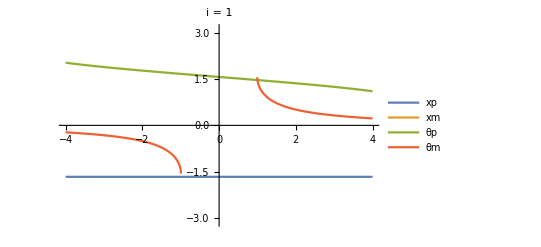
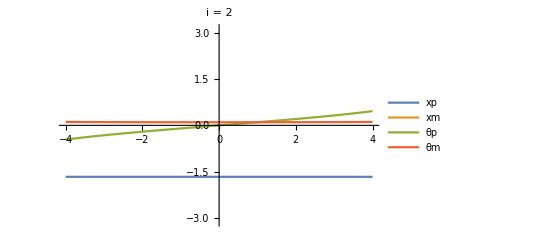
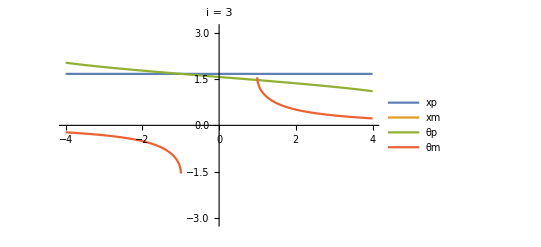
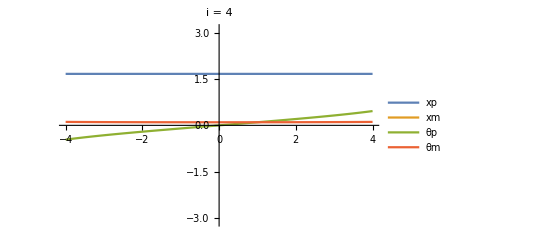
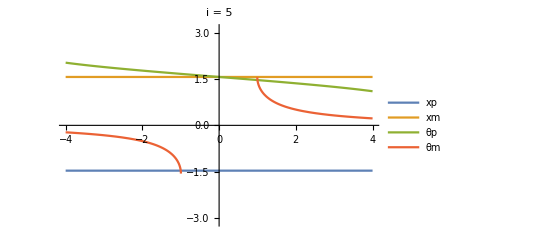
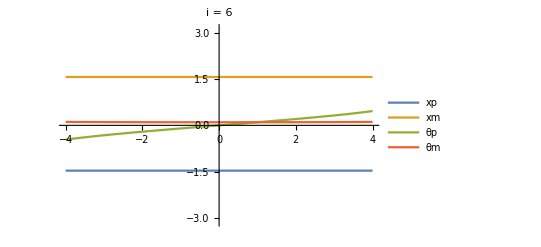
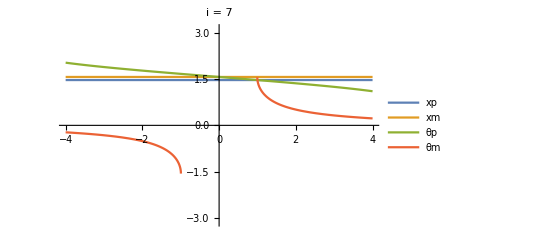
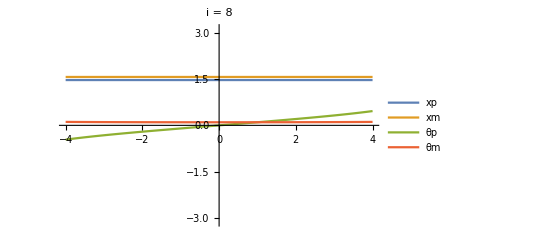

```mathematica
ParallelTable[
Plot[{xp,xm,θp,θm}/.tempSub[[4]]/.fp2[[i]]/.e->0.1/.C[1]->0/.C[2]->0//Evaluate,{k,-4,4},PlotRange->{{-4,4},{-π,π}},PlotLegends->{"xp", "xm", "θp", "θm"},LabelStyle->15,PlotLabel->"i = "<>ToString[i]],
{i,1,Length[fp2]}]
```

#### Eigenvalues

```mathematica
$Assumptions={};
ParallelTable[
J={D[es, xp],D[es, xm],D[es, θp],D[es, θm]}//FullSimplify;
J1=J/.tempSub[[4]]/.fp2[[i]]/.C[1]->0/.C[2]->0//FullSimplify;
λ=FullSimplify[Eigenvalues[J1]];
fixedpoint=({xp,xm,θp,θm}/.tempSub[[4]]/.fp2[[i]]);
condFixedPointReal=fixedpoint∈Reals;
condLamStable=Re[λ[[1]]]<=0&&Re[λ[[2]]]<=0&&Re[λ[[3]]]<=0&&Re[λ[[4]]]<=0;
RegionPlot[condFixedPointReal&&condLamStable,{k,-6,6},{e,0,1.2},PlotLabel->"i = "<>ToString[i]],
{i,1,Length[fp2]}
]
```

$Aborted

```mathematica
λ
```

{0.172056+1.78961 ⅈ,0.172056-1.78961 ⅈ,0.886131+0. ⅈ,-0.563577+0. ⅈ}

```mathematica
is={10,11,18,19}
```

```mathematica
i=10;
J={D[es, xp],D[es, xm],D[es, θp],D[es, θm]}//FullSimplify;
J1=J/.tempSub[[4]]/.fp2[[i]]//FullSimplify;
λ=FullSimplify[Eigenvalues[J1]];
TableForm[λ]
```

-√(1-e^2)
-√(1-e^2)+(j (-1+k^2-√(1-4 e^2 k^2)))/k^2
-(-2 e k (-1+√(1-4 e^2 k^2)) √(1+√(1-4 e^2 k^2))+k^2 √(1-√(1-4 e^2 k^2)) (-1+4 e^2+√(1-4 e^2 k^2))-2 √(k^2 (8 e^4 k^2 (2+2 k^2-√(1-4 e^2 k^2))-(4+k^2) (-1+√(1-4 e^2 k^2))+e^2 (k^4 (-3+√(1-4 e^2 k^2))+4 (-1+√(1-4 e^2 k^2))+4 k^2 (-5+3 √(1-4 e^2 k^2))))))/(2 k (1-√(1-4 e^2 k^2))^(3/2))
-(-2 e k (-1+√(1-4 e^2 k^2)) √(1+√(1-4 e^2 k^2))+k^2 √(1-√(1-4 e^2 k^2)) (-1+4 e^2+√(1-4 e^2 k^2))+2 √(k^2 (8 e^4 k^2 (2+2 k^2-√(1-4 e^2 k^2))-(4+k^2) (-1+√(1-4 e^2 k^2))+e^2 (k^4 (-3+√(1-4 e^2 k^2))+4 (-1+√(1-4 e^2 k^2))+4 k^2 (-5+3 √(1-4 e^2 k^2))))))/(2 k (1-√(1-4 e^2 k^2))^(3/2))

```mathematica
ContourPlot3D[-√(1-e^2)+(j (-1+k^2-√(1-4 e^2 k^2)))/k^2==0,{j,-3,3},{k,-3,3},{e,0,2}]
```

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

-Graphics3D-

```mathematica
esol=Solve[λ[[2]]==0,e]//FullSimplify
```

{{e→-√((k^4-4 j^4 (-2+k^2)-2 √(j^4 (-1+k^2)^2 (1+8 j^2+4 (-1+j^2) k^2))-j^2 (2+2 k^2+k^4))/((-4 j^2+k^2)^2))},{e→√((k^4-4 j^4 (-2+k^2)-2 √(j^4 (-1+k^2)^2 (1+8 j^2+4 (-1+j^2) k^2))-j^2 (2+2 k^2+k^4))/((-4 j^2+k^2)^2))},{e→-√((k^4-4 j^4 (-2+k^2)+2 √(j^4 (-1+k^2)^2 (1+8 j^2+4 (-1+j^2) k^2))-j^2 (2+2 k^2+k^4))/((-4 j^2+k^2)^2))},{e→√((k^4-4 j^4 (-2+k^2)+2 √(j^4 (-1+k^2)^2 (1+8 j^2+4 (-1+j^2) k^2))-j^2 (2+2 k^2+k^4))/((-4 j^2+k^2)^2))}}

```mathematica
Plot3D[√((k^4-4 j^4 (-2+k^2)-2 √(j^4 (-1+k^2)^2 (1+8 j^2+4 (-1+j^2) k^2))-j^2 (2+2 k^2+k^4))/((-4 j^2+k^2)^2))]
```

```mathematica
Solve[λ[[2]]==0,e]
```

{{e→-√(1-k^2)},{e→√(1-k^2)},{e→-(√(-4+5 k^2-k^4))/(3 k)},{e→(√(-4+5 k^2-k^4))/(3 k)}}

```mathematica
Solve[λ[[3]]==0,e]
```

$Aborted

```mathematica
FullSimplify[(√((-3-4 k^2+3 √(1+8 k^2))/k^2))/(2 √2),Assumptions->k>0]
```

(√(-3-4 k^2+3 √(1+8 k^2)))/(2 √2 k)

```mathematica
FullSimplify[k-(2 e √(1+√(1-4 e^2 k^2)))/(√(1-√(1-4 e^2 k^2)))-(1+√(1-4 e^2 k^2)+(√(k^2 (4-4 √(1-4 e^2 k^2)+8 e^2 √(1-4 e^2 k^2)-k^2 (-1+16 e^2+√(1-4 e^2 k^2)))))/(√(1-√(1-4 e^2 k^2))))/k]
```

```mathematica
k-(2 e √(1+√(1-4 e^2 k^2)))/(√(1-√(1-4 e^2 k^2)))-(1+√(1-4 e^2 k^2)+(√(k^2 (4-4 √(1-4 e^2 k^2)+8 e^2 √(1-4 e^2 k^2)-k^2 (-1+16 e^2+√(1-4 e^2 k^2)))))/(√(1-√(1-4 e^2 k^2))))/k
```

```mathematica
temp=FullSimplify[Numerator[Together[λ[[3]]]]]
```

-√(1-√(1-4 e^2 k^2))+k^2 √(1-√(1-4 e^2 k^2))-√(1-4 e^2 k^2) √(1-√(1-4 e^2 k^2))-2 e k √(1+√(1-4 e^2 k^2))-√(k^2 (4-4 √(1-4 e^2 k^2)+8 e^2 √(1-4 e^2 k^2)-k^2 (-1+16 e^2+√(1-4 e^2 k^2))))

```mathematica
removeSqRoot[eqn_,term_]:=Block[{eqn1,Xsol,X},
eqn1=eqn/.term->X;
Xsol=(X/.Solve[eqn1==0,X])[[1]];
Return[Together[Xsol^2-term^2]//Numerator//FullSimplify]
]
```

```mathematica
temp1=removeSqRoot[temp,√(1-√(1-4 e^2 k^2))]
```

4 k (-2 e^2 k^3+k (1-√(1-4 e^2 k^2)+2 e^2 √(1-4 e^2 k^2))+e √(1+√(1-4 e^2 k^2)) √(k^2 (4-4 √(1-4 e^2 k^2)+8 e^2 √(1-4 e^2 k^2)-k^2 (-1+16 e^2+√(1-4 e^2 k^2)))))

```mathematica
temp2=removeSqRoot[temp1,√(k^2 (4-4 √(1-4 e^2 k^2)+8 e^2 √(1-4 e^2 k^2)-k^2 (-1+16 e^2+√(1-4 e^2 k^2))))]
```

2 k^2 (1+8 e^6 k^2-√(1-4 e^2 k^2)+2 e^2 (-1+√(1-4 e^2 k^2)+k^2 (-2+√(1-4 e^2 k^2)))+e^4 (-2-4 √(1-4 e^2 k^2)+4 k^2 (2+√(1-4 e^2 k^2))))

```mathematica
temp3=removeSqRoot[temp2,√(1-4 e^2 k^2)]
```

4 e^4 (-1+2 e k) (1+2 e k) (-1+e^2+k^2) (3 (-1+e^2)+(k+2 e^2 k)^2)

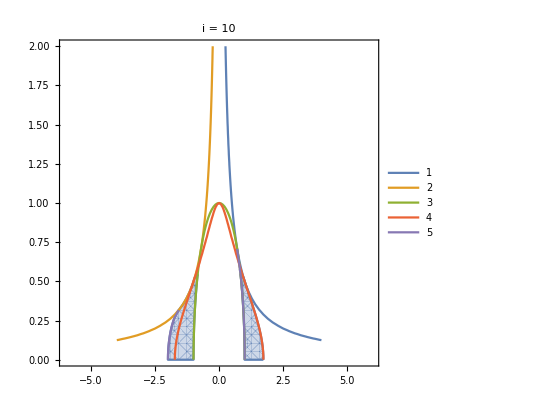

```mathematica
i=10;
J={D[es, xp],D[es, xm],D[es, θp],D[es, θm]}//FullSimplify;
J1=J/.tempSub[[4]]/.fp2[[i]]//FullSimplify;
λ=FullSimplify[Eigenvalues[J1]];
fixedpoint=({xp,xm,θp,θm}/.tempSub[[4]]/.fp2[[i]]);
condFixedPointReal=fixedpoint∈Reals;
condLamStable=Re[λ[[1]]]<=0&&Re[λ[[2]]]<=0&&Re[λ[[3]]]<=0&&Re[λ[[4]]]<=0;
p1=RegionPlot[condFixedPointReal&&condLamStable,{k,-6,6},{e,0,2},PlotLabel->"i = "<>ToString[i]];

p2=ContourPlot[{
-1+2 e k==0,
1+2 e k==0,
-1+e^2+k^2==0,
3 (-1+e^2)+(k+2 e^2 k)^2==0,
(1-k (√(1-e^2)+k)+√(1-4 e^2 k^2))/k==0
},{k,-4,4},{e,0,2},FrameLabel->{"K","E"},PlotLegends->Table[i,{i,1,5}]];

Show[{p1,p2}]
```

Power::infy: Infinite expression 1/(√0.) encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

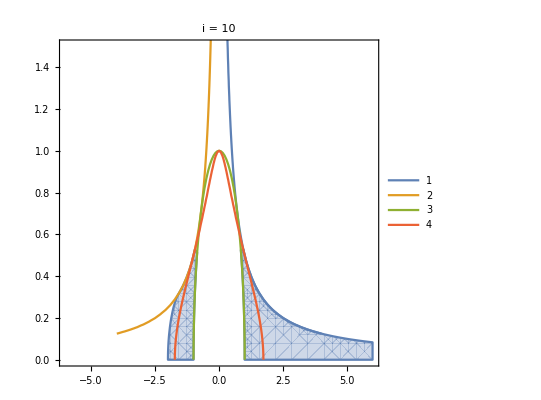

```mathematica
i=10;
J={D[es, xp],D[es, xm],D[es, θp],D[es, θm]}//FullSimplify;
J1=J/.tempSub[[4]]/.fp2[[i]]//FullSimplify;
λ=FullSimplify[Eigenvalues[J1]];
fixedpoint=({xp,xm,θp,θm}/.tempSub[[4]]/.fp2[[i]]);
condFixedPointReal=fixedpoint∈Reals;
condLamStable=Re[λ[[1]]]<=0&&Re[λ[[2]]]≤0;
p1=RegionPlot[condFixedPointReal&&condLamStable,{k,-6,6},{e,0,1.5},PlotLabel->"i = "<>ToString[i]];

p2=ContourPlot[{
-1+2 e k==0,
1+2 e k==0,
-1+e^2+k^2==0,
3 (-1+e^2)+(k+2 e^2 k)^2==0
},{k,-4,4},{e,0,2},FrameLabel->{"K","E"},PlotLegends->Table[i,{i,1,4}]];

Show[{p1,p2}]
```

```mathematica
Solve[3 (-1+e^2)+(k+2 e^2 k)^2==0,e]
```

{{e→-(√(-4-3/k^2-(3 √(1+8 k^2))/k^2))/(2 √2)},{e→(√(-4-3/k^2-(3 √(1+8 k^2))/k^2))/(2 √2)},{e→-(√(-4-3/k^2+(3 √(1+8 k^2))/k^2))/(2 √2)},{e→(√(-4-3/k^2+(3 √(1+8 k^2))/k^2))/(2 √2)}}

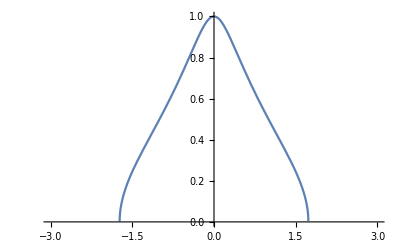

```mathematica
Plot[(√(-4-3/k^2+(3 √(1+8 k^2))/k^2))/(2 √2),{k,-3,3}]
```

Power::infy: Infinite expression 1/(√0.) encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

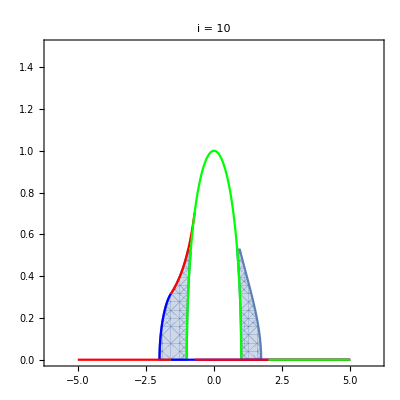

```mathematica
i=10;
k1=-√(5/2);
k2=-1/(√2);
J={D[es, xp],D[es, xm],D[es, θp],D[es, θm]}//FullSimplify;
J1=J/.tempSub[[4]]/.fp2[[i]]//FullSimplify;
λ=FullSimplify[Eigenvalues[J1]];
fixedpoint=({xp,xm,θp,θm}/.tempSub[[4]]/.fp2[[i]]);
condFixedPointReal=fixedpoint∈Reals;
condLamStable=Re[λ[[1]]]<=0&&Re[λ[[2]]]<=0&&Re[λ[[3]]]<=0&&Re[λ[[4]]]<=0;
p1=RegionPlot[condFixedPointReal&&condLamStable,{k,-6,6},{e,0,1.5},PlotLabel->"i = "<>ToString[i]];
p2=Plot[{Piecewise[{{-(√(-4+5 k^2-k^4))/(3 k), k≤k1}, {0, True}}],Piecewise[{{-1/(2k), k1≤k≤k3}, {0, True}}],Piecewise[{{√(1-k^2), k≤2}, {0, True}}]},{k,-5,5},PlotStyle->{Blue,Red,Green}];
Show[{p1,p2}]
```

Ok good.

#### Order parameter

```mathematica
i=1;
subc={C[1]->0,C[2]->0};
Wp2=(Wp/.tempSub[[4]]//TrigExpand//FullSimplify)/.fp2[[i]]/.subc//TrigExpand//FullSimplify;
Wm2=(Wm/.tempSub[[4]]//TrigExpand//FullSimplify)/.fp2[[i]]/.subc//TrigExpand//FullSimplify;
TableForm[{Wp2,Wm2}]
```

(2 ⅈ e (-ⅈ e+√(1-e^2)))/(-1+2 ⅈ e k+√(1-4 e^2 k^2))
(2 e ⅇ^(ⅈ ArcCos[e]))/(1+ⅈ ⅇ^(ⅈ ArcCos[2 e k]))

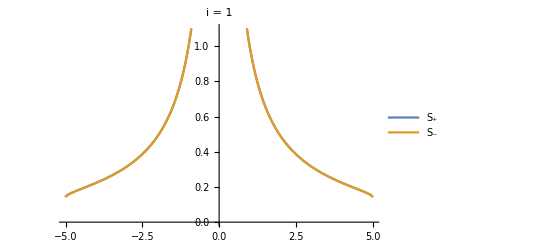
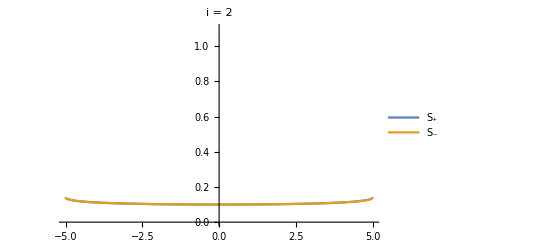
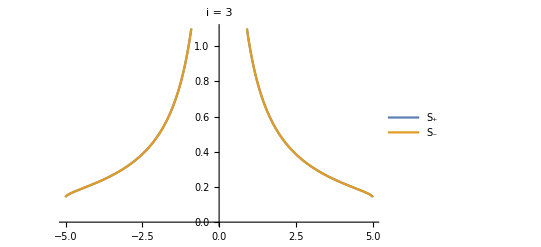
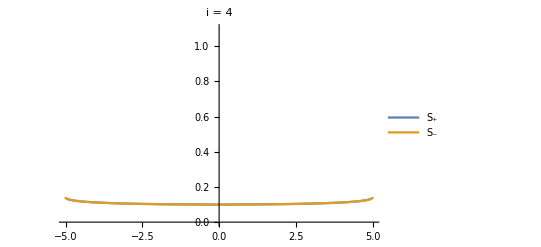
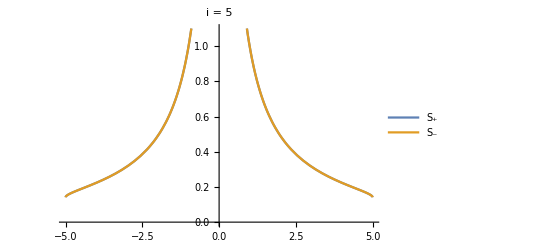
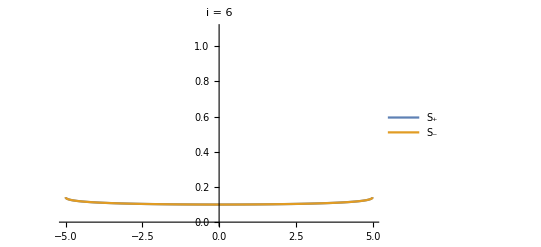
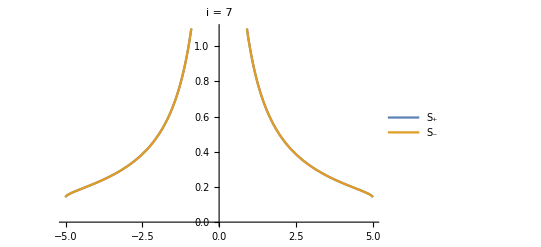
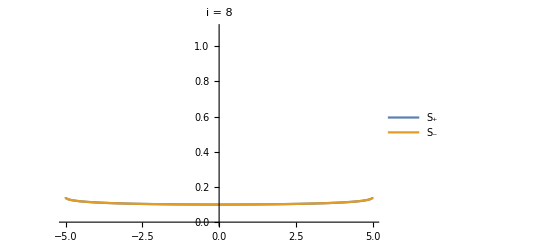

```mathematica
$Assumptions={};
ParallelTable[
Wp2=(Wp/.tempSub[[4]]/.fp2[[i]]/.subc//TrigExpand//FullSimplify)//TrigExpand//FullSimplify;
Wm2=(Wm/.tempSub[[4]]/.fp2[[i]]/.subc//TrigExpand//FullSimplify)//TrigExpand//FullSimplify;
kc=√(1-e^2)/.e->0.1;
Plot[{Abs[Wp2],Abs[Wm2]}/.e->0.1//Evaluate,{k,-5,5},PlotLabel->"i = "<>ToString[i],PlotLegends->{"S_+","S_-"},LabelStyle->15,PlotRange->{0,1.1}],
{i,1,Length[fp2]}
]
```

### Fixed point 3

#### FP

```mathematica
etemp=(es[[{2,4}]]//TrigExpand)/.tempSub[[4]]//FullSimplify;
etemp//TableForm
e3={etemp[[1,3]],etemp[[2,1]]}//FullSimplify;
TableForm[e3]
fp3=Solve[e3==0,{xp,θp}]//FullSimplify
Length[fp3]
```

√(1-e^2 Sec[xp]^2) (e j Sec[xp] (-1+2 e^2 Sec[θp]^2)-Sin[xp])
√(1-e^2 Sec[θp]^2) (e k (-1+2 e^2 Sec[xp]^2) Sec[θp]-Sin[θp])

Part::partw: Part 3 of √(1-e^2 Sec[xp]^2) (e j Sec[xp] (-1+2 e^2 Sec[θp]^2)-Sin[xp]) does not exist.

e j Sec[xp] (-1+2 e^2 Sec[θp]^2)-Sin[xp]
√(1-e^2 Sec[θp]^2)

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{xp→-ArcSec[-(√2)/(√(1-√(1-4 e^2 j^2)))],θp→-ArcCos[-e]},{xp→-ArcSec[-(√2)/(√(1-√(1-4 e^2 j^2)))],θp→ArcCos[-e]},{xp→-ArcSec[-(√2)/(√(1-√(1-4 e^2 j^2)))],θp→-ArcCos[e]},{xp→-ArcSec[-(√2)/(√(1-√(1-4 e^2 j^2)))],θp→ArcCos[e]},{xp→ArcSec[-(√2)/(√(1-√(1-4 e^2 j^2)))],θp→-ArcCos[-e]},{xp→ArcSec[-(√2)/(√(1-√(1-4 e^2 j^2)))],θp→ArcCos[-e]},{xp→ArcSec[-(√2)/(√(1-√(1-4 e^2 j^2)))],θp→-ArcCos[e]},{xp→ArcSec[-(√2)/(√(1-√(1-4 e^2 j^2)))],θp→ArcCos[e]},{xp→-ArcSec[(√2)/(√(1-√(1-4 e^2 j^2)))],θp→-ArcCos[-e]},{xp→-ArcSec[(√2)/(√(1-√(1-4 e^2 j^2)))],θp→ArcCos[-e]},{xp→-ArcSec[(√2)/(√(1-√(1-4 e^2 j^2)))],θp→-ArcCos[e]},{xp→-ArcSec[(√2)/(√(1-√(1-4 e^2 j^2)))],θp→ArcCos[e]},{xp→ArcSec[(√2)/(√(1-√(1-4 e^2 j^2)))],θp→-ArcCos[-e]},{xp→ArcSec[(√2)/(√(1-√(1-4 e^2 j^2)))],θp→ArcCos[-e]},{xp→ArcSec[(√2)/(√(1-√(1-4 e^2 j^2)))],θp→-ArcCos[e]},{xp→ArcSec[(√2)/(√(1-√(1-4 e^2 j^2)))],θp→ArcCos[e]},{xp→-ArcSec[(√2)/(√(1+√(1-4 e^2 j^2)))],θp→-ArcCos[-e]},{xp→-ArcSec[(√2)/(√(1+√(1-4 e^2 j^2)))],θp→ArcCos[-e]},{xp→-ArcSec[(√2)/(√(1+√(1-4 e^2 j^2)))],θp→-ArcCos[e]},{xp→-ArcSec[(√2)/(√(1+√(1-4 e^2 j^2)))],θp→ArcCos[e]},{xp→ArcSec[(√2)/(√(1+√(1-4 e^2 j^2)))],θp→-ArcCos[-e]},{xp→ArcSec[(√2)/(√(1+√(1-4 e^2 j^2)))],θp→ArcCos[-e]},{xp→ArcSec[(√2)/(√(1+√(1-4 e^2 j^2)))],θp→-ArcCos[e]},{xp→ArcSec[(√2)/(√(1+√(1-4 e^2 j^2)))],θp→ArcCos[e]},{xp→-ArcSec[-(√2)/(√(1+√(1-4 e^2 j^2)))],θp→-ArcCos[-e]},{xp→-ArcSec[-(√2)/(√(1+√(1-4 e^2 j^2)))],θp→ArcCos[-e]},{xp→-ArcSec[-(√2)/(√(1+√(1-4 e^2 j^2)))],θp→-ArcCos[e]},{xp→-ArcSec[-(√2)/(√(1+√(1-4 e^2 j^2)))],θp→ArcCos[e]},{xp→ArcSec[-(√2)/(√(1+√(1-4 e^2 j^2)))],θp→-ArcCos[-e]},{xp→ArcSec[-(√2)/(√(1+√(1-4 e^2 j^2)))],θp→ArcCos[-e]},{xp→ArcSec[-(√2)/(√(1+√(1-4 e^2 j^2)))],θp→-ArcCos[e]},{xp→ArcSec[-(√2)/(√(1+√(1-4 e^2 j^2)))],θp→ArcCos[e]}}

32

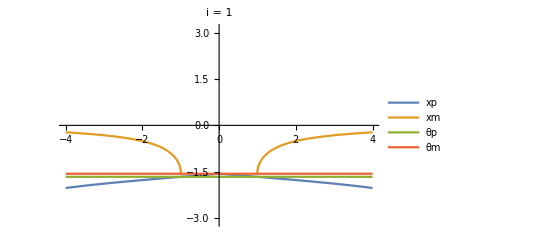
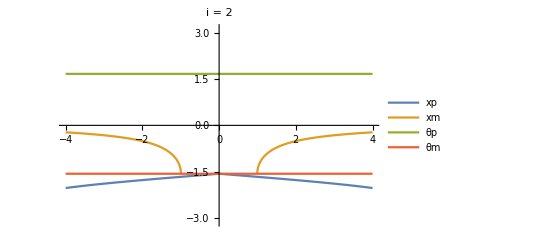
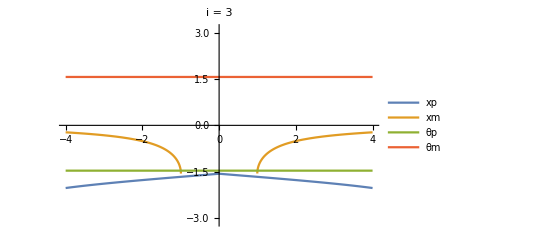
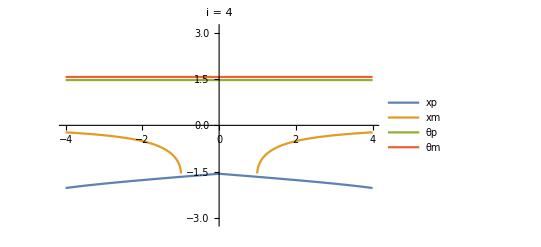
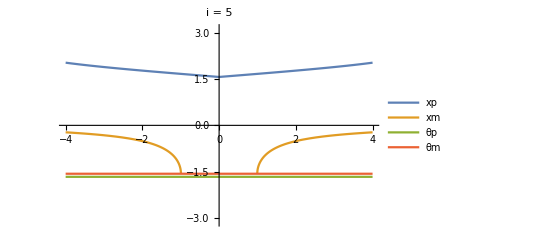
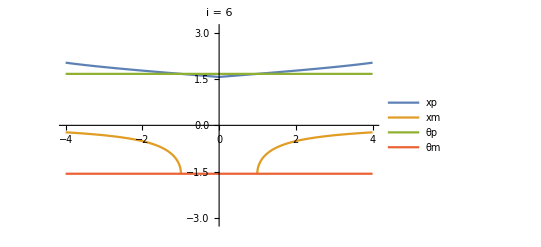
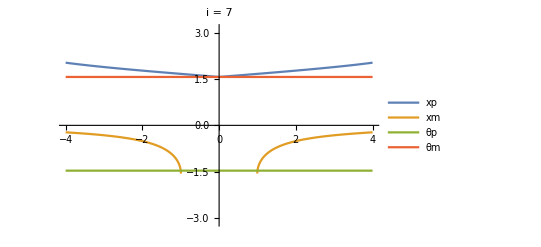
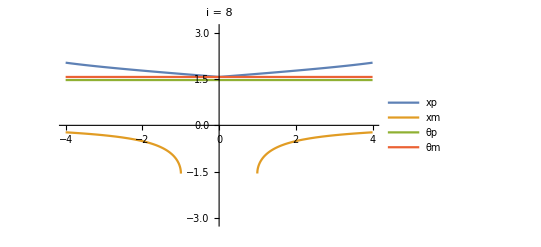

```mathematica
ParallelTable[
Plot[{xp,xm,θp,θm}/.tempSub[[4]]/.fp3[[i]]/.e->0.1//Evaluate,{k,-4,4},PlotRange->{{-4,4},{-π,π}},PlotLegends->{"xp", "xm", "θp", "θm"},LabelStyle->15,PlotLabel->"i = "<>ToString[i]],
{i,1,Length[fp3]}
]
```

#### Eigenvalues

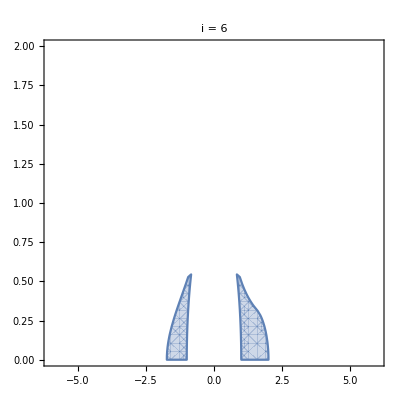
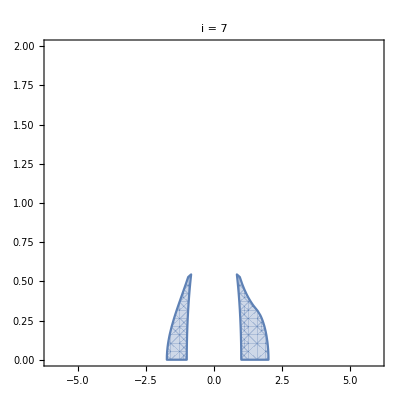
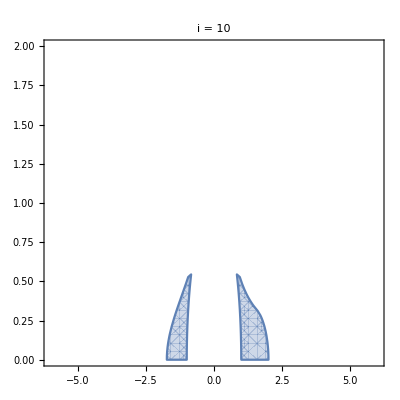
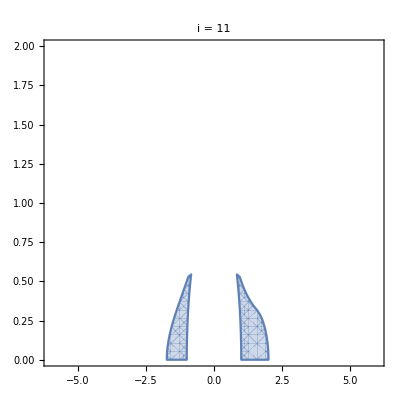
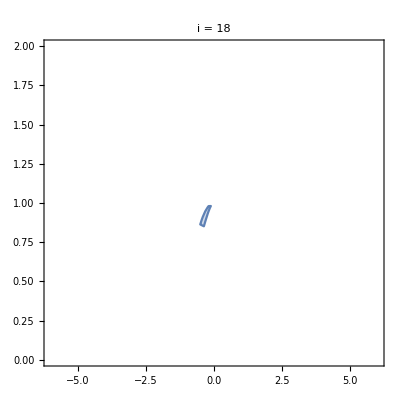
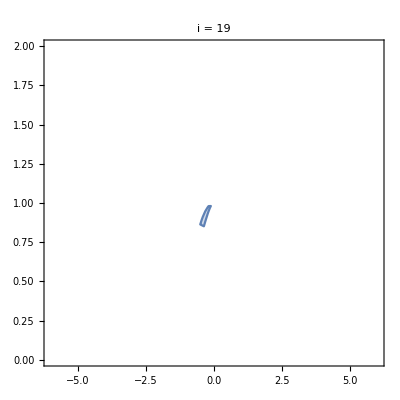
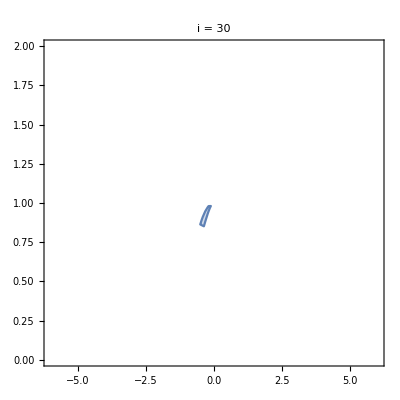
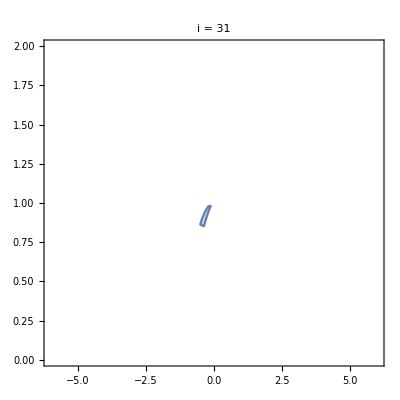
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
$Assumptions={};
ParallelTable[
J={D[es, xp],D[es, xm],D[es, θp],D[es, θm]}//FullSimplify;
J1=J/.tempSub[[4]]/.fp3[[i]]//FullSimplify;
λ=FullSimplify[Eigenvalues[J1]];
fixedpoint=({xp,xm,θp,θm}/.tempSub[[4]]/.fp3[[i]]);
condFixedPointReal=fixedpoint∈Reals;
condLamStable=Re[λ[[1]]]<=0&&Re[λ[[2]]]<=0&&Re[λ[[3]]]<=0&&Re[λ[[4]]]<=0;
RegionPlot[condFixedPointReal&&condLamStable,{k,-6,6},{e,0,2},PlotLabel->"i = "<>ToString[i]],
{i,1,Length[fp3]}
]
```

```mathematica
is={6,7}
```

```mathematica
i=6;
J={D[es, xp],D[es, xm],D[es, θp],D[es, θm]}//FullSimplify;
J1=J/.tempSub[[4]]/.fp2[[i]]//FullSimplify;
λ=FullSimplify[Eigenvalues[J1]];
TableForm[λ]
```

√(1-e^2)
(-1+k (√(1-e^2)+k)+√(1-4 e^2 k^2))/k
-(1-√(1-4 e^2 k^2)+(-k (2 e √(1-√(1-4 e^2 k^2))+k √(1+√(1-4 e^2 k^2)))+√(k^2 (4+4 √(1-4 e^2 k^2)-8 e^2 √(1-4 e^2 k^2)+k^2 (1-16 e^2+√(1-4 e^2 k^2)))))/(√(1+√(1-4 e^2 k^2))))/(2 k)
1/2 (k+(2 e √(1-√(1-4 e^2 k^2)))/(√(1+√(1-4 e^2 k^2)))+(-1+√(1-4 e^2 k^2)+(√(k^2 (4+4 √(1-4 e^2 k^2)-8 e^2 √(1-4 e^2 k^2)+k^2 (1-16 e^2+√(1-4 e^2 k^2)))))/(√(1+√(1-4 e^2 k^2))))/k)

```mathematica
Solve[-(1+(√(1-e^2)-k) k+√(1-4 e^2 k^2))/k==0,e]//FullSimplify
```

{{e→-√(1-k^2)},{e→√(1-k^2)},{e→-(√(-4+5 k^2-k^4))/(3 k)},{e→(√(-4+5 k^2-k^4))/(3 k)}}

```mathematica
λ[[2]]
```

-(1+(√(1-e^2)-k) k+√(1-4 e^2 k^2))/k

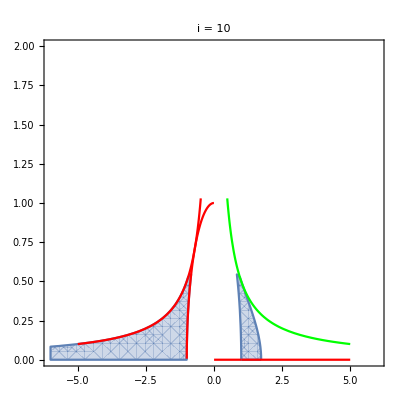

```mathematica
i=10;
J={D[es, xp],D[es, xm],D[es, θp],D[es, θm]}//FullSimplify;
J1=J/.tempSub[[4]]/.fp2[[i]]//FullSimplify;
λ=FullSimplify[Eigenvalues[J1]];
fixedpoint=({xp,xm,θp,θm}/.tempSub[[4]]/.fp2[[i]]);
condFixedPointReal=fixedpoint∈Reals;
condLamStable=Re[λ[[1]]]<=0&&Re[λ[[2]]]<=0&&Re[λ[[3]]]<=0&&Re[λ[[4]]]<=0;
p1=RegionPlot[condFixedPointReal&&condLamStable,{k,-6,6},{e,0,2},PlotLabel->"i = "<>ToString[i]];
p2=Plot[{-1/(2k),√(1-k^2)HeavisideTheta[-k],1/(2k)},{k,-5,5},PlotStyle->{Red,Red,Green}];
Show[{p1,p2}]
```

#### Order parameter

```mathematica
Wp3=(Wp/.tempSub[[4]]//TrigExpand//FullSimplify)/.fp3[[i]]//TrigExpand//FullSimplify;
Wm3=(Wm/.tempSub[[4]]//TrigExpand//FullSimplify)/.fp3[[i]]//TrigExpand//FullSimplify;
TableForm[{Wp2,Wm2}]
```

(2 ⅈ e (-ⅈ e+√(1-e^2)))/(-1+2 ⅈ e k+√(1-4 e^2 k^2))
(2 e ⅇ^(ⅈ ArcCos[e]))/(1+ⅈ ⅇ^(ⅈ ArcCos[2 e k]))

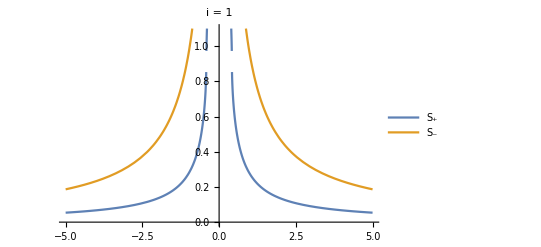
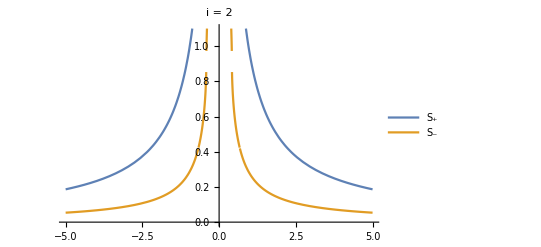
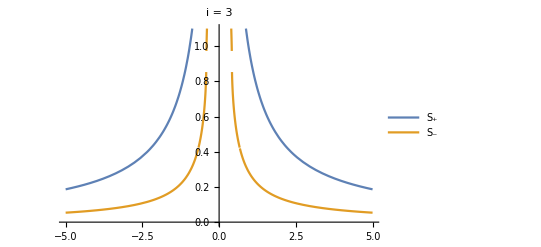
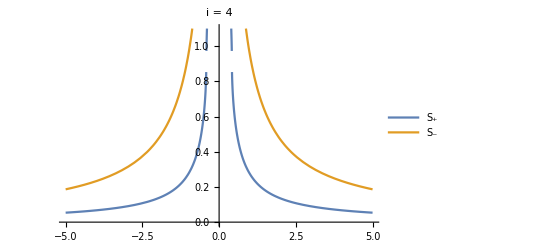
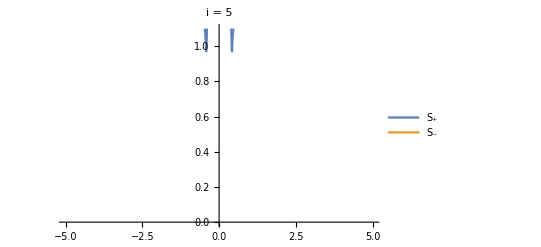
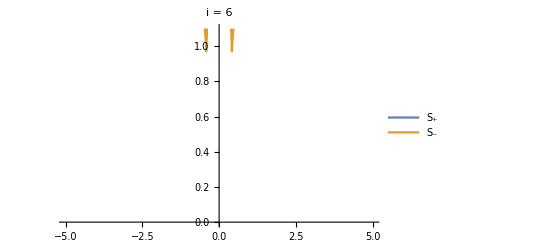
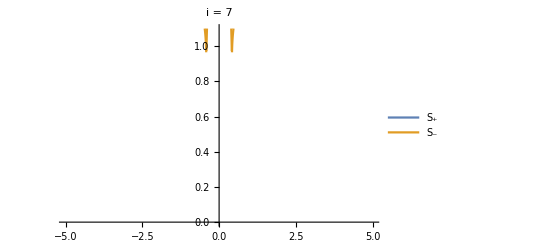
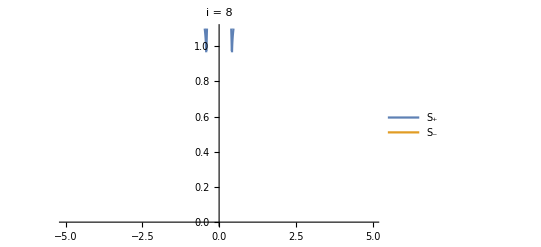

```mathematica
$Assumptions={};
ParallelTable[
Wp3=(Wp/.tempSub[[4]]/.subc//TrigExpand//FullSimplify)/.fp3[[i]]//TrigExpand//FullSimplify;
Wm3=(Wm/.tempSub[[4]]/.subc//TrigExpand//FullSimplify)/.fp3[[i]]//TrigExpand//FullSimplify;
Plot[{Abs[Wp3],Abs[Wm3]}/.e->e1//Evaluate,{j,-5,5},PlotLabel->"i = "<>ToString[i],PlotLegends->{"S_+","S_-"},LabelStyle->15,PlotRange->{0,1.1}],
{i,1,8}
]
```

```mathematica
$Assumptions={0≤e≤1,k∈Reals};
Abs[Wp3]//ComplexExpand//FullSimplify
```

Piecewise[{{(√2 e)/(√(1-√(1-4 e^2 k^2))), 4 e^2 k^2≤1}, {e/(√(e k (2 e k+√(-1+4 e^2 k^2)))), k<0&&4 e^2 k^2>1}, {√((e (2 e k+√(-1+4 e^2 k^2)))/k), True}}]

### Fixed point 4

#### FP

```mathematica
etemp=(es[[{2,4}]]//TrigExpand)/.tempSub[[4]]//FullSimplify;
etemp//TableForm
e4={etemp[[1,3]],etemp[[2,2]]}//FullSimplify;
TableForm[e4]
fp4=Solve[e4==0,{xp,θp}]//FullSimplify
Length[fp4]
```

-√(1-e^2 Sec[xp]^2) (e k Sec[xp] (-1+2 e^2 Sec[θp]^2)+Sin[xp])
√(1-e^2 Sec[θp]^2) (e k (-1+2 e^2 Sec[xp]^2) Sec[θp]-Sin[θp])

e k Sec[xp] (-1+2 e^2 Sec[θp]^2)+Sin[xp]
e k (-1+2 e^2 Sec[xp]^2) Sec[θp]-Sin[θp]

#### FP solve by hand

```mathematica
et1=e4[[1]]
```

e k Sec[xp] (-1+2 e^2 Sec[θp]^2)+Sin[xp]

```mathematica
Solve[et1==0,Sec[θp]]
```

{{Sec[θp]→-(√(e k-Cos[xp] Sin[xp]))/(√2 e^(3/2) √k)},{Sec[θp]→(√(e k-Cos[xp] Sin[xp]))/(√2 e^(3/2) √k)}}

I’ve worked out sin θ=1/(√(1-1/(sec^2 θ)))

```mathematica
sub={Sec[θp]->(√(e k-Cos[xp] Sin[xp]))/(√2 e^(3/2) √k),Sin[θp]->√(1-(1/((√(e k-Cos[xp] Sin[xp]))/(√2 e^(3/2) √k)))^2)};
```

```mathematica
et2=FullSimplify[Numerator[Together[e4[[2]]/.sub]]]
```

-√k √(2 e k-Sin[2 xp])+2 e^2 √k Sec[xp]^2 √(2 e k-Sin[2 xp])-2 √e √(1+(4 e^3 k)/(-2 e k+Sin[2 xp]))

```mathematica
removeSqRoot[eqn_,term_]:=Block[{eqn1,Xsol,X},
eqn1=eqn/.term->X;
Xsol=(X/.Solve[eqn1==0,X])[[1]];
Return[Together[Xsol^2-term^2]//Numerator]
]
```

```mathematica
et3=removeSqRoot[et2,√(1+(4 e^3 k)/(-2 e k+Sin[2 xp]))]//TrigExpand
```

-k/8+(e^2 k^3)/2-1/8 k Cos[xp]^2+1/2 e^2 k Cos[xp]^2-1/32 k Cos[xp]^4+1/8 k Sec[xp]^2-9/2 e^2 k Sec[xp]^2+8 e^4 k Sec[xp]^2+2 e^2 k^3 Sec[xp]^2-8 e^4 k^3 Sec[xp]^2+5/32 k Sec[xp]^4-4 e^2 k Sec[xp]^4+8 e^4 k Sec[xp]^4+3/2 e^2 k^3 Sec[xp]^4-8 e^4 k^3 Sec[xp]^4+16 e^6 k^3 Sec[xp]^4+3/2 e Cos[xp] Sin[xp]-3/2 e k^2 Cos[xp] Sin[xp]+15/8 k Sin[xp]^2-15/2 e^2 k Sin[xp]^2+7/8 k Cos[xp]^2 Sin[xp]^2-35/16 k Sin[xp]^4+4 e Tan[xp]-4 e k^2 Tan[xp]+16 e^3 k^2 Tan[xp]+5/2 e Sec[xp]^2 Tan[xp]-5/2 e k^2 Sec[xp]^2 Tan[xp]+16 e^3 k^2 Sec[xp]^2 Tan[xp]-32 e^5 k^2 Sec[xp]^2 Tan[xp]-5 e Sin[xp]^2 Tan[xp]+5 e k^2 Sin[xp]^2 Tan[xp]+3/4 k Tan[xp]^2-3 e^2 k^3 Tan[xp]^2-1/8 k Sec[xp]^2 Tan[xp]^2+9/2 e^2 k Sec[xp]^2 Tan[xp]^2-8 e^4 k Sec[xp]^2 Tan[xp]^2-2 e^2 k^3 Sec[xp]^2 Tan[xp]^2+8 e^4 k^3 Sec[xp]^2 Tan[xp]^2-15/8 k Sin[xp]^2 Tan[xp]^2+15/2 e^2 k Sin[xp]^2 Tan[xp]^2+7/8 k Sin[xp]^4 Tan[xp]^2-4 e Tan[xp]^3+4 e k^2 Tan[xp]^3-16 e^3 k^2 Tan[xp]^3+3/2 e Sin[xp]^2 Tan[xp]^3-3/2 e k^2 Sin[xp]^2 Tan[xp]^3-1/8 k Tan[xp]^4+1/2 e^2 k^3 Tan[xp]^4+1/8 k Sin[xp]^2 Tan[xp]^4-1/2 e^2 k Sin[xp]^2 Tan[xp]^4-1/32 k Sin[xp]^4 Tan[xp]^4

```mathematica
sub2={Cos[xp]->c,Sec[xp]->1/c,Tan[xp]->(√(1-c^2))/c,Sin[xp]->√(1-c^2)};
et4=FullSimplify[Numerator[et3/.sub2//Simplify]][[2]]//FullSimplify
```

c^8 k-8 c^3 √(1-c^2) e^3 k^2+8 c √(1-c^2) e^5 k^2-4 e^6 k^3-c^6 (k+4 e^2 k)-c^4 e^2 k (-6+k^2)+2 c^5 √(1-c^2) e (-1+k^2)+4 c^2 e^4 k (-1+k^2)

```mathematica
et5=removeSqRoot[et4,√(1-c^2)]//FullSimplify
```

(c^6 (-1+c^2)+e^2 (c^2-2 e^2)^2 k^2) (4 c^4 e^2+c^2 (c^6-8 e^4-c^4 (1+8 e^2)+4 c^2 (e^2+4 e^4)) k^2+e^2 (c^2-2 e^2)^2 k^4)

I think these are clean polynomials in c^2....

```mathematica
et6=et5/.c->√c1//FullSimplify
```

((-1+c1) c1^3+e^2 (c1-2 e^2)^2 k^2) (4 c1^2 e^2+c1 ((-1+c1) c1^2+4 (1-2 c1) c1 e^2+8 (-1+2 c1) e^4) k^2+e^2 (c1-2 e^2)^2 k^4)

```mathematica
Collect[et6[[1]],c1]
```

-c1^3+c1^4+c1^2 e^2 k^2-4 c1 e^4 k^2+4 e^6 k^2

```mathematica
Collect[et6[[2]],c1]
```

c1^4 k^2+4 e^6 k^4+c1^3 (-k^2-8 e^2 k^2)+c1^2 (4 e^2+4 e^2 k^2+16 e^4 k^2+e^2 k^4)+c1 (-8 e^4 k^2-4 e^4 k^4)

Yes, a cubic and a quartic in c1 = c^2. So they have known, but ugly, solutions. Nice!! In principle I’m done. Just gotta fold back

```mathematica
fp4sub=Solve[et5==0,c];
Length[fp4sub]
fp4sub
```

16

{{c→-√(1/4+2 e^2-(√(-16 e^2+k^2))/(4 k)-1/2 √(1/2 (-1-8 e^2)^2-e^2 k^2-(4 e^2+4 e^2 k^2+16 e^4 k^2+e^2 k^4)/k^2-(k (-(-1-8 e^2)^3+32 (2 e^4+e^4 k^2)+(4 (-1-8 e^2) (4 e^2+4 e^2 k^2+16 e^4 k^2+e^2 k^4))/k^2))/(2 √(-16 e^2+k^2))))},{c→√(1/4+2 e^2-(√(-16 e^2+k^2))/(4 k)-1/2 √(1/2 (-1-8 e^2)^2-e^2 k^2-(4 e^2+4 e^2 k^2+16 e^4 k^2+e^2 k^4)/k^2-(k (-(-1-8 e^2)^3+32 (2 e^4+e^4 k^2)+(4 (-1-8 e^2) (4 e^2+4 e^2 k^2+16 e^4 k^2+e^2 k^4))/k^2))/(2 √(-16 e^2+k^2))))},{c→-√(1/4+2 e^2-(√(-16 e^2+k^2))/(4 k)+1/2 √(1/2 (-1-8 e^2)^2-e^2 k^2-(4 e^2+4 e^2 k^2+16 e^4 k^2+e^2 k^4)/k^2-(k (-(-1-8 e^2)^3+32 (2 e^4+e^4 k^2)+(4 (-1-8 e^2) (4 e^2+4 e^2 k^2+16 e^4 k^2+e^2 k^4))/k^2))/(2 √(-16 e^2+k^2))))},{c→√(1/4+2 e^2-(√(-16 e^2+k^2))/(4 k)+1/2 √(1/2 (-1-8 e^2)^2-e^2 k^2-(4 e^2+4 e^2 k^2+16 e^4 k^2+e^2 k^4)/k^2-(k (-(-1-8 e^2)^3+32 (2 e^4+e^4 k^2)+(4 (-1-8 e^2) (4 e^2+4 e^2 k^2+16 e^4 k^2+e^2 k^4))/k^2))/(2 √(-16 e^2+k^2))))},{c→-√(1/4+2 e^2+(√(-16 e^2+k^2))/(4 k)-1/2 √(1/2 (-1-8 e^2)^2-e^2 k^2-(4 e^2+4 e^2 k^2+16 e^4 k^2+e^2 k^4)/k^2+(k (-(-1-8 e^2)^3+32 (2 e^4+e^4 k^2)+(4 (-1-8 e^2) (4 e^2+4 e^2 k^2+16 e^4 k^2+e^2 k^4))/k^2))/(2 √(-16 e^2+k^2))))},{c→√(1/4+2 e^2+(√(-16 e^2+k^2))/(4 k)-1/2 √(1/2 (-1-8 e^2)^2-e^2 k^2-(4 e^2+4 e^2 k^2+16 e^4 k^2+e^2 k^4)/k^2+(k (-(-1-8 e^2)^3+32 (2 e^4+e^4 k^2)+(4 (-1-8 e^2) (4 e^2+4 e^2 k^2+16 e^4 k^2+e^2 k^4))/k^2))/(2 √(-16 e^2+k^2))))},{c→-√(1/4+2 e^2+(√(-16 e^2+k^2))/(4 k)+1/2 √(1/2 (-1-8 e^2)^2-e^2 k^2-(4 e^2+4 e^2 k^2+16 e^4 k^2+e^2 k^4)/k^2+(k (-(-1-8 e^2)^3+32 (2 e^4+e^4 k^2)+(4 (-1-8 e^2) (4 e^2+4 e^2 k^2+16 e^4 k^2+e^2 k^4))/k^2))/(2 √(-16 e^2+k^2))))},{c→√(1/4+2 e^2+(√(-16 e^2+k^2))/(4 k)+1/2 √(1/2 (-1-8 e^2)^2-e^2 k^2-(4 e^2+4 e^2 k^2+16 e^4 k^2+e^2 k^4)/k^2+(k (-(-1-8 e^2)^3+32 (2 e^4+e^4 k^2)+(4 (-1-8 e^2) (4 e^2+4 e^2 k^2+16 e^4 k^2+e^2 k^4))/k^2))/(2 √(-16 e^2+k^2))))},{c→-√(1/4-1/2 √(1/4-(2 e^2 k^2)/3+(e^4 k^2 (-12+48 e^2+k^2))/(3 (54 e^6 k^2-18 e^6 k^4+72 e^8 k^4+e^6 k^6+6 √3 √(27 e^12 k^4-2 e^12 k^6-120 e^14 k^6+768 e^16 k^6-1024 e^18 k^6+8 e^14 k^8-16 e^16 k^8))^(1/3))+1/3 (54 e^6 k^2-18 e^6 k^4+72 e^8 k^4+e^6 k^6+6 √3 √(27 e^12 k^4-2 e^12 k^6-120 e^14 k^6+768 e^16 k^6-1024 e^18 k^6+8 e^14 k^8-16 e^16 k^8))^(1/3))-1/2 √(1/2-(4 e^2 k^2)/3-(e^4 k^2 (-12+48 e^2+k^2))/(3 (54 e^6 k^2-18 e^6 k^4+72 e^8 k^4+e^6 k^6+6 √3 √(27 e^12 k^4-2 e^12 k^6-120 e^14 k^6+768 e^16 k^6-1024 e^18 k^6+8 e^14 k^8-16 e^16 k^8))^(1/3))-1/3 (54 e^6 k^2-18 e^6 k^4+72 e^8 k^4+e^6 k^6+6 √3 √(27 e^12 k^4-2 e^12 k^6-120 e^14 k^6+768 e^16 k^6-1024 e^18 k^6+8 e^14 k^8-16 e^16 k^8))^(1/3)-(1-4 e^2 k^2+32 e^4 k^2)/(4 √(1/4-(2 e^2 k^2)/3+(e^4 k^2 (-12+48 e^2+k^2))/(3 (54 e^6 k^2-18 e^6 k^4+72 e^8 k^4+e^6 k^6+6 √3 √(27 e^12 k^4-2 e^12 k^6-120 e^14 k^6+768 e^16 k^6-1024 e^18 k^6+8 e^14 k^8-16 e^16 k^8))^(1/3))+1/3 (54 e^6 k^2-18 e^6 k^4+72 e^8 k^4+e^6 k^6+6 √3 √(27 e^12 k^4-2 e^12 k^6-120 e^14 k^6+768 e^16 k^6-1024 e^18 k^6+8 e^14 k^8-16 e^16 k^8))^(1/3)))))},{c→√(1/4-1/2 √(1/4-(2 e^2 k^2)/3+(e^4 k^2 (-12+48 e^2+k^2))/(3 (54 e^6 k^2-18 e^6 k^4+72 e^8 k^4+e^6 k^6+6 √3 √(27 e^12 k^4-2 e^12 k^6-120 e^14 k^6+768 e^16 k^6-1024 e^18 k^6+8 e^14 k^8-16 e^16 k^8))^(1/3))+1/3 (54 e^6 k^2-18 e^6 k^4+72 e^8 k^4+e^6 k^6+6 √3 √(27 e^12 k^4-2 e^12 k^6-120 e^14 k^6+768 e^16 k^6-1024 e^18 k^6+8 e^14 k^8-16 e^16 k^8))^(1/3))-1/2 √(1/2-(4 e^2 k^2)/3-(e^4 k^2 (-12+48 e^2+k^2))/(3 (54 e^6 k^2-18 e^6 k^4+72 e^8 k^4+e^6 k^6+6 √3 √(27 e^12 k^4-2 e^12 k^6-120 e^14 k^6+768 e^16 k^6-1024 e^18 k^6+8 e^14 k^8-16 e^16 k^8))^(1/3))-1/3 (54 e^6 k^2-18 e^6 k^4+72 e^8 k^4+e^6 k^6+6 √3 √(27 e^12 k^4-2 e^12 k^6-120 e^14 k^6+768 e^16 k^6-1024 e^18 k^6+8 e^14 k^8-16 e^16 k^8))^(1/3)-(1-4 e^2 k^2+32 e^4 k^2)/(4 √(1/4-(2 e^2 k^2)/3+(e^4 k^2 (-12+48 e^2+k^2))/(3 (54 e^6 k^2-18 e^6 k^4+72 e^8 k^4+e^6 k^6+6 √3 √(27 e^12 k^4-2 e^12 k^6-120 e^14 k^6+768 e^16 k^6-1024 e^18 k^6+8 e^14 k^8-16 e^16 k^8))^(1/3))+1/3 (54 e^6 k^2-18 e^6 k^4+72 e^8 k^4+e^6 k^6+6 √3 √(27 e^12 k^4-2 e^12 k^6-120 e^14 k^6+768 e^16 k^6-1024 e^18 k^6+8 e^14 k^8-16 e^16 k^8))^(1/3)))))},{c→-√(1/4-1/2 √(1/4-(2 e^2 k^2)/3+(e^4 k^2 (-12+48 e^2+k^2))/(3 (54 e^6 k^2-18 e^6 k^4+72 e^8 k^4+e^6 k^6+6 √3 √(27 e^12 k^4-2 e^12 k^6-120 e^14 k^6+768 e^16 k^6-1024 e^18 k^6+8 e^14 k^8-16 e^16 k^8))^(1/3))+1/3 (54 e^6 k^2-18 e^6 k^4+72 e^8 k^4+e^6 k^6+6 √3 √(27 e^12 k^4-2 e^12 k^6-120 e^14 k^6+768 e^16 k^6-1024 e^18 k^6+8 e^14 k^8-16 e^16 k^8))^(1/3))+1/2 √(1/2-(4 e^2 k^2)/3-(e^4 k^2 (-12+48 e^2+k^2))/(3 (54 e^6 k^2-18 e^6 k^4+72 e^8 k^4+e^6 k^6+6 √3 √(27 e^12 k^4-2 e^12 k^6-120 e^14 k^6+768 e^16 k^6-1024 e^18 k^6+8 e^14 k^8-16 e^16 k^8))^(1/3))-1/3 (54 e^6 k^2-18 e^6 k^4+72 e^8 k^4+e^6 k^6+6 √3 √(27 e^12 k^4-2 e^12 k^6-120 e^14 k^6+768 e^16 k^6-1024 e^18 k^6+8 e^14 k^8-16 e^16 k^8))^(1/3)-(1-4 e^2 k^2+32 e^4 k^2)/(4 √(1/4-(2 e^2 k^2)/3+(e^4 k^2 (-12+48 e^2+k^2))/(3 (54 e^6 k^2-18 e^6 k^4+72 e^8 k^4+e^6 k^6+6 √3 √(27 e^12 k^4-2 e^12 k^6-120 e^14 k^6+768 e^16 k^6-1024 e^18 k^6+8 e^14 k^8-16 e^16 k^8))^(1/3))+1/3 (54 e^6 k^2-18 e^6 k^4+72 e^8 k^4+e^6 k^6+6 √3 √(27 e^12 k^4-2 e^12 k^6-120 e^14 k^6+768 e^16 k^6-1024 e^18 k^6+8 e^14 k^8-16 e^16 k^8))^(1/3)))))},{c→√(1/4-1/2 √(1/4-(2 e^2 k^2)/3+(e^4 k^2 (-12+48 e^2+k^2))/(3 (54 e^6 k^2-18 e^6 k^4+72 e^8 k^4+e^6 k^6+6 √3 √(27 e^12 k^4-2 e^12 k^6-120 e^14 k^6+768 e^16 k^6-1024 e^18 k^6+8 e^14 k^8-16 e^16 k^8))^(1/3))+1/3 (54 e^6 k^2-18 e^6 k^4+72 e^8 k^4+e^6 k^6+6 √3 √(27 e^12 k^4-2 e^12 k^6-120 e^14 k^6+768 e^16 k^6-1024 e^18 k^6+8 e^14 k^8-16 e^16 k^8))^(1/3))+1/2 √(1/2-(4 e^2 k^2)/3-(e^4 k^2 (-12+48 e^2+k^2))/(3 (54 e^6 k^2-18 e^6 k^4+72 e^8 k^4+e^6 k^6+6 √3 √(27 e^12 k^4-2 e^12 k^6-120 e^14 k^6+768 e^16 k^6-1024 e^18 k^6+8 e^14 k^8-16 e^16 k^8))^(1/3))-1/3 (54 e^6 k^2-18 e^6 k^4+72 e^8 k^4+e^6 k^6+6 √3 √(27 e^12 k^4-2 e^12 k^6-120 e^14 k^6+768 e^16 k^6-1024 e^18 k^6+8 e^14 k^8-16 e^16 k^8))^(1/3)-(1-4 e^2 k^2+32 e^4 k^2)/(4 √(1/4-(2 e^2 k^2)/3+(e^4 k^2 (-12+48 e^2+k^2))/(3 (54 e^6 k^2-18 e^6 k^4+72 e^8 k^4+e^6 k^6+6 √3 √(27 e^12 k^4-2 e^12 k^6-120 e^14 k^6+768 e^16 k^6-1024 e^18 k^6+8 e^14 k^8-16 e^16 k^8))^(1/3))+1/3 (54 e^6 k^2-18 e^6 k^4+72 e^8 k^4+e^6 k^6+6 √3 √(27 e^12 k^4-2 e^12 k^6-120 e^14 k^6+768 e^16 k^6-1024 e^18 k^6+8 e^14 k^8-16 e^16 k^8))^(1/3)))))},{c→-√(1/4+1/2 √(1/4-(2 e^2 k^2)/3+(e^4 k^2 (-12+48 e^2+k^2))/(3 (54 e^6 k^2-18 e^6 k^4+72 e^8 k^4+e^6 k^6+6 √3 √(27 e^12 k^4-2 e^12 k^6-120 e^14 k^6+768 e^16 k^6-1024 e^18 k^6+8 e^14 k^8-16 e^16 k^8))^(1/3))+1/3 (54 e^6 k^2-18 e^6 k^4+72 e^8 k^4+e^6 k^6+6 √3 √(27 e^12 k^4-2 e^12 k^6-120 e^14 k^6+768 e^16 k^6-1024 e^18 k^6+8 e^14 k^8-16 e^16 k^8))^(1/3))-1/2 √(1/2-(4 e^2 k^2)/3-(e^4 k^2 (-12+48 e^2+k^2))/(3 (54 e^6 k^2-18 e^6 k^4+72 e^8 k^4+e^6 k^6+6 √3 √(27 e^12 k^4-2 e^12 k^6-120 e^14 k^6+768 e^16 k^6-1024 e^18 k^6+8 e^14 k^8-16 e^16 k^8))^(1/3))-1/3 (54 e^6 k^2-18 e^6 k^4+72 e^8 k^4+e^6 k^6+6 √3 √(27 e^12 k^4-2 e^12 k^6-120 e^14 k^6+768 e^16 k^6-1024 e^18 k^6+8 e^14 k^8-16 e^16 k^8))^(1/3)+(1-4 e^2 k^2+32 e^4 k^2)/(4 √(1/4-(2 e^2 k^2)/3+(e^4 k^2 (-12+48 e^2+k^2))/(3 (54 e^6 k^2-18 e^6 k^4+72 e^8 k^4+e^6 k^6+6 √3 √(27 e^12 k^4-2 e^12 k^6-120 e^14 k^6+768 e^16 k^6-1024 e^18 k^6+8 e^14 k^8-16 e^16 k^8))^(1/3))+1/3 (54 e^6 k^2-18 e^6 k^4+72 e^8 k^4+e^6 k^6+6 √3 √(27 e^12 k^4-2 e^12 k^6-120 e^14 k^6+768 e^16 k^6-1024 e^18 k^6+8 e^14 k^8-16 e^16 k^8))^(1/3)))))},{c→√(1/4+1/2 √(1/4-(2 e^2 k^2)/3+(e^4 k^2 (-12+48 e^2+k^2))/(3 (54 e^6 k^2-18 e^6 k^4+72 e^8 k^4+e^6 k^6+6 √3 √(27 e^12 k^4-2 e^12 k^6-120 e^14 k^6+768 e^16 k^6-1024 e^18 k^6+8 e^14 k^8-16 e^16 k^8))^(1/3))+1/3 (54 e^6 k^2-18 e^6 k^4+72 e^8 k^4+e^6 k^6+6 √3 √(27 e^12 k^4-2 e^12 k^6-120 e^14 k^6+768 e^16 k^6-1024 e^18 k^6+8 e^14 k^8-16 e^16 k^8))^(1/3))-1/2 √(1/2-(4 e^2 k^2)/3-(e^4 k^2 (-12+48 e^2+k^2))/(3 (54 e^6 k^2-18 e^6 k^4+72 e^8 k^4+e^6 k^6+6 √3 √(27 e^12 k^4-2 e^12 k^6-120 e^14 k^6+768 e^16 k^6-1024 e^18 k^6+8 e^14 k^8-16 e^16 k^8))^(1/3))-1/3 (54 e^6 k^2-18 e^6 k^4+72 e^8 k^4+e^6 k^6+6 √3 √(27 e^12 k^4-2 e^12 k^6-120 e^14 k^6+768 e^16 k^6-1024 e^18 k^6+8 e^14 k^8-16 e^16 k^8))^(1/3)+(1-4 e^2 k^2+32 e^4 k^2)/(4 √(1/4-(2 e^2 k^2)/3+(e^4 k^2 (-12+48 e^2+k^2))/(3 (54 e^6 k^2-18 e^6 k^4+72 e^8 k^4+e^6 k^6+6 √3 √(27 e^12 k^4-2 e^12 k^6-120 e^14 k^6+768 e^16 k^6-1024 e^18 k^6+8 e^14 k^8-16 e^16 k^8))^(1/3))+1/3 (54 e^6 k^2-18 e^6 k^4+72 e^8 k^4+e^6 k^6+6 √3 √(27 e^12 k^4-2 e^12 k^6-120 e^14 k^6+768 e^16 k^6-1024 e^18 k^6+8 e^14 k^8-16 e^16 k^8))^(1/3)))))},{c→-√(1/4+1/2 √(1/4-(2 e^2 k^2)/3+(e^4 k^2 (-12+48 e^2+k^2))/(3 (54 e^6 k^2-18 e^6 k^4+72 e^8 k^4+e^6 k^6+6 √3 √(27 e^12 k^4-2 e^12 k^6-120 e^14 k^6+768 e^16 k^6-1024 e^18 k^6+8 e^14 k^8-16 e^16 k^8))^(1/3))+1/3 (54 e^6 k^2-18 e^6 k^4+72 e^8 k^4+e^6 k^6+6 √3 √(27 e^12 k^4-2 e^12 k^6-120 e^14 k^6+768 e^16 k^6-1024 e^18 k^6+8 e^14 k^8-16 e^16 k^8))^(1/3))+1/2 √(1/2-(4 e^2 k^2)/3-(e^4 k^2 (-12+48 e^2+k^2))/(3 (54 e^6 k^2-18 e^6 k^4+72 e^8 k^4+e^6 k^6+6 √3 √(27 e^12 k^4-2 e^12 k^6-120 e^14 k^6+768 e^16 k^6-1024 e^18 k^6+8 e^14 k^8-16 e^16 k^8))^(1/3))-1/3 (54 e^6 k^2-18 e^6 k^4+72 e^8 k^4+e^6 k^6+6 √3 √(27 e^12 k^4-2 e^12 k^6-120 e^14 k^6+768 e^16 k^6-1024 e^18 k^6+8 e^14 k^8-16 e^16 k^8))^(1/3)+(1-4 e^2 k^2+32 e^4 k^2)/(4 √(1/4-(2 e^2 k^2)/3+(e^4 k^2 (-12+48 e^2+k^2))/(3 (54 e^6 k^2-18 e^6 k^4+72 e^8 k^4+e^6 k^6+6 √3 √(27 e^12 k^4-2 e^12 k^6-120 e^14 k^6+768 e^16 k^6-1024 e^18 k^6+8 e^14 k^8-16 e^16 k^8))^(1/3))+1/3 (54 e^6 k^2-18 e^6 k^4+72 e^8 k^4+e^6 k^6+6 √3 √(27 e^12 k^4-2 e^12 k^6-120 e^14 k^6+768 e^16 k^6-1024 e^18 k^6+8 e^14 k^8-16 e^16 k^8))^(1/3)))))},{c→√(1/4+1/2 √(1/4-(2 e^2 k^2)/3+(e^4 k^2 (-12+48 e^2+k^2))/(3 (54 e^6 k^2-18 e^6 k^4+72 e^8 k^4+e^6 k^6+6 √3 √(27 e^12 k^4-2 e^12 k^6-120 e^14 k^6+768 e^16 k^6-1024 e^18 k^6+8 e^14 k^8-16 e^16 k^8))^(1/3))+1/3 (54 e^6 k^2-18 e^6 k^4+72 e^8 k^4+e^6 k^6+6 √3 √(27 e^12 k^4-2 e^12 k^6-120 e^14 k^6+768 e^16 k^6-1024 e^18 k^6+8 e^14 k^8-16 e^16 k^8))^(1/3))+1/2 √(1/2-(4 e^2 k^2)/3-(e^4 k^2 (-12+48 e^2+k^2))/(3 (54 e^6 k^2-18 e^6 k^4+72 e^8 k^4+e^6 k^6+6 √3 √(27 e^12 k^4-2 e^12 k^6-120 e^14 k^6+768 e^16 k^6-1024 e^18 k^6+8 e^14 k^8-16 e^16 k^8))^(1/3))-1/3 (54 e^6 k^2-18 e^6 k^4+72 e^8 k^4+e^6 k^6+6 √3 √(27 e^12 k^4-2 e^12 k^6-120 e^14 k^6+768 e^16 k^6-1024 e^18 k^6+8 e^14 k^8-16 e^16 k^8))^(1/3)+(1-4 e^2 k^2+32 e^4 k^2)/(4 √(1/4-(2 e^2 k^2)/3+(e^4 k^2 (-12+48 e^2+k^2))/(3 (54 e^6 k^2-18 e^6 k^4+72 e^8 k^4+e^6 k^6+6 √3 √(27 e^12 k^4-2 e^12 k^6-120 e^14 k^6+768 e^16 k^6-1024 e^18 k^6+8 e^14 k^8-16 e^16 k^8))^(1/3))+1/3 (54 e^6 k^2-18 e^6 k^4+72 e^8 k^4+e^6 k^6+6 √3 √(27 e^12 k^4-2 e^12 k^6-120 e^14 k^6+768 e^16 k^6-1024 e^18 k^6+8 e^14 k^8-16 e^16 k^8))^(1/3)))))}}

#### Collect

```mathematica
Clear[k,e]
fp4=Table[{xp->ArcCos[c],xm->ArcSin[e Sec[xp]]/.xp->ArcCos[c],θp->ArcCos[((√2 e^(3/2) √k)/(√(-c √(1-c^2)+e k)))],θm->ArcSin[e Sec[θp]]/.θp->ArcCos[((√2 e^(3/2) √k)/(√(-c √(1-c^2)+e k)))]}/.fp4sub[[i]],{i,1,Length[fp4sub]}];
```

```mathematica
i=3;
Wp4=(Wp//TrigExpand)/.fp4[[i]]//Simplify;
Wm4=(Wm//TrigExpand)/.fp4[[i]]//Simplify;
```

```mathematica
i=8;
Wp4=(Wp//TrigExpand)/.fp4[[i]]//Simplify;
Wm4=(Wm//TrigExpand)/.fp4[[i]]//Simplify;
```

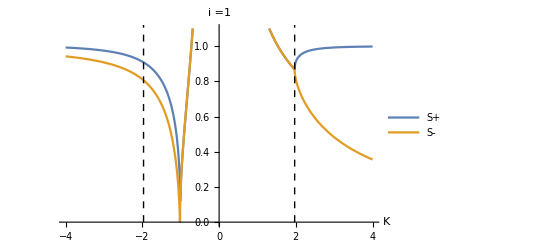
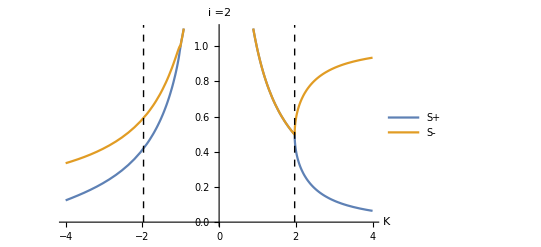
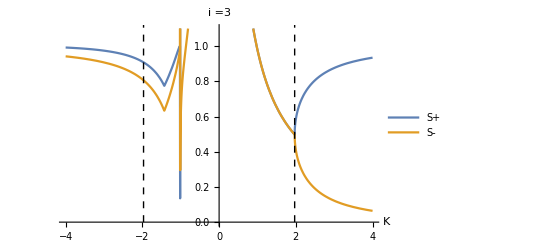
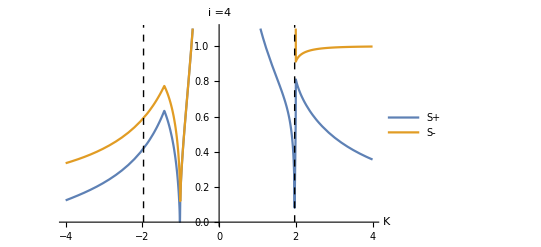
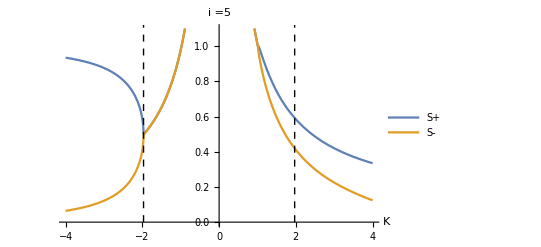
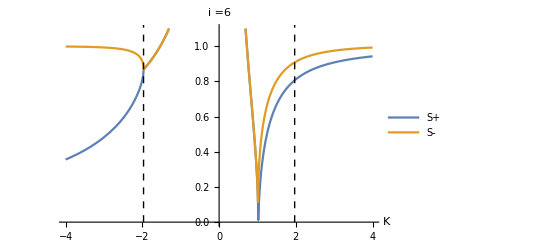
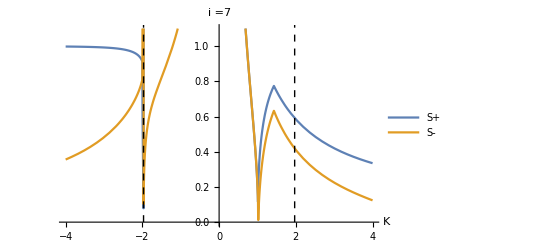
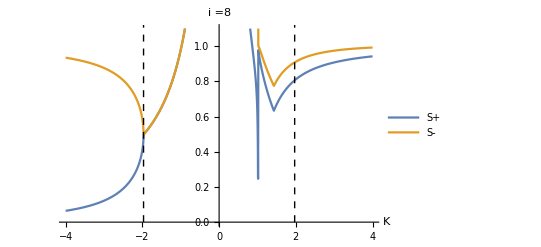

```mathematica
ParallelTable[
Wp4=(Wp//TrigExpand)/.fp4[[i]];
Wm4=(Wm//TrigExpand)/.fp4[[i]];
e1=0.1;
Plot[{Abs[Wp4/.e->e1],Abs[Wm4/.e->e1]},{k,-4,4},PlotRange->{0,1.1},AxesLabel->{"K"},LabelStyle->15,PlotLabel->"i ="<>ToString[i],PlotLegends->{"S+","S-"},Epilog->{
Black,Dashed,
Line[{{-1.9694507563684027,0},{-1.9694507563684027,2}}],
Line[{{1.9694507563684027,0},{1.9694507563684027,2}}]
}],
{i,1,Length[fp4]}
]
```

Plot versus E

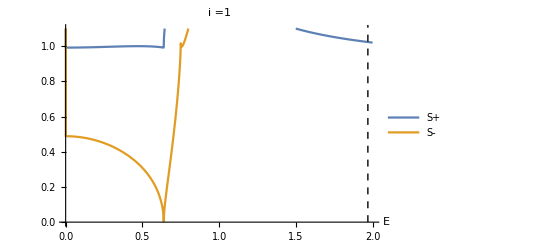
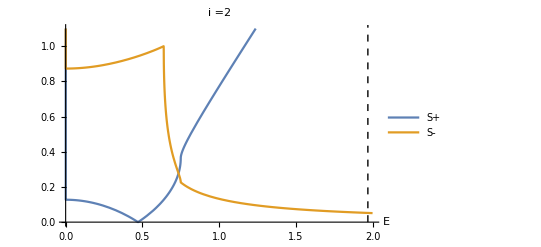
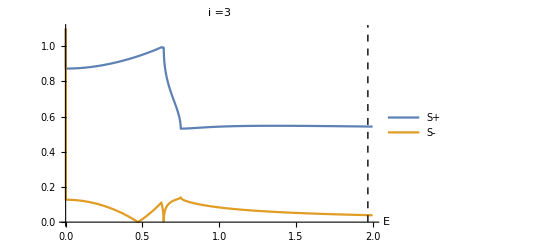
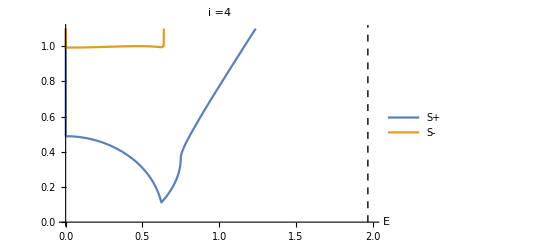
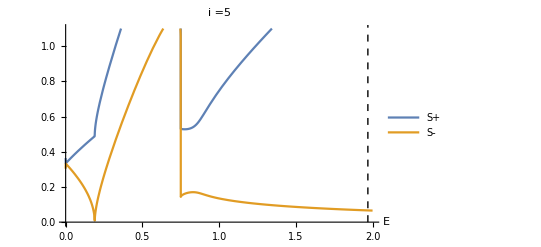
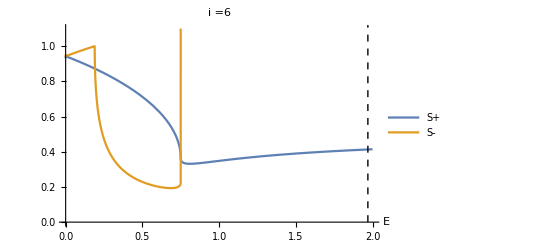
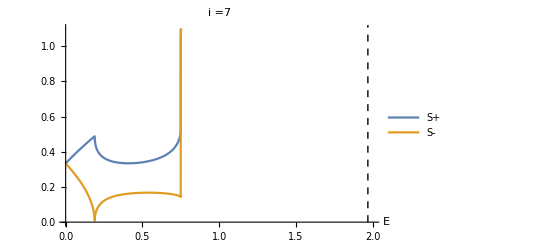
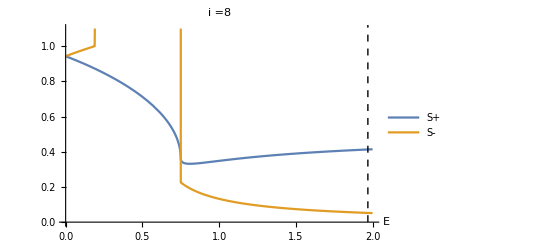

```mathematica
ParallelTable[
Wp4=(Wp//TrigExpand)/.fp4[[i]];
Wm4=(Wm//TrigExpand)/.fp4[[i]];
e1=0.1;
Plot[{Abs[Wp4/.k->3],Abs[Wm4/.k->3]},{e,0,5},PlotRange->{0,1.1},AxesLabel->{"E"},LabelStyle->15,PlotLabel->"i ="<>ToString[i],PlotLegends->{"S+","S-"},Epilog->{
Black,Dashed,
Line[{{-1.9694507563684027,0},{-1.9694507563684027,2}}],
Line[{{1.9694507563684027,0},{1.9694507563684027,2}}]
}],
{i,1,Length[fp4]}
]
```

```mathematica
i=3;
Wp4=(Wp//TrigExpand)/.fp4[[i]];
Wm4=(Wm//TrigExpand)/.fp4[[i]];
```

```mathematica
$Assumptions={{e,k}∈Reals};
ComplexExpand[Abs[Wp4],TargetFunctions->{Re, Im}]
```

√((1)^2+((e^2 Cos[1/2 ArcTan[1]] Cos[1/2 ArcTan[1/4+3+1/2 Cos[1/2 1] (1)^(1/4),1]] ((1)^2+(1)^2)^(1/4))/(((1/4+3+1)^2+(1)^2)^(1/4))+1/1+10+1+(1^2/(4 e^2 k^2)+(1-1)^2)^(1/4) Sin[1/2 ArcTan[1-1/(2 e k),-1/(2 e k)]] (1))^2)
 |  |  |  |

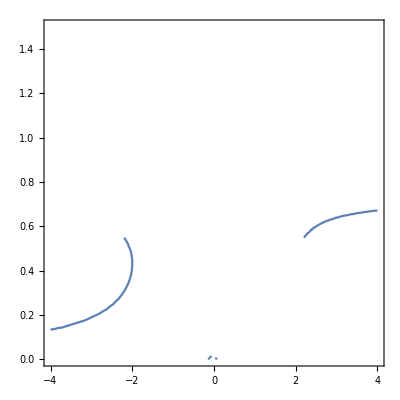

```mathematica
p2=ContourPlot[2+64 e^4-(2 √(-16 e^2+k^2))/k-(8 e^2 (2-2 k^2+k^4+2 k √(-16 e^2+k^2)-k^3 √(-16 e^2+k^2)))/k^2==0,{k,-4,4},{e,0,1.5}]
```

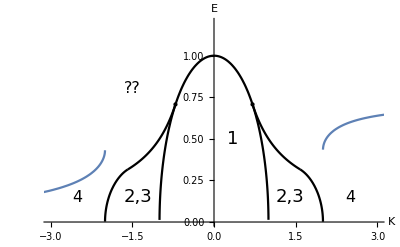

```mathematica
p3=Plot[1/2 √(1-1/k^2+(√(-4+k^2))/k),{k,-4,4}];
Show[{pfinal,p3}]
```

#### Plot

General::munfl: ArcSin[0.509205-1.35902×10^-16 ⅈ] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: ArcSin[0.509205-1.44246×10^-16 ⅈ] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: ArcCos[-0.901507+1.60399×10^-20 ⅈ] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: ArcCos[0.901507+5.52014×10^-17 ⅈ] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: ArcSin[0.509205-1.35902×10^-16 ⅈ] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: ArcSin[0.808364-4.9498×10^-17 ⅈ] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: ArcCos[0.901507-1.60399×10^-20 ⅈ] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

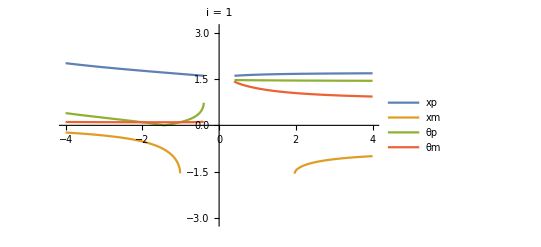
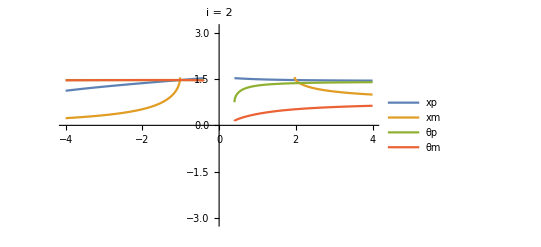
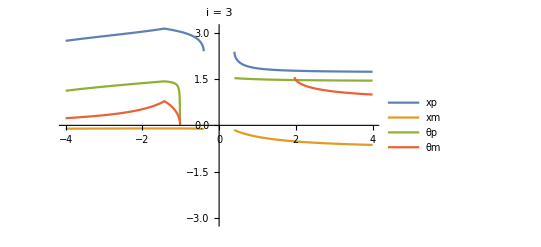
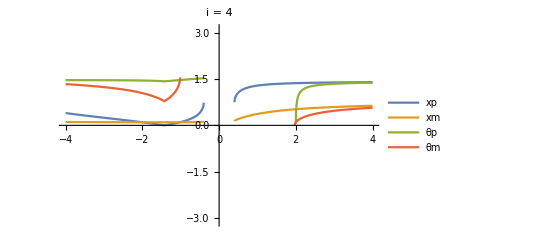
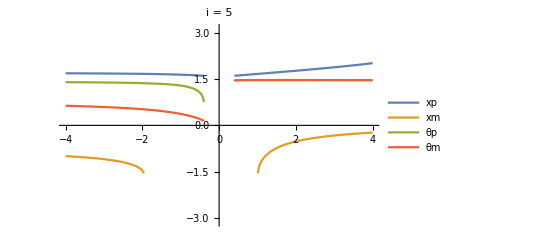
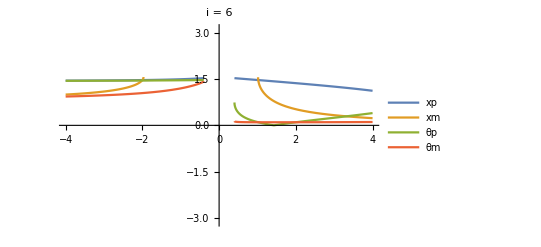
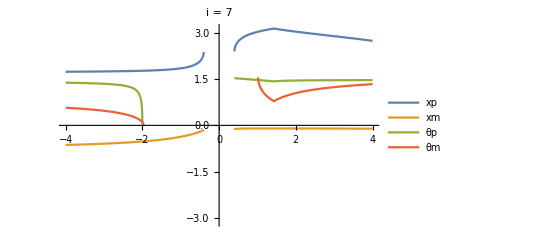
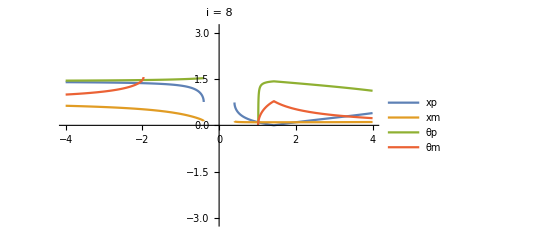

```mathematica
ParallelTable[
Plot[{xp,xm,θp,θm}/.fp4[[i]]/.e->0.1//Evaluate,{k,-4,4},PlotRange->{{-4,4},{-π,π}},PlotLegends->{"xp", "xm", "θp", "θm"},LabelStyle->15,PlotLabel->"i = "<>ToString[i]],
{i,1,Length[fp4]}
]
```

#### Eigenvalues

```mathematica
$Assumptions={};
ParallelTable[
J={D[es, xp],D[es, xm],D[es, θp],D[es, θm]}//FullSimplify;
J1=J/.fp4[[i]]//FullSimplify;
λ=FullSimplify[Eigenvalues[J1]];
fixedpoint=({xp,xm,θp,θm}/.fp4[[i]]);
condFixedPointReal=fixedpoint∈Reals;
condLamStable=Re[λ[[1]]]<=0&&Re[λ[[2]]]<=0&&Re[λ[[3]]]<=0&&Re[λ[[4]]]<=0;
RegionPlot[condFixedPointReal&&condLamStable,{k,-4,3},{e,0,2},PlotLabel->"i = "<>ToString[i]],
{i,1,2}
]
```

$Aborted

```mathematica
i=3;
J={D[es, xp],D[es, xm],D[es, θp],D[es, θm]}//FullSimplify;
J1=J/.fp4[[i]];
λ=Eigenvalues[J1];
TableForm[λ]
```

$Aborted

```mathematica
i=3;
J={D[es, xp],D[es, xm],D[es, θp],D[es, θm]}//FullSimplify;
J1=Simplify[TrigExpand[J]/.fp4[[i]]];
Print["Starting eigenvalues"]
λ=Eigenvalues[J1]
```

$Aborted

```mathematica
ParallelTable[
J={D[es, xp],D[es, xm],D[es, θp],D[es, θm]};
J1=Simplify[TrigExpand[J]/.fp4[[i]]/.{k->-1,e->0.1}];
λ=Eigenvalues[J1];
cond=Re[λ[[1]]]<0&&Re[λ[[2]]]<0&&Re[λ[[3]]]<0&&Re[λ[[4]]]<0;
cond,
{i,1,Length[fp4]}
]
```

{False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False}

Must be some other branch then

#### Order parameter

```mathematica
ParallelTable[
Wp4=(Wp//TrigExpand)/.fp4[[i]];
Wm4=(Wm//TrigExpand)/.fp4[[i]];
e1=0.1;
Plot[{Abs[Wp4/.e->e1],Abs[Wm4/.e->e1]},{k,-4,4},PlotRange->{0,1.1},AxesLabel->{"K"},LabelStyle->15,PlotLabel->"i ="<>ToString[i],PlotLegends->{"S+","S-"},Epilog->{
Black,Dashed,
Line[{{-1.9694507563684027,0},{-1.9694507563684027,2}}],
Line[{{1.9694507563684027,0},{1.9694507563684027,2}}]
}],
{i,1,Length[fp4]}
]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

#### Look at Wp

```mathematica
i=3;
Wp4=(Wp//TrigExpand)/.fp4[[i]];
Wm4=(Wm//TrigExpand)/.fp4[[i]];
```

```mathematica
p1=ContourPlot[
{3-8 e^2+(√(-16 e^2+k^2))/k-√(2+64 e^4-(2 √(-16 e^2+k^2))/k-(8 e^2 (2-2 k^2+k^4+2 k √(-16 e^2+k^2)-k^3 √(-16 e^2+k^2)))/k^2)==0,
√(-16 e^2+k^2)==0,
},
{k,-4,4},{e,0,1},Mesh->Full,Epilog->{Line[{{0,1},{1,1}}]}];

p2= Plot[{},{k,-4,4},PlotStyle->Black];
Show[{p1,p2}]
```

-Graphics-

```mathematica
Wp4
```

-e^2+(ⅈ e^2 √(3/4-2 e^2+(√(-16 e^2+k^2))/(4 k)-1/2 √(1/2 (-1-8 e^2)^2-e^2 k^2-(4 e^2+4 e^2 k^2+16 e^4 k^2+e^2 k^4)/k^2-(k (-(-1-8 e^2)^3+32 (2 e^4+e^4 k^2)+(4 (-1-8 e^2) (4 e^2+4 e^2 k^2+16 e^4 k^2+e^2 k^4))/k^2))/(2 √(-16 e^2+k^2)))))/(√(1/4+2 e^2-(√(-16 e^2+k^2))/(4 k)+1/2 √(1/2 (-1-8 e^2)^2-e^2 k^2-(4 e^2+4 e^2 k^2+16 e^4 k^2+e^2 k^4)/k^2-(k (-(-1-8 e^2)^3+32 (2 e^4+e^4 k^2)+(4 (-1-8 e^2) (4 e^2+4 e^2 k^2+16 e^4 k^2+e^2 k^4))/k^2))/(2 √(-16 e^2+k^2)))))-1/(√2 √k)ⅈ √e √(e k+√(3/4-2 e^2+(√(-16 e^2+k^2))/(4 k)-1/2 √(1/2 (-1-8 e^2)^2-e^2 k^2-(4 e^2+4 e^2 k^2+16 e^4 k^2+e^2 k^4)/k^2-(k (-(-1-8 e^2)^3+32 (2 e^4+e^4 k^2)+(4 (-1-8 e^2) (4 e^2+4 e^2 k^2+16 e^4 k^2+e^2 k^4))/k^2))/(2 √(-16 e^2+k^2)))) √(1/4+2 e^2-(√(-16 e^2+k^2))/(4 k)+1/2 √(1/2 (-1-8 e^2)^2-e^2 k^2-(4 e^2+4 e^2 k^2+16 e^4 k^2+e^2 k^4)/k^2-(k (-(-1-8 e^2)^3+32 (2 e^4+e^4 k^2)+(4 (-1-8 e^2) (4 e^2+4 e^2 k^2+16 e^4 k^2+e^2 k^4))/k^2))/(2 √(-16 e^2+k^2))))) √(1-(2 e^3 k)/(e k+√(3/4-2 e^2+(√(-16 e^2+k^2))/(4 k)-1/2 √(1/2 (-1-8 e^2)^2-e^2 k^2-(4 e^2+4 e^2 k^2+16 e^4 k^2+e^2 k^4)/k^2-(k (-(-1-8 e^2)^3+32 (2 e^4+e^4 k^2)+(4 (-1-8 e^2) (4 e^2+4 e^2 k^2+16 e^4 k^2+e^2 k^4))/k^2))/(2 √(-16 e^2+k^2)))) √(1/4+2 e^2-(√(-16 e^2+k^2))/(4 k)+1/2 √(1/2 (-1-8 e^2)^2-e^2 k^2-(4 e^2+4 e^2 k^2+16 e^4 k^2+e^2 k^4)/k^2-(k (-(-1-8 e^2)^3+32 (2 e^4+e^4 k^2)+(4 (-1-8 e^2) (4 e^2+4 e^2 k^2+16 e^4 k^2+e^2 k^4))/k^2))/(2 √(-16 e^2+k^2))))))-(√e √(3/4-2 e^2+(√(-16 e^2+k^2))/(4 k)-1/2 √(1/2 (-1-8 e^2)^2-e^2 k^2-(4 e^2+4 e^2 k^2+16 e^4 k^2+e^2 k^4)/k^2-(k (-(-1-8 e^2)^3+32 (2 e^4+e^4 k^2)+(4 (-1-8 e^2) (4 e^2+4 e^2 k^2+16 e^4 k^2+e^2 k^4))/k^2))/(2 √(-16 e^2+k^2)))) √(e k+√(3/4-2 e^2+(√(-16 e^2+k^2))/(4 k)-1/2 √(1/2 (-1-8 e^2)^2-e^2 k^2-(4 e^2+4 e^2 k^2+16 e^4 k^2+e^2 k^4)/k^2-(k (-(-1-8 e^2)^3+32 (2 e^4+e^4 k^2)+(4 (-1-8 e^2) (4 e^2+4 e^2 k^2+16 e^4 k^2+e^2 k^4))/k^2))/(2 √(-16 e^2+k^2)))) √(1/4+2 e^2-(√(-16 e^2+k^2))/(4 k)+1/2 √(1/2 (-1-8 e^2)^2-e^2 k^2-(4 e^2+4 e^2 k^2+16 e^4 k^2+e^2 k^4)/k^2-(k (-(-1-8 e^2)^3+32 (2 e^4+e^4 k^2)+(4 (-1-8 e^2) (4 e^2+4 e^2 k^2+16 e^4 k^2+e^2 k^4))/k^2))/(2 √(-16 e^2+k^2))))) √(1-(2 e^3 k)/(e k+√(3/4-2 e^2+(√(-16 e^2+k^2))/(4 k)-1/2 √(1/2 (-1-8 e^2)^2-e^2 k^2-(4 e^2+4 e^2 k^2+16 e^4 k^2+e^2 k^4)/k^2-(k (-(-1-8 e^2)^3+32 (2 e^4+e^4 k^2)+(4 (-1-8 e^2) (4 e^2+4 e^2 k^2+16 e^4 k^2+e^2 k^4))/k^2))/(2 √(-16 e^2+k^2)))) √(1/4+2 e^2-(√(-16 e^2+k^2))/(4 k)+1/2 √(1/2 (-1-8 e^2)^2-e^2 k^2-(4 e^2+4 e^2 k^2+16 e^4 k^2+e^2 k^4)/k^2-(k (-(-1-8 e^2)^3+32 (2 e^4+e^4 k^2)+(4 (-1-8 e^2) (4 e^2+4 e^2 k^2+16 e^4 k^2+e^2 k^4))/k^2))/(2 √(-16 e^2+k^2)))))))/(√2 √k √(1/4+2 e^2-(√(-16 e^2+k^2))/(4 k)+1/2 √(1/2 (-1-8 e^2)^2-e^2 k^2-(4 e^2+4 e^2 k^2+16 e^4 k^2+e^2 k^4)/k^2-(k (-(-1-8 e^2)^3+32 (2 e^4+e^4 k^2)+(4 (-1-8 e^2) (4 e^2+4 e^2 k^2+16 e^4 k^2+e^2 k^4))/k^2))/(2 √(-16 e^2+k^2)))))+(ⅈ √2 e^(3/2) √k √(3/4-2 e^2+(√(-16 e^2+k^2))/(4 k)-1/2 √(1/2 (-1-8 e^2)^2-e^2 k^2-(4 e^2+4 e^2 k^2+16 e^4 k^2+e^2 k^4)/k^2-(k (-(-1-8 e^2)^3+32 (2 e^4+e^4 k^2)+(4 (-1-8 e^2) (4 e^2+4 e^2 k^2+16 e^4 k^2+e^2 k^4))/k^2))/(2 √(-16 e^2+k^2)))) √(1-e^2/(1/4+2 e^2-(√(-16 e^2+k^2))/(4 k)+1/2 √(1/2 (-1-8 e^2)^2-e^2 k^2-(4 e^2+4 e^2 k^2+16 e^4 k^2+e^2 k^4)/k^2-(k (-(-1-8 e^2)^3+32 (2 e^4+e^4 k^2)+(4 (-1-8 e^2) (4 e^2+4 e^2 k^2+16 e^4 k^2+e^2 k^4))/k^2))/(2 √(-16 e^2+k^2))))) √(1-1/(2 e k)(e k+√(3/4-2 e^2+(√(-16 e^2+k^2))/(4 k)-1/2 √(1/2 (-1-8 e^2)^2-e^2 k^2-(4 e^2+4 e^2 k^2+16 e^4 k^2+e^2 k^4)/k^2-(k (-(-1-8 e^2)^3+32 (2 e^4+e^4 k^2)+(4 (-1-8 e^2) (4 e^2+4 e^2 k^2+16 e^4 k^2+e^2 k^4))/k^2))/(2 √(-16 e^2+k^2)))) √(1/4+2 e^2-(√(-16 e^2+k^2))/(4 k)+1/2 √(1/2 (-1-8 e^2)^2-e^2 k^2-(4 e^2+4 e^2 k^2+16 e^4 k^2+e^2 k^4)/k^2-(k (-(-1-8 e^2)^3+32 (2 e^4+e^4 k^2)+(4 (-1-8 e^2) (4 e^2+4 e^2 k^2+16 e^4 k^2+e^2 k^4))/k^2))/(2 √(-16 e^2+k^2)))))))/(√(e k+√(3/4-2 e^2+(√(-16 e^2+k^2))/(4 k)-1/2 √(1/2 (-1-8 e^2)^2-e^2 k^2-(4 e^2+4 e^2 k^2+16 e^4 k^2+e^2 k^4)/k^2-(k (-(-1-8 e^2)^3+32 (2 e^4+e^4 k^2)+(4 (-1-8 e^2) (4 e^2+4 e^2 k^2+16 e^4 k^2+e^2 k^4))/k^2))/(2 √(-16 e^2+k^2)))) √(1/4+2 e^2-(√(-16 e^2+k^2))/(4 k)+1/2 √(1/2 (-1-8 e^2)^2-e^2 k^2-(4 e^2+4 e^2 k^2+16 e^4 k^2+e^2 k^4)/k^2-(k (-(-1-8 e^2)^3+32 (2 e^4+e^4 k^2)+(4 (-1-8 e^2) (4 e^2+4 e^2 k^2+16 e^4 k^2+e^2 k^4))/k^2))/(2 √(-16 e^2+k^2))))))-(√2 e^(3/2) √k √(1/4+2 e^2-(√(-16 e^2+k^2))/(4 k)+1/2 √(1/2 (-1-8 e^2)^2-e^2 k^2-(4 e^2+4 e^2 k^2+16 e^4 k^2+e^2 k^4)/k^2-(k (-(-1-8 e^2)^3+32 (2 e^4+e^4 k^2)+(4 (-1-8 e^2) (4 e^2+4 e^2 k^2+16 e^4 k^2+e^2 k^4))/k^2))/(2 √(-16 e^2+k^2)))) √(1-e^2/(1/4+2 e^2-(√(-16 e^2+k^2))/(4 k)+1/2 √(1/2 (-1-8 e^2)^2-e^2 k^2-(4 e^2+4 e^2 k^2+16 e^4 k^2+e^2 k^4)/k^2-(k (-(-1-8 e^2)^3+32 (2 e^4+e^4 k^2)+(4 (-1-8 e^2) (4 e^2+4 e^2 k^2+16 e^4 k^2+e^2 k^4))/k^2))/(2 √(-16 e^2+k^2))))) √(1-1/(2 e k)(e k+√(3/4-2 e^2+(√(-16 e^2+k^2))/(4 k)-1/2 √(1/2 (-1-8 e^2)^2-e^2 k^2-(4 e^2+4 e^2 k^2+16 e^4 k^2+e^2 k^4)/k^2-(k (-(-1-8 e^2)^3+32 (2 e^4+e^4 k^2)+(4 (-1-8 e^2) (4 e^2+4 e^2 k^2+16 e^4 k^2+e^2 k^4))/k^2))/(2 √(-16 e^2+k^2)))) √(1/4+2 e^2-(√(-16 e^2+k^2))/(4 k)+1/2 √(1/2 (-1-8 e^2)^2-e^2 k^2-(4 e^2+4 e^2 k^2+16 e^4 k^2+e^2 k^4)/k^2-(k (-(-1-8 e^2)^3+32 (2 e^4+e^4 k^2)+(4 (-1-8 e^2) (4 e^2+4 e^2 k^2+16 e^4 k^2+e^2 k^4))/k^2))/(2 √(-16 e^2+k^2)))))))/(√(e k+√(3/4-2 e^2+(√(-16 e^2+k^2))/(4 k)-1/2 √(1/2 (-1-8 e^2)^2-e^2 k^2-(4 e^2+4 e^2 k^2+16 e^4 k^2+e^2 k^4)/k^2-(k (-(-1-8 e^2)^3+32 (2 e^4+e^4 k^2)+(4 (-1-8 e^2) (4 e^2+4 e^2 k^2+16 e^4 k^2+e^2 k^4))/k^2))/(2 √(-16 e^2+k^2)))) √(1/4+2 e^2-(√(-16 e^2+k^2))/(4 k)+1/2 √(1/2 (-1-8 e^2)^2-e^2 k^2-(4 e^2+4 e^2 k^2+16 e^4 k^2+e^2 k^4)/k^2-(k (-(-1-8 e^2)^3+32 (2 e^4+e^4 k^2)+(4 (-1-8 e^2) (4 e^2+4 e^2 k^2+16 e^4 k^2+e^2 k^4))/k^2))/(2 √(-16 e^2+k^2))))))-√(3/4-2 e^2+(√(-16 e^2+k^2))/(4 k)-1/2 √(1/2 (-1-8 e^2)^2-e^2 k^2-(4 e^2+4 e^2 k^2+16 e^4 k^2+e^2 k^4)/k^2-(k (-(-1-8 e^2)^3+32 (2 e^4+e^4 k^2)+(4 (-1-8 e^2) (4 e^2+4 e^2 k^2+16 e^4 k^2+e^2 k^4))/k^2))/(2 √(-16 e^2+k^2)))) √(1-e^2/(1/4+2 e^2-(√(-16 e^2+k^2))/(4 k)+1/2 √(1/2 (-1-8 e^2)^2-e^2 k^2-(4 e^2+4 e^2 k^2+16 e^4 k^2+e^2 k^4)/k^2-(k (-(-1-8 e^2)^3+32 (2 e^4+e^4 k^2)+(4 (-1-8 e^2) (4 e^2+4 e^2 k^2+16 e^4 k^2+e^2 k^4))/k^2))/(2 √(-16 e^2+k^2))))) √(1-(2 e^3 k)/(e k+√(3/4-2 e^2+(√(-16 e^2+k^2))/(4 k)-1/2 √(1/2 (-1-8 e^2)^2-e^2 k^2-(4 e^2+4 e^2 k^2+16 e^4 k^2+e^2 k^4)/k^2-(k (-(-1-8 e^2)^3+32 (2 e^4+e^4 k^2)+(4 (-1-8 e^2) (4 e^2+4 e^2 k^2+16 e^4 k^2+e^2 k^4))/k^2))/(2 √(-16 e^2+k^2)))) √(1/4+2 e^2-(√(-16 e^2+k^2))/(4 k)+1/2 √(1/2 (-1-8 e^2)^2-e^2 k^2-(4 e^2+4 e^2 k^2+16 e^4 k^2+e^2 k^4)/k^2-(k (-(-1-8 e^2)^3+32 (2 e^4+e^4 k^2)+(4 (-1-8 e^2) (4 e^2+4 e^2 k^2+16 e^4 k^2+e^2 k^4))/k^2))/(2 √(-16 e^2+k^2)))))) √(1-1/(2 e k)(e k+√(3/4-2 e^2+(√(-16 e^2+k^2))/(4 k)-1/2 √(1/2 (-1-8 e^2)^2-e^2 k^2-(4 e^2+4 e^2 k^2+16 e^4 k^2+e^2 k^4)/k^2-(k (-(-1-8 e^2)^3+32 (2 e^4+e^4 k^2)+(4 (-1-8 e^2) (4 e^2+4 e^2 k^2+16 e^4 k^2+e^2 k^4))/k^2))/(2 √(-16 e^2+k^2)))) √(1/4+2 e^2-(√(-16 e^2+k^2))/(4 k)+1/2 √(1/2 (-1-8 e^2)^2-e^2 k^2-(4 e^2+4 e^2 k^2+16 e^4 k^2+e^2 k^4)/k^2-(k (-(-1-8 e^2)^3+32 (2 e^4+e^4 k^2)+(4 (-1-8 e^2) (4 e^2+4 e^2 k^2+16 e^4 k^2+e^2 k^4))/k^2))/(2 √(-16 e^2+k^2))))))-ⅈ √(1/4+2 e^2-(√(-16 e^2+k^2))/(4 k)+1/2 √(1/2 (-1-8 e^2)^2-e^2 k^2-(4 e^2+4 e^2 k^2+16 e^4 k^2+e^2 k^4)/k^2-(k (-(-1-8 e^2)^3+32 (2 e^4+e^4 k^2)+(4 (-1-8 e^2) (4 e^2+4 e^2 k^2+16 e^4 k^2+e^2 k^4))/k^2))/(2 √(-16 e^2+k^2)))) √(1-e^2/(1/4+2 e^2-(√(-16 e^2+k^2))/(4 k)+1/2 √(1/2 (-1-8 e^2)^2-e^2 k^2-(4 e^2+4 e^2 k^2+16 e^4 k^2+e^2 k^4)/k^2-(k (-(-1-8 e^2)^3+32 (2 e^4+e^4 k^2)+(4 (-1-8 e^2) (4 e^2+4 e^2 k^2+16 e^4 k^2+e^2 k^4))/k^2))/(2 √(-16 e^2+k^2))))) √(1-(2 e^3 k)/(e k+√(3/4-2 e^2+(√(-16 e^2+k^2))/(4 k)-1/2 √(1/2 (-1-8 e^2)^2-e^2 k^2-(4 e^2+4 e^2 k^2+16 e^4 k^2+e^2 k^4)/k^2-(k (-(-1-8 e^2)^3+32 (2 e^4+e^4 k^2)+(4 (-1-8 e^2) (4 e^2+4 e^2 k^2+16 e^4 k^2+e^2 k^4))/k^2))/(2 √(-16 e^2+k^2)))) √(1/4+2 e^2-(√(-16 e^2+k^2))/(4 k)+1/2 √(1/2 (-1-8 e^2)^2-e^2 k^2-(4 e^2+4 e^2 k^2+16 e^4 k^2+e^2 k^4)/k^2-(k (-(-1-8 e^2)^3+32 (2 e^4+e^4 k^2)+(4 (-1-8 e^2) (4 e^2+4 e^2 k^2+16 e^4 k^2+e^2 k^4))/k^2))/(2 √(-16 e^2+k^2)))))) √(1-1/(2 e k)(e k+√(3/4-2 e^2+(√(-16 e^2+k^2))/(4 k)-1/2 √(1/2 (-1-8 e^2)^2-e^2 k^2-(4 e^2+4 e^2 k^2+16 e^4 k^2+e^2 k^4)/k^2-(k (-(-1-8 e^2)^3+32 (2 e^4+e^4 k^2)+(4 (-1-8 e^2) (4 e^2+4 e^2 k^2+16 e^4 k^2+e^2 k^4))/k^2))/(2 √(-16 e^2+k^2)))) √(1/4+2 e^2-(√(-16 e^2+k^2))/(4 k)+1/2 √(1/2 (-1-8 e^2)^2-e^2 k^2-(4 e^2+4 e^2 k^2+16 e^4 k^2+e^2 k^4)/k^2-(k (-(-1-8 e^2)^3+32 (2 e^4+e^4 k^2)+(4 (-1-8 e^2) (4 e^2+4 e^2 k^2+16 e^4 k^2+e^2 k^4))/k^2))/(2 √(-16 e^2+k^2))))))

```mathematica
f1[k_,e_]:=3-8 e^2+(√(-16 e^2+k^2))/k-√(2+64 e^4-(2 √(-16 e^2+k^2))/k-(8 e^2 (2-2 k^2+k^4+2 k √(-16 e^2+k^2)-k^3 √(-16 e^2+k^2)))/k^2);
f2[k_,e_]:=1+8 e^2-(√(-16 e^2+k^2))/k+√(2+64 e^4-(2 √(-16 e^2+k^2))/k-(8 e^2 (2-2 k^2+k^4+2 k √(-16 e^2+k^2)-k^3 √(-16 e^2+k^2)))/k^2);
f3[k_,e_]:=-√(-16 e^2+k^2)+k (1+8 e^2+√(2+64 e^4-(2 √(-16 e^2+k^2))/k-(8 e^2 (2-2 k^2+k^4+2 k √(-16 e^2+k^2)-k^3 √(-16 e^2+k^2)))/k^2));
f4[k_,e_]:=√(1/2 (-1-8 e^2)^2-e^2 k^2-(4 e^2+4 e^2 k^2+16 e^4 k^2+e^2 k^4)/k^2-(k (-(-1-8 e^2)^3+32 (2 e^4+e^4 k^2)+(4 (-1-8 e^2) (4 e^2+4 e^2 k^2+16 e^4 k^2+e^2 k^4))/k^2))/(2 √(-16 e^2+k^2)));
```

```mathematica
s1=Solve[f1[k,e]==0,e];
s2=Solve[f2[k,e]==0,e];
s3=Solve[f3[k,e]==0,e];
s4=Solve[f4[k,e]==0,e];
Plot[{e/.s1,e/.s2,e/.s3,e/.s4},{k,-4,4}]
```

-Graphics-

```mathematica
ContourPlot[Im[Wp4],
{k,-4,4},{e,0,1},Mesh->Full]
```

-Graphics-

## Roughwork

### Collect subs

```mathematica
tempSub[[4]]
```

{xm→ArcSin[e Sec[xp]],θm→ArcSin[e Sec[θp]]}

```mathematica
sub2
```

{Cos[xp]→c,Sec[xp]→1/c,Tan[xp]→(√(1-c^2))/c,Sin[xp]→√(1-c^2)}

```mathematica
θp->ArcSin[√(1-(1/((√(e k-Cos[xp] Sin[xp]))/(√2 e^(3/2) √k)))^2)];
```

```mathematica
subMaster={xm->ArcSin[e Sec[xp]],θm->ArcSin[e Sec[θp]],θp->ArcSin[√(1-(1/((√(e k-Cos[xp] Sin[xp]))/(√2 e^(3/2) √k)))^2)]};
```

### Collect equations

```mathematica
TrigExpand[et5/.subMaster]
```

-(3 k)/8+6322+(3 Sin[xp]^4 √((e^3 k)/(e k-Cos[xp] Sin[xp])) (1-(2 e^3 k)/(e k-Cos[xp] Sin[xp]))^(5/2) Tan[xp]^6)/(8192 √2 e^4 k (e k-Cos[xp] Sin[xp]))
 |  |  |  |

```mathematica
temp=TrigExpand[et5/.subMaster];
```

```mathematica
t3=Numerator[Together[Simplify[TrigExpand[temp/.sub2]/.Sin[2 xp]->2 Cos[xp] Sin[xp]/.sub2]]]//Simplify
```

-40 √(1-c^2) e^13 k^8-c^18 √(1-c^2) k (4 e k+7 √2 √((e^3 k)/(-c √(1-c^2)+e k)) √((c √(1-c^2)-e k+2 e^3 k)/(c √(1-c^2)-e k)))+c^16 √(1-c^2) k (12 e k+20 e^3 k+21 √2 √((e^3 k)/(-c √(1-c^2)+e k)) √((c √(1-c^2)-e k+2 e^3 k)/(c √(1-c^2)-e k))+40 √2 e^2 √((e^3 k)/(-c √(1-c^2)+e k)) √((c √(1-c^2)-e k+2 e^3 k)/(c √(1-c^2)-e k)))+4 c e^11 k^7 (40 e-√2 k √((e^3 k)/(-c √(1-c^2)+e k)) √((c √(1-c^2)-e k+2 e^3 k)/(c √(1-c^2)-e k)))+4 c^2 √(1-c^2) e^10 k^6 (5 √2 k √((e^3 k)/(-c √(1-c^2)+e k)) √((c √(1-c^2)-e k+2 e^3 k)/(c √(1-c^2)-e k))+2 e (-40+7 k^2))-4 c^3 e^9 k^5 (40 e^3 k^2-√2 k √((e^3 k)/(-c √(1-c^2)+e k)) √((c √(1-c^2)-e k+2 e^3 k)/(c √(1-c^2)-e k)) (-26+k^2)+8 e (-15+7 k^2))-c^14 √(1-c^2) k (12 e k+64 e^5 k+21 √2 √((e^3 k)/(-c √(1-c^2)+e k)) √((c √(1-c^2)-e k+2 e^3 k)/(c √(1-c^2)-e k))+64 √2 e^4 √((e^3 k)/(-c √(1-c^2)+e k)) √((c √(1-c^2)-e k+2 e^3 k)/(c √(1-c^2)-e k))+2 √2 e^2 √((e^3 k)/(-c √(1-c^2)+e k)) √((c √(1-c^2)-e k+2 e^3 k)/(c √(1-c^2)-e k)) (57-35 k^2)-3 e^3 k (-9+8 k^2))+c^17 e (e k (7+16 k^2)+√2 √((e^3 k)/(-c √(1-c^2)+e k)) √((c √(1-c^2)-e k+2 e^3 k)/(c √(1-c^2)-e k)) (1+35 k^2))+c^12 √(1-c^2) k (4 e k+112 e^7 k+7 √2 √((e^3 k)/(-c √(1-c^2)+e k)) √((c √(1-c^2)-e k+2 e^3 k)/(c √(1-c^2)-e k))+4 √2 e^4 √((e^3 k)/(-c √(1-c^2)+e k)) √((c √(1-c^2)-e k+2 e^3 k)/(c √(1-c^2)-e k)) (48-101 k^2)-4 √2 e^2 √((e^3 k)/(-c √(1-c^2)+e k)) √((c √(1-c^2)-e k+2 e^3 k)/(c √(1-c^2)-e k)) (-27+35 k^2)+e^5 (80 k-136 k^3)-6 e^3 (k+8 k^3))-c^15 e (200 √2 e^2 k^2 √((e^3 k)/(-c √(1-c^2)+e k)) √((c √(1-c^2)-e k+2 e^3 k)/(c √(1-c^2)-e k))+3 e k (7+16 k^2)+3 √2 √((e^3 k)/(-c √(1-c^2)+e k)) √((c √(1-c^2)-e k+2 e^3 k)/(c √(1-c^2)-e k)) (1+35 k^2)+e^3 (22 k+80 k^3))+c^13 e (260 e^5 k^3+324 √2 e^4 k^2 √((e^3 k)/(-c √(1-c^2)+e k)) √((c √(1-c^2)-e k+2 e^3 k)/(c √(1-c^2)-e k))+5 √2 e^2 k^2 √((e^3 k)/(-c √(1-c^2)+e k)) √((c √(1-c^2)-e k+2 e^3 k)/(c √(1-c^2)-e k)) (117-14 k^2)+3 e k (7+16 k^2)+3 √2 √((e^3 k)/(-c √(1-c^2)+e k)) √((c √(1-c^2)-e k+2 e^3 k)/(c √(1-c^2)-e k)) (1+35 k^2)+2 e^3 k (33+89 k^2-8 k^4))+4 c^4 √(1-c^2) e^8 k^4 (90 e^3 k^2-5 √2 k √((e^3 k)/(-c √(1-c^2)+e k)) √((c √(1-c^2)-e k+2 e^3 k)/(c √(1-c^2)-e k)) (-18+k^2)-2 e (65-47 k^2+2 k^4))+c^9 e^3 k (-684 √2 e^4 k^3 √((e^3 k)/(-c √(1-c^2)+e k)) √((c √(1-c^2)-e k+2 e^3 k)/(c √(1-c^2)-e k))+5 √2 k √((e^3 k)/(-c √(1-c^2)+e k)) √((c √(1-c^2)-e k+2 e^3 k)/(c √(1-c^2)-e k)) (37-14 k^2)+e^5 (1232 k^2-492 k^4)+e^3 (316 k^2-261 k^4)+e (22+18 k^2-16 k^4)+√2 e^2 k √((e^3 k)/(-c √(1-c^2)+e k)) √((c √(1-c^2)-e k+2 e^3 k)/(c √(1-c^2)-e k)) (964-825 k^2+7 k^4))+c^7 e^5 k^2 (632 e^5 k^3-16 √2 e^2 k^2 √((e^3 k)/(-c √(1-c^2)+e k)) √((c √(1-c^2)-e k+2 e^3 k)/(c √(1-c^2)-e k)) (-84+5 k^2)+e k (-28+117 k^2)+√2 √((e^3 k)/(-c √(1-c^2)+e k)) √((c √(1-c^2)-e k+2 e^3 k)/(c √(1-c^2)-e k)) (-320+405 k^2-7 k^4)-2 e^3 k (548-427 k^2+32 k^4))+c^5 e^7 k^3 (108 √2 e^2 k^3 √((e^3 k)/(-c √(1-c^2)+e k)) √((c √(1-c^2)-e k+2 e^3 k)/(c √(1-c^2)-e k))+8 e^3 k^2 (-139+28 k^2)+√2 k √((e^3 k)/(-c √(1-c^2)+e k)) √((c √(1-c^2)-e k+2 e^3 k)/(c √(1-c^2)-e k)) (-660+79 k^2)+e (320-362 k^2+64 k^4))-c^6 √(1-c^2) e^6 k^2 (376 √2 e^2 k^3 √((e^3 k)/(-c √(1-c^2)+e k)) √((c √(1-c^2)-e k+2 e^3 k)/(c √(1-c^2)-e k))+4 e^3 k^2 (-314+101 k^2)+2 √2 k √((e^3 k)/(-c √(1-c^2)+e k)) √((c √(1-c^2)-e k+2 e^3 k)/(c √(1-c^2)-e k)) (-322+117 k^2)+e (80-208 k^2+111 k^4))-c^11 e (456 e^7 k^3+4 √2 e^4 k^2 √((e^3 k)/(-c √(1-c^2)+e k)) √((c √(1-c^2)-e k+2 e^3 k)/(c √(1-c^2)-e k)) (242-105 k^2)+10 √2 e^2 k^2 √((e^3 k)/(-c √(1-c^2)+e k)) √((c √(1-c^2)-e k+2 e^3 k)/(c √(1-c^2)-e k)) (57-14 k^2)+e k (7+16 k^2)+√2 √((e^3 k)/(-c √(1-c^2)+e k)) √((c √(1-c^2)-e k+2 e^3 k)/(c √(1-c^2)-e k)) (1+35 k^2)+e^5 (548 k^3-144 k^5)+e^3 (66 k+116 k^3-32 k^5))+c^10 √(1-c^2) e^2 k (660 √2 e^4 k^2 √((e^3 k)/(-c √(1-c^2)+e k)) √((c √(1-c^2)-e k+2 e^3 k)/(c √(1-c^2)-e k))+e k (13+24 k^2)+2 √2 √((e^3 k)/(-c √(1-c^2)+e k)) √((c √(1-c^2)-e k+2 e^3 k)/(c √(1-c^2)-e k)) (-17+35 k^2)+4 e^5 k (-76+113 k^2)+√2 e^2 √((e^3 k)/(-c √(1-c^2)+e k)) √((c √(1-c^2)-e k+2 e^3 k)/(c √(1-c^2)-e k)) (-192+788 k^2-35 k^4)+e^3 (32 k+214 k^3-4 k^5))+c^8 √(1-c^2) e^4 k (-736 e^5 k^3+8 √2 e^2 k^2 √((e^3 k)/(-c √(1-c^2)+e k)) √((c √(1-c^2)-e k+2 e^3 k)/(c √(1-c^2)-e k)) (-163+30 k^2)+4 e^3 k (68-165 k^2+29 k^4)+√2 √((e^3 k)/(-c √(1-c^2)+e k)) √((c √(1-c^2)-e k+2 e^3 k)/(c √(1-c^2)-e k)) (64-384 k^2+35 k^4)+e (-48 k-78 k^3+4 k^5))

```mathematica
t4=Numerator[Together[TrigExpand[et4/.subMaster]/.sub2/.subMaster/.Sin[2 xp]->2 Cos[xp] Sin[xp]/.sub2]]//Simplify
```

8 √(1-c^2) e^8 k^4 √((e^3 k)/(-c √(1-c^2)+e k))-c^9 e^2 √((2 c √(1-c^2)-2 e k+4 e^3 k)/(c √(1-c^2)-e k)) (-1+k^2)+c^8 √(1-c^2) (-√((e^3 k)/(-c √(1-c^2)+e k))+6 e^2 √((e^3 k)/(-c √(1-c^2)+e k))-e k √((2 c √(1-c^2)-2 e k+4 e^3 k)/(c √(1-c^2)-e k)))+4 c e^7 k^3 (-2 √((e^3 k)/(-c √(1-c^2)+e k))+e k √((2 c √(1-c^2)-2 e k+4 e^3 k)/(c √(1-c^2)-e k)))+c^10 √(1-c^2) (√((e^3 k)/(-c √(1-c^2)+e k))+e k √((2 c √(1-c^2)-2 e k+4 e^3 k)/(c √(1-c^2)-e k)))-4 c^2 √(1-c^2) e^6 k^2 (2 √((e^3 k)/(-c √(1-c^2)+e k))+2 k^2 √((e^3 k)/(-c √(1-c^2)+e k))+e k √((2 c √(1-c^2)-2 e k+4 e^3 k)/(c √(1-c^2)-e k)))+c^6 √(1-c^2) e^2 (-6 √((e^3 k)/(-c √(1-c^2)+e k))+(1-4 e^2) k^2 √((e^3 k)/(-c √(1-c^2)+e k))+2 e (1-4 e^2) k √((2 c √(1-c^2)-2 e k+4 e^3 k)/(c √(1-c^2)-e k)))+4 c^4 √(1-c^2) e^4 k ((-1+6 e^2) k √((e^3 k)/(-c √(1-c^2)+e k))+2 e √((2 c √(1-c^2)-2 e k+4 e^3 k)/(c √(1-c^2)-e k))+e k^2 √((2 c √(1-c^2)-2 e k+4 e^3 k)/(c √(1-c^2)-e k)))+4 c^3 e^5 k (2 √((e^3 k)/(-c √(1-c^2)+e k))+2 (1+e^2) k^2 √((e^3 k)/(-c √(1-c^2)+e k))-2 e k √((2 c √(1-c^2)-2 e k+4 e^3 k)/(c √(1-c^2)-e k))-e k^3 √((2 c √(1-c^2)-2 e k+4 e^3 k)/(c √(1-c^2)-e k)))+c^7 e^2 (-10 e k √((e^3 k)/(-c √(1-c^2)+e k))+16 e^3 k √((e^3 k)/(-c √(1-c^2)+e k))+√((2 c √(1-c^2)-2 e k+4 e^3 k)/(c √(1-c^2)-e k)) (-1+k^2))-c^5 e^3 k (-10 √((e^3 k)/(-c √(1-c^2)+e k))+e k √((2 c √(1-c^2)-2 e k+4 e^3 k)/(c √(1-c^2)-e k))-12 e^3 k √((2 c √(1-c^2)-2 e k+4 e^3 k)/(c √(1-c^2)-e k))+8 e^2 √((e^3 k)/(-c √(1-c^2)+e k)) (3+k^2))

```mathematica
out=removeSqRoot[t4,√((e^3 k)/(-c √(1-c^2)+e k))]
```

2 c^16 e^4-6 c^18 e^4+6 c^20 e^4-2 c^22 e^4+5 c^17 √(1-c^2) e^3 k-15 c^19 √(1-c^2) e^3 k+15 c^21 √(1-c^2) e^3 k-5 c^23 √(1-c^2) e^3 k-12 c^17 √(1-c^2) e^5 k+24 c^19 √(1-c^2) e^5 k-12 c^21 √(1-c^2) e^5 k+4 c^13 √(1-c^2) e^7 k-8 c^15 √(1-c^2) e^7 k+4 c^17 √(1-c^2) e^7 k+2 c^18 e^2 k^2-8 c^20 e^2 k^2+12 c^22 e^2 k^2-8 c^24 e^2 k^2+2 c^26 e^2 k^2-21 c^16 e^4 k^2+63 c^18 e^4 k^2-63 c^20 e^4 k^2+21 c^22 e^4 k^2-34 c^14 e^6 k^2+172 c^16 e^6 k^2-282 c^18 e^6 k^2+184 c^20 e^6 k^2-40 c^22 e^6 k^2-12 c^12 e^8 k^2+32 c^14 e^8 k^2-60 c^16 e^8 k^2+72 c^18 e^8 k^2-32 c^20 e^8 k^2+32 c^10 e^10 k^2-96 c^12 e^10 k^2+96 c^14 e^10 k^2-32 c^16 e^10 k^2-8 c^17 √(1-c^2) e^3 k^3+24 c^19 √(1-c^2) e^3 k^3-24 c^21 √(1-c^2) e^3 k^3+8 c^23 √(1-c^2) e^3 k^3+38 c^15 √(1-c^2) e^5 k^3-72 c^17 √(1-c^2) e^5 k^3+26 c^19 √(1-c^2) e^5 k^3+12 c^21 √(1-c^2) e^5 k^3-4 c^23 √(1-c^2) e^5 k^3+88 c^13 √(1-c^2) e^7 k^3-384 c^15 √(1-c^2) e^7 k^3+464 c^17 √(1-c^2) e^7 k^3-168 c^19 √(1-c^2) e^7 k^3-4 c^11 √(1-c^2) e^9 k^3+16 c^13 √(1-c^2) e^9 k^3+148 c^15 √(1-c^2) e^9 k^3-224 c^17 √(1-c^2) e^9 k^3+64 c^19 √(1-c^2) e^9 k^3-160 c^9 √(1-c^2) e^11 k^3+416 c^11 √(1-c^2) e^11 k^3-384 c^13 √(1-c^2) e^11 k^3+128 c^15 √(1-c^2) e^11 k^3+64 c^7 √(1-c^2) e^13 k^3-128 c^9 √(1-c^2) e^13 k^3+64 c^11 √(1-c^2) e^13 k^3+12 c^16 e^4 k^4-36 c^18 e^4 k^4+36 c^20 e^4 k^4-12 c^22 e^4 k^4-54 c^14 e^6 k^4+112 c^16 e^6 k^4-50 c^18 e^6 k^4-20 c^20 e^6 k^4+12 c^22 e^6 k^4-58 c^12 e^8 k^4+426 c^14 e^8 k^4-648 c^16 e^8 k^4+280 c^18 e^8 k^4+60 c^10 e^10 k^4-256 c^12 e^10 k^4-28 c^14 e^10 k^4+448 c^16 e^10 k^4-224 c^18 e^10 k^4+256 c^8 e^12 k^4-832 c^10 e^12 k^4+1152 c^12 e^12 k^4-704 c^14 e^12 k^4+128 c^16 e^12 k^4-192 c^6 e^14 k^4+512 c^8 e^14 k^4-448 c^10 e^14 k^4+128 c^12 e^14 k^4-8 c^15 √(1-c^2) e^5 k^5+16 c^17 √(1-c^2) e^5 k^5-8 c^19 √(1-c^2) e^5 k^5+85 c^13 √(1-c^2) e^7 k^5-137 c^15 √(1-c^2) e^7 k^5+40 c^17 √(1-c^2) e^7 k^5+12 c^19 √(1-c^2) e^7 k^5-104 c^11 √(1-c^2) e^9 k^5-124 c^13 √(1-c^2) e^9 k^5+248 c^15 √(1-c^2) e^9 k^5-32 c^17 √(1-c^2) e^9 k^5-128 c^9 √(1-c^2) e^11 k^5+628 c^11 √(1-c^2) e^11 k^5-176 c^13 √(1-c^2) e^11 k^5-240 c^15 √(1-c^2) e^11 k^5+64 c^7 √(1-c^2) e^13 k^5-64 c^9 √(1-c^2) e^13 k^5-480 c^11 √(1-c^2) e^13 k^5+320 c^13 √(1-c^2) e^13 k^5+64 c^5 √(1-c^2) e^15 k^5-192 c^7 √(1-c^2) e^15 k^5+192 c^9 √(1-c^2) e^15 k^5+2 c^14 e^6 k^6-4 c^16 e^6 k^6+2 c^18 e^6 k^6-101 c^12 e^8 k^6+193 c^14 e^8 k^6-88 c^16 e^8 k^6-4 c^18 e^8 k^6+266 c^10 e^10 k^6-232 c^12 e^10 k^6-128 c^14 e^10 k^6+96 c^16 e^10 k^6+96 c^8 e^12 k^6-900 c^10 e^12 k^6+832 c^12 e^12 k^6-48 c^14 e^12 k^6-576 c^6 e^14 k^6+1600 c^8 e^14 k^6-832 c^10 e^14 k^6-128 c^12 e^14 k^6+320 c^4 e^16 k^6-704 c^6 e^16 k^6+320 c^8 e^16 k^6+64 c^11 √(1-c^2) e^9 k^7-64 c^13 √(1-c^2) e^9 k^7-304 c^9 √(1-c^2) e^11 k^7+128 c^11 √(1-c^2) e^11 k^7+96 c^13 √(1-c^2) e^11 k^7+208 c^7 √(1-c^2) e^13 k^7+416 c^9 √(1-c^2) e^13 k^7-224 c^11 √(1-c^2) e^13 k^7+352 c^5 √(1-c^2) e^15 k^7-1056 c^7 √(1-c^2) e^15 k^7+128 c^9 √(1-c^2) e^15 k^7-320 c^3 √(1-c^2) e^17 k^7+576 c^5 √(1-c^2) e^17 k^7-16 c^10 e^10 k^8+16 c^12 e^10 k^8+240 c^8 e^12 k^8-192 c^10 e^12 k^8-32 c^12 e^12 k^8-544 c^6 e^14 k^8+336 c^8 e^14 k^8+96 c^10 e^14 k^8+384 c^4 e^16 k^8-96 c^6 e^16 k^8-64 c^8 e^16 k^8-64 c^2 e^18 k^8-64 c^4 e^18 k^8-128 c^7 √(1-c^2) e^13 k^9+448 c^5 √(1-c^2) e^15 k^9-512 c^3 √(1-c^2) e^17 k^9+192 c √(1-c^2) e^19 k^9+32 c^6 e^14 k^10-128 c^4 e^16 k^10+160 c^2 e^18 k^10-64 e^20 k^10

```mathematica
Collect[removeSqRoot[out,√(1-c^2) ],k,Simplify]
```

4 c^32 (-1+c^2)^6 e^4+c^26 (-1+c^2)^5 e^2 (17 c^12-112 e^8-16 c^4 e^4 (-11+8 e^2)+16 c^2 e^6 (3+8 e^2)+2 c^10 (-17+60 e^2)+4 c^6 e^2 (21-114 e^2+32 e^4)+c^8 (17-204 e^2+304 e^4)) k^2+c^20 (-1+c^2)^4 (-16 c^22+4 c^24+512 e^16+32 c^6 e^10 (19+115 e^2-112 e^4)+4 c^20 (6+e^2-30 e^4)+16 c^4 e^12 (-101+128 e^2+64 e^4)-4 c^18 (4+3 e^2-106 e^4+8 e^6)-4 c^10 e^6 (-87+1150 e^2-1336 e^4+256 e^6)+4 c^8 e^8 (323-756 e^2-464 e^4+512 e^6)+2 c^14 e^2 (-2+119 e^2+224 e^4-1776 e^6+512 e^8)+c^16 (4+12 e^2-515 e^4+48 e^6+960 e^8)+c^12 e^4 (-27-812 e^2+5960 e^4-3840 e^6+1024 e^8)-256 c^2 (e^14+6 e^16)) k^4+2 c^14 (-1+c^2)^3 e^2 (2048 e^20-32 c^26 (-1+e^2)^2+8 c^28 (1-e^2+e^4)+256 c^4 e^16 (9+40 e^2+8 e^4)-512 c^6 e^14 (-1+17 e^2+20 e^4)+8 c^8 e^12 (-429+368 e^2+2048 e^4+512 e^6)-16 c^10 e^10 (-100-661 e^2+1080 e^4+832 e^6)-8 c^24 (-6+20 e^2+27 e^4-32 e^6+32 e^8)+8 c^22 (-4+22 e^2+119 e^4-190 e^6+128 e^8)+8 c^12 e^8 (239-1168 e^2-915 e^4+3136 e^6+512 e^8)-4 c^14 e^6 (1+1874 e^2-5116 e^4+1856 e^6+3840 e^8)-2 c^18 e^2 (-8-399 e^2+1464 e^4+3128 e^6-5248 e^8+4096 e^10)+c^16 e^4 (-171+940 e^2+10664 e^4-20928 e^6+13824 e^8+4096 e^10)+c^20 (8-88 e^2-1339 e^4+3256 e^6+448 e^8-2304 e^10+2048 e^12)-4096 c^2 (e^18+e^20)) k^6+2 c^12 (-1+c^2)^2 e^4 (14336 e^20-4096 c^2 e^18 (8+11 e^2)+12 c^28 (1-2 e^2+2 e^4)+512 c^4 e^16 (37+236 e^2+100 e^4)+16 c^26 (-3+14 e^2-14 e^4+8 e^6)-256 c^6 e^14 (-19+352 e^2+704 e^4+112 e^6)+c^24 (72-620 e^2+288 e^4+416 e^6-960 e^8)+8 c^8 e^12 (-1447-160 e^2+22848 e^4+18432 e^6+1024 e^8)-16 c^10 e^10 (-303-2857 e^2+3128 e^4+12752 e^6+4352 e^8)+c^22 (-48+756 e^2+608 e^4-5328 e^6+6336 e^8-1792 e^10)+2 c^12 e^8 (1675-14936 e^2-28356 e^4+57536 e^6+66048 e^8+8192 e^10)-4 c^14 e^6 (307+3066 e^2-17116 e^4-1200 e^6+27328 e^8+12288 e^10)-2 c^18 e^2 (-46-635 e^2+7252 e^4+144 e^6-18304 e^8+18816 e^10+4096 e^12)+c^16 e^4 (-331+7020 e^2+13936 e^4-73920 e^6+45888 e^8+49152 e^10+8192 e^12)+c^20 (12-428 e^2-1635 e^4+13496 e^6-10080 e^8-4480 e^10+9728 e^12)) k^8+c^10 (-1+c^2) e^6 (86016 e^20-4096 c^2 e^18 (55+84 e^2)+16 c^28 (1-3 e^2+3 e^4)+1024 c^4 e^16 (169+976 e^2+516 e^4)+64 c^26 (-1+9 e^2-15 e^4+12 e^6)-256 c^6 e^14 (-3+3474 e^2+7008 e^4+1504 e^6)-16 c^24 (-6+110 e^2-227 e^4+80 e^6+144 e^8)+512 c^8 e^12 (-124+208 e^2+3717 e^4+3256 e^6+232 e^8)-16 c^10 e^10 (-1829-17166 e^2+31568 e^4+136800 e^6+51456 e^8)-16 c^22 (4-144 e^2+341 e^4+802 e^6-1656 e^8+800 e^10)+16 c^12 e^8 (390-10360 e^2-25697 e^4+59776 e^6+90560 e^8+10752 e^10)-4 c^14 e^6 (1611+3586 e^2-89560 e^4-42912 e^6+234112 e^8+128512 e^10)-2 c^18 e^2 (-160+365 e^2+28124 e^4-32352 e^6-77888 e^8+97280 e^10+46080 e^12)+c^20 (16-1392 e^2+3541 e^4+44816 e^6-68416 e^8-1536 e^10+54528 e^12)+c^16 e^4 (-75+31220 e^2-12352 e^4-363456 e^6+169472 e^8+467968 e^10+69632 e^12)) k^10+c^8 e^8 (143360 e^20+4 c^28 (1-2 e^2)^2-20480 c^2 e^18 (21+32 e^2)+512 c^4 e^16 (839+4088 e^2+2264 e^4)+16 c^26 (-1+20 e^2-52 e^4+48 e^6)-1024 c^6 e^14 (105+2221 e^2+3972 e^4+928 e^6)+4 c^24 (6-275 e^2+1198 e^4-1136 e^6+96 e^8)+768 c^8 e^12 (-116+969 e^2+6408 e^4+5104 e^6+400 e^8)-128 c^10 e^10 (-506-2775 e^2+16236 e^4+43104 e^6+14272 e^8)-4 c^22 (4-385 e^2+2650 e^4-176 e^6-6368 e^8+6016 e^10)+4 c^12 e^8 (-1295-83460 e^2-102876 e^4+756096 e^6+820736 e^8+75776 e^10)-4 c^14 e^6 (1777-11794 e^2-162784 e^4+30336 e^6+596352 e^8+229376 e^10)-2 c^18 e^2 (-118+2813 e^2+22232 e^4-91920 e^6-80640 e^8+203264 e^10+69632 e^12)+c^16 e^4 (1089+29844 e^2-139176 e^4-563392 e^6+586624 e^8+939008 e^10+81920 e^12)+c^20 (4-980 e^2+11161 e^4+24800 e^6-112512 e^8+44032 e^10+87296 e^12)) k^12+32 c^6 e^12 (-4480 e^18+2 c^24 (1-2 e^2)^2+1920 c^2 e^16 (8+9 e^2)-16 c^4 e^14 (1197+3872 e^2+1448 e^4)+2 c^22 (-3+34 e^2-62 e^4+36 e^6)+8 c^6 e^12 (1155+10264 e^2+11264 e^4+1360 e^6)-4 c^8 e^10 (-149+11272 e^2+32780 e^4+13024 e^6)+c^20 (6-149 e^2+268 e^4+308 e^6-656 e^8)+8 c^10 e^8 (-277+320 e^2+10518 e^4+11300 e^6+896 e^8)-4 c^12 e^6 (-156-1945 e^2+3917 e^4+17836 e^6+5440 e^8)+2 c^18 (-1+63 e^2-61 e^4-1183 e^6+1128 e^8+960 e^10)+c^14 e^4 (67-2727 e^2-8114 e^4+23272 e^6+24608 e^8+1024 e^10)-c^16 e^2 (37+97 e^2-4091 e^4-916 e^6+12448 e^8+2368 e^10)) k^14+64 c^4 e^16 (c^2-e^2)^2 (1344 e^12-1280 c^2 e^10 (2+3 e^2)+2 c^16 (3-10 e^2+8 e^4)+32 c^4 e^8 (45+244 e^2+90 e^4)-4 c^6 e^6 (13+1246 e^2+1744 e^4)-4 c^14 (3-23 e^2+18 e^4+16 e^6)+4 c^8 e^4 (-47+171 e^2+1356 e^4+288 e^6)+c^10 (39 e^2+406 e^4-1360 e^6-1632 e^8)+c^12 (6-111 e^2-156 e^4+720 e^6+64 e^8)) k^16-1024 c^2 e^20 (c^2-e^2)^3 (-28 e^8+8 c^6 e^4 (4+e^2)+c^10 (-1+2 e^2)-4 c^4 e^4 (4+17 e^2)+c^8 (1-3 e^2-8 e^4)+c^2 (40 e^6+44 e^8)) k^18+1024 e^24 (c^2-2 e^2)^2 (c^2-e^2)^4 k^20

### Collect equations

```mathematica
chareqn=Det[J-λ1 IdentityMatribx[4]]/.tempSub[[4]]/.j->k//TrigExpand
chareqn=Collect[chareqn,λ1,Simplify]
```

λ1^4+1/4 λ1^3 Sec[xp]^2 Sec[θp]^2 (2 k-16 e^2 k+32 e^4 k-2 (-1+4 e^2) k Cos[2 xp]+k Cos[2 (xp-θp)]+2 k Cos[2 θp]-8 e^2 k Cos[2 θp]+k Cos[2 (xp+θp)]-2 e Sin[2 xp]-2 e Sin[2 θp]-2 e Sin[2 (xp+θp)])-1/512 λ1^2 Sec[xp]^4 Sec[θp]^4 (120-192 e^2-72 k^2+768 e^2 k^2-1536 e^4 k^2-2 (-85+48 k^2+512 e^4 k^2-112 e^2 (-1+4 k^2)) Cos[2 xp]-8 (-7+3 k^2+32 e^4 k^2+e^2 (4-16 k^2)) Cos[4 xp]+6 Cos[6 xp]+Cos[4 xp-6 θp]+Cos[6 xp-4 θp]+4 Cos[2 (xp-3 θp)]+39 Cos[2 (xp-2 θp)]-48 e^2 Cos[2 (xp-2 θp)]-16 k^2 Cos[2 (xp-2 θp)]+64 e^2 k^2 Cos[2 (xp-2 θp)]+39 Cos[4 xp-2 θp]-48 e^2 Cos[4 xp-2 θp]-16 k^2 Cos[4 xp-2 θp]+64 e^2 k^2 Cos[4 xp-2 θp]+4 Cos[6 xp-2 θp]+120 Cos[2 (xp-θp)]-192 e^2 Cos[2 (xp-θp)]-64 k^2 Cos[2 (xp-θp)]+512 e^2 k^2 Cos[2 (xp-θp)]+12 Cos[4 (xp-θp)]-16 e^2 Cos[4 (xp-θp)]-4 k^2 Cos[4 (xp-θp)]+170 Cos[2 θp]-224 e^2 Cos[2 θp]-96 k^2 Cos[2 θp]+896 e^2 k^2 Cos[2 θp]-1024 e^4 k^2 Cos[2 θp]+56 Cos[4 θp]-32 e^2 Cos[4 θp]-24 k^2 Cos[4 θp]+128 e^2 k^2 Cos[4 θp]-256 e^4 k^2 Cos[4 θp]+6 Cos[6 θp]+120 Cos[2 (xp+θp)]-64 e^2 Cos[2 (xp+θp)]-64 k^2 Cos[2 (xp+θp)]+512 e^2 k^2 Cos[2 (xp+θp)]+12 Cos[4 (xp+θp)]+16 e^2 Cos[4 (xp+θp)]-4 k^2 Cos[4 (xp+θp)]+39 Cos[2 (2 xp+θp)]+16 e^2 Cos[2 (2 xp+θp)]-16 k^2 Cos[2 (2 xp+θp)]+64 e^2 k^2 Cos[2 (2 xp+θp)]+4 Cos[2 (3 xp+θp)]+39 Cos[2 (xp+2 θp)]+16 e^2 Cos[2 (xp+2 θp)]-16 k^2 Cos[2 (xp+2 θp)]+64 e^2 k^2 Cos[2 (xp+2 θp)]+4 Cos[2 (xp+3 θp)]+Cos[6 xp+4 θp]+Cos[4 xp+6 θp]+144 e k Sin[2 xp]-960 e^3 k Sin[2 xp]+1536 e^5 k Sin[2 xp]+72 e k Sin[4 xp]-192 e^3 k Sin[4 xp]-24 e k Sin[2 (xp-2 θp)]+24 e k Sin[4 xp-2 θp]+144 e k Sin[2 θp]-960 e^3 k Sin[2 θp]+1536 e^5 k Sin[2 θp]+72 e k Sin[4 θp]-192 e^3 k Sin[4 θp]+192 e k Sin[2 (xp+θp)]-1152 e^3 k Sin[2 (xp+θp)]+1536 e^5 k Sin[2 (xp+θp)]+24 e k Sin[4 (xp+θp)]+72 e k Sin[2 (2 xp+θp)]-192 e^3 k Sin[2 (2 xp+θp)]+72 e k Sin[2 (xp+2 θp)]-192 e^3 k Sin[2 (xp+2 θp)])-1/2048 λ1 Sec[xp]^5 Sec[θp]^5 (-2 (-5+12 e^2) k Cos[xp-7 θp]-(-5+8 e^2) k Cos[3 xp-7 θp]+k Cos[5 xp-7 θp]+105 k Cos[xp-5 θp]-408 e^2 k Cos[xp-5 θp]+448 e^4 k Cos[xp-5 θp]+56 k Cos[3 xp-5 θp]-200 e^2 k Cos[3 xp-5 θp]+192 e^4 k Cos[3 xp-5 θp]+k Cos[7 xp-5 θp]+385 k Cos[xp-3 θp]-2080 e^2 k Cos[xp-3 θp]+3648 e^4 k Cos[xp-3 θp]-2048 e^6 k Cos[xp-3 θp]+56 k Cos[5 xp-3 θp]-200 e^2 k Cos[5 xp-3 θp]+192 e^4 k Cos[5 xp-3 θp]+5 k Cos[7 xp-3 θp]-8 e^2 k Cos[7 xp-3 θp]+700 k Cos[xp-θp]-4304 e^2 k Cos[xp-θp]+9216 e^4 k Cos[xp-θp]-7168 e^6 k Cos[xp-θp]+210 k Cos[3 (xp-θp)]-1040 e^2 k Cos[3 (xp-θp)]+1664 e^4 k Cos[3 (xp-θp)]-1024 e^6 k Cos[3 (xp-θp)]+14 k Cos[5 (xp-θp)]-32 e^2 k Cos[5 (xp-θp)]+385 k Cos[3 xp-θp]-2080 e^2 k Cos[3 xp-θp]+3648 e^4 k Cos[3 xp-θp]-2048 e^6 k Cos[3 xp-θp]+105 k Cos[5 xp-θp]-408 e^2 k Cos[5 xp-θp]+448 e^4 k Cos[5 xp-θp]+10 k Cos[7 xp-θp]-24 e^2 k Cos[7 xp-θp]+700 k Cos[xp+θp]-4176 e^2 k Cos[xp+θp]+8192 e^4 k Cos[xp+θp]-5120 e^6 k Cos[xp+θp]+210 k Cos[3 (xp+θp)]-752 e^2 k Cos[3 (xp+θp)]+128 e^4 k Cos[3 (xp+θp)]+1024 e^6 k Cos[3 (xp+θp)]+14 k Cos[5 (xp+θp)]+385 k Cos[3 xp+θp]-1888 e^2 k Cos[3 xp+θp]+2368 e^4 k Cos[3 xp+θp]+105 k Cos[5 xp+θp]-344 e^2 k Cos[5 xp+θp]+192 e^4 k Cos[5 xp+θp]+10 k Cos[7 xp+θp]-24 e^2 k Cos[7 xp+θp]+385 k Cos[xp+3 θp]-1888 e^2 k Cos[xp+3 θp]+2368 e^4 k Cos[xp+3 θp]+56 k Cos[5 xp+3 θp]-104 e^2 k Cos[5 xp+3 θp]-64 e^4 k Cos[5 xp+3 θp]+5 k Cos[7 xp+3 θp]-8 e^2 k Cos[7 xp+3 θp]+105 k Cos[xp+5 θp]-344 e^2 k Cos[xp+5 θp]+192 e^4 k Cos[xp+5 θp]+56 k Cos[3 xp+5 θp]-104 e^2 k Cos[3 xp+5 θp]-64 e^4 k Cos[3 xp+5 θp]+k Cos[7 xp+5 θp]+10 k Cos[xp+7 θp]-24 e^2 k Cos[xp+7 θp]+5 k Cos[3 xp+7 θp]-8 e^2 k Cos[3 xp+7 θp]+k Cos[5 xp+7 θp]-4 e Sin[xp-7 θp]-6 e Sin[3 xp-7 θp]-2 e Sin[5 xp-7 θp]+42 e Sin[xp-5 θp]-96 e^3 Sin[xp-5 θp]-32 e k^2 Sin[xp-5 θp]+128 e^3 k^2 Sin[xp-5 θp]-32 e^3 Sin[3 xp-5 θp]-8 e k^2 Sin[3 xp-5 θp]+2 e Sin[7 xp-5 θp]+126 e Sin[xp-3 θp]-224 e^3 Sin[xp-3 θp]-80 e k^2 Sin[xp-3 θp]+768 e^3 k^2 Sin[xp-3 θp]+512 e^5 k^2 Sin[xp-3 θp]+32 e^3 Sin[5 xp-3 θp]+8 e k^2 Sin[5 xp-3 θp]+6 e Sin[7 xp-3 θp]-126 e Sin[3 xp-θp]+224 e^3 Sin[3 xp-θp]+80 e k^2 Sin[3 xp-θp]-768 e^3 k^2 Sin[3 xp-θp]-512 e^5 k^2 Sin[3 xp-θp]-42 e Sin[5 xp-θp]+96 e^3 Sin[5 xp-θp]+32 e k^2 Sin[5 xp-θp]-128 e^3 k^2 Sin[5 xp-θp]+4 e Sin[7 xp-θp]-280 e Sin[xp+θp]+384 e^3 Sin[xp+θp]+160 e k^2 Sin[xp+θp]-2048 e^3 k^2 Sin[xp+θp]+6144 e^5 k^2 Sin[xp+θp]-252 e Sin[3 (xp+θp)]+192 e^3 Sin[3 (xp+θp)]+120 e k^2 Sin[3 (xp+θp)]-1024 e^3 k^2 Sin[3 (xp+θp)]-28 e Sin[5 (xp+θp)]+8 e k^2 Sin[5 (xp+θp)]-294 e Sin[3 xp+θp]+352 e^3 Sin[3 xp+θp]+160 e k^2 Sin[3 xp+θp]-1664 e^3 k^2 Sin[3 xp+θp]+2048 e^5 k^2 Sin[3 xp+θp]-98 e Sin[5 xp+θp]+96 e^3 Sin[5 xp+θp]+48 e k^2 Sin[5 xp+θp]-256 e^3 k^2 Sin[5 xp+θp]+512 e^5 k^2 Sin[5 xp+θp]-4 e Sin[7 xp+θp]-294 e Sin[xp+3 θp]+352 e^3 Sin[xp+3 θp]+160 e k^2 Sin[xp+3 θp]-1664 e^3 k^2 Sin[xp+3 θp]+2048 e^5 k^2 Sin[xp+3 θp]-84 e Sin[5 xp+3 θp]+32 e^3 Sin[5 xp+3 θp]+32 e k^2 Sin[5 xp+3 θp]-128 e^3 k^2 Sin[5 xp+3 θp]-6 e Sin[7 xp+3 θp]-98 e Sin[xp+5 θp]+96 e^3 Sin[xp+5 θp]+48 e k^2 Sin[xp+5 θp]-256 e^3 k^2 Sin[xp+5 θp]+512 e^5 k^2 Sin[xp+5 θp]-84 e Sin[3 xp+5 θp]+32 e^3 Sin[3 xp+5 θp]+32 e k^2 Sin[3 xp+5 θp]-128 e^3 k^2 Sin[3 xp+5 θp]-2 e Sin[7 xp+5 θp]-4 e Sin[xp+7 θp]-6 e Sin[3 xp+7 θp]-2 e Sin[5 xp+7 θp])+1/128 (1/8 Cos[θp]^2 Sec[xp]^3 (35 Cos[3 xp]+7 Cos[5 xp]+32 e k Sin[3 xp])+Cos[xp]^2 Sec[θp]^3 (5 Cos[3 θp]+Cos[5 θp]+4 e k Sin[3 θp])-1/8 (5+7 Cos[2 xp]) Sec[θp]^2 (-3+28 Cos[2 θp]+7 Cos[4 θp]+32 e k Sin[2 θp]) Tan[xp]^2-1/4 Sec[xp]^2 Sec[θp]^4 (32 (-3+8 e^2) Cos[θp]^4+(39-104 e^2+21 Cos[2 θp]) Sin[2 θp]^2+128 e^3 k (1-2 e^2+16 e^4+(2-4 e^2) Cos[2 θp]+(1-2 e^2) Cos[4 θp]+2 e k Sin[4 θp]) Tan[xp]+Cos[θp]^6 (-35+64 e^2+16 e (-1+8 e^2) k Tan[xp])-8 Cos[θp]^2 ((3-8 e^2)^2+2 e^3 k (-21+128 e^2+4 Cos[2 θp]-7 Cos[4 θp]) Tan[xp])-64 e k Cos[θp]^3 Sin[θp] (3-16 e^2+8 e^2 Tan[xp]^2)+4 e^2 Sin[2 θp] (-7 Sin[4 θp]+16 e k (3-16 e^2+8 e k Tan[xp]+8 e^2 Tan[xp]^2)))-32 e^3 k Sec[xp]^4 (3-8 e^2+2 e^2 (-3+8 e^2) Sec[θp]^2-16 e^3 k Tan[xp]) Tan[θp]-4 (5+7 Cos[2 θp]) Sec[xp]^2 (Cos[2 xp]+e k Sin[2 xp]) Tan[θp]^2+32 e^3 k Sec[θp]^4 Tan[xp] (-3+8 e^2+16 e^3 k Tan[θp])-32 (-1+e (-2+e^2) k Tan[θp]+e^3 k Tan[xp]^4 Tan[θp]+Tan[θp]^2-Tan[xp]^2 (-1+2 e (-1+3 e^2) k Tan[θp]+Tan[θp]^2)+e k Tan[xp] (-2+e^2-4 e k Tan[θp]+(2-6 e^2) Tan[θp]^2+e^2 Tan[θp]^4))+2 Sec[θp]^2 (1/2 (5+7 Cos[2 xp]) Tan[xp]^2 (-3+8 e^2+16 e^3 k Tan[θp])+Cos[xp]^2 (5-8 e^2-2 e (-1+8 e^2) k Tan[θp])+4 (3-8 e^2+8 e^3 (-2+e^2) k Tan[θp]+8 e^5 k Tan[xp]^4 Tan[θp]+Tan[xp]^2 (-3+8 e^2-16 e^3 (-1+3 e^2) k Tan[θp])+2 e k Tan[xp] (3-16 e^2-32 e^3 k Tan[θp]+8 e^2 Tan[θp]^2))))

```mathematica
{a4,a3,a2,a1,a0}=CoefficientList[chareqn,λ1];
a0
```

1

```mathematica
et5=a1 a2-a0 a3;
sub2={Cos[xp]->c,Sec[xp]->1/c,Tan[xp]->(√(1-c^2))/c,Sin[xp]->√(1-c^2)};
et5/.sub2
```

-1/(2048 c^6)Sec[θp]^6 (2 k-16 e^2 k+32 e^4 k-2 (-1+4 e^2) k Cos[2 xp]+k Cos[2 (xp-θp)]+2 k Cos[2 θp]-8 e^2 k Cos[2 θp]+k Cos[2 (xp+θp)]-2 e Sin[2 xp]-2 e Sin[2 θp]-2 e Sin[2 (xp+θp)]) (120-192 e^2-72 k^2+768 e^2 k^2-1536 e^4 k^2-2 (-85+48 k^2+512 e^4 k^2-112 e^2 (-1+4 k^2)) Cos[2 xp]-8 (-7+3 k^2+32 e^4 k^2+e^2 (4-16 k^2)) Cos[4 xp]+6 Cos[6 xp]+Cos[4 xp-6 θp]+Cos[6 xp-4 θp]+4 Cos[2 (xp-3 θp)]+39 Cos[2 (xp-2 θp)]-48 e^2 Cos[2 (xp-2 θp)]-16 k^2 Cos[2 (xp-2 θp)]+64 e^2 k^2 Cos[2 (xp-2 θp)]+39 Cos[4 xp-2 θp]-48 e^2 Cos[4 xp-2 θp]-16 k^2 Cos[4 xp-2 θp]+64 e^2 k^2 Cos[4 xp-2 θp]+4 Cos[6 xp-2 θp]+120 Cos[2 (xp-θp)]-192 e^2 Cos[2 (xp-θp)]-64 k^2 Cos[2 (xp-θp)]+512 e^2 k^2 Cos[2 (xp-θp)]+12 Cos[4 (xp-θp)]-16 e^2 Cos[4 (xp-θp)]-4 k^2 Cos[4 (xp-θp)]+170 Cos[2 θp]-224 e^2 Cos[2 θp]-96 k^2 Cos[2 θp]+896 e^2 k^2 Cos[2 θp]-1024 e^4 k^2 Cos[2 θp]+56 Cos[4 θp]-32 e^2 Cos[4 θp]-24 k^2 Cos[4 θp]+128 e^2 k^2 Cos[4 θp]-256 e^4 k^2 Cos[4 θp]+6 Cos[6 θp]+120 Cos[2 (xp+θp)]-64 e^2 Cos[2 (xp+θp)]-64 k^2 Cos[2 (xp+θp)]+512 e^2 k^2 Cos[2 (xp+θp)]+12 Cos[4 (xp+θp)]+16 e^2 Cos[4 (xp+θp)]-4 k^2 Cos[4 (xp+θp)]+39 Cos[2 (2 xp+θp)]+16 e^2 Cos[2 (2 xp+θp)]-16 k^2 Cos[2 (2 xp+θp)]+64 e^2 k^2 Cos[2 (2 xp+θp)]+4 Cos[2 (3 xp+θp)]+39 Cos[2 (xp+2 θp)]+16 e^2 Cos[2 (xp+2 θp)]-16 k^2 Cos[2 (xp+2 θp)]+64 e^2 k^2 Cos[2 (xp+2 θp)]+4 Cos[2 (xp+3 θp)]+Cos[6 xp+4 θp]+Cos[4 xp+6 θp]+144 e k Sin[2 xp]-960 e^3 k Sin[2 xp]+1536 e^5 k Sin[2 xp]+72 e k Sin[4 xp]-192 e^3 k Sin[4 xp]-24 e k Sin[2 (xp-2 θp)]+24 e k Sin[4 xp-2 θp]+144 e k Sin[2 θp]-960 e^3 k Sin[2 θp]+1536 e^5 k Sin[2 θp]+72 e k Sin[4 θp]-192 e^3 k Sin[4 θp]+192 e k Sin[2 (xp+θp)]-1152 e^3 k Sin[2 (xp+θp)]+1536 e^5 k Sin[2 (xp+θp)]+24 e k Sin[4 (xp+θp)]+72 e k Sin[2 (2 xp+θp)]-192 e^3 k Sin[2 (2 xp+θp)]+72 e k Sin[2 (xp+2 θp)]-192 e^3 k Sin[2 (xp+2 θp)])+1/(2048 c^5)Sec[θp]^5 (-2 (-5+12 e^2) k Cos[xp-7 θp]-(-5+8 e^2) k Cos[3 xp-7 θp]+k Cos[5 xp-7 θp]+105 k Cos[xp-5 θp]-408 e^2 k Cos[xp-5 θp]+448 e^4 k Cos[xp-5 θp]+56 k Cos[3 xp-5 θp]-200 e^2 k Cos[3 xp-5 θp]+192 e^4 k Cos[3 xp-5 θp]+k Cos[7 xp-5 θp]+385 k Cos[xp-3 θp]-2080 e^2 k Cos[xp-3 θp]+3648 e^4 k Cos[xp-3 θp]-2048 e^6 k Cos[xp-3 θp]+56 k Cos[5 xp-3 θp]-200 e^2 k Cos[5 xp-3 θp]+192 e^4 k Cos[5 xp-3 θp]+5 k Cos[7 xp-3 θp]-8 e^2 k Cos[7 xp-3 θp]+700 k Cos[xp-θp]-4304 e^2 k Cos[xp-θp]+9216 e^4 k Cos[xp-θp]-7168 e^6 k Cos[xp-θp]+210 k Cos[3 (xp-θp)]-1040 e^2 k Cos[3 (xp-θp)]+1664 e^4 k Cos[3 (xp-θp)]-1024 e^6 k Cos[3 (xp-θp)]+14 k Cos[5 (xp-θp)]-32 e^2 k Cos[5 (xp-θp)]+385 k Cos[3 xp-θp]-2080 e^2 k Cos[3 xp-θp]+3648 e^4 k Cos[3 xp-θp]-2048 e^6 k Cos[3 xp-θp]+105 k Cos[5 xp-θp]-408 e^2 k Cos[5 xp-θp]+448 e^4 k Cos[5 xp-θp]+10 k Cos[7 xp-θp]-24 e^2 k Cos[7 xp-θp]+700 k Cos[xp+θp]-4176 e^2 k Cos[xp+θp]+8192 e^4 k Cos[xp+θp]-5120 e^6 k Cos[xp+θp]+210 k Cos[3 (xp+θp)]-752 e^2 k Cos[3 (xp+θp)]+128 e^4 k Cos[3 (xp+θp)]+1024 e^6 k Cos[3 (xp+θp)]+14 k Cos[5 (xp+θp)]+385 k Cos[3 xp+θp]-1888 e^2 k Cos[3 xp+θp]+2368 e^4 k Cos[3 xp+θp]+105 k Cos[5 xp+θp]-344 e^2 k Cos[5 xp+θp]+192 e^4 k Cos[5 xp+θp]+10 k Cos[7 xp+θp]-24 e^2 k Cos[7 xp+θp]+385 k Cos[xp+3 θp]-1888 e^2 k Cos[xp+3 θp]+2368 e^4 k Cos[xp+3 θp]+56 k Cos[5 xp+3 θp]-104 e^2 k Cos[5 xp+3 θp]-64 e^4 k Cos[5 xp+3 θp]+5 k Cos[7 xp+3 θp]-8 e^2 k Cos[7 xp+3 θp]+105 k Cos[xp+5 θp]-344 e^2 k Cos[xp+5 θp]+192 e^4 k Cos[xp+5 θp]+56 k Cos[3 xp+5 θp]-104 e^2 k Cos[3 xp+5 θp]-64 e^4 k Cos[3 xp+5 θp]+k Cos[7 xp+5 θp]+10 k Cos[xp+7 θp]-24 e^2 k Cos[xp+7 θp]+5 k Cos[3 xp+7 θp]-8 e^2 k Cos[3 xp+7 θp]+k Cos[5 xp+7 θp]-4 e Sin[xp-7 θp]-6 e Sin[3 xp-7 θp]-2 e Sin[5 xp-7 θp]+42 e Sin[xp-5 θp]-96 e^3 Sin[xp-5 θp]-32 e k^2 Sin[xp-5 θp]+128 e^3 k^2 Sin[xp-5 θp]-32 e^3 Sin[3 xp-5 θp]-8 e k^2 Sin[3 xp-5 θp]+2 e Sin[7 xp-5 θp]+126 e Sin[xp-3 θp]-224 e^3 Sin[xp-3 θp]-80 e k^2 Sin[xp-3 θp]+768 e^3 k^2 Sin[xp-3 θp]+512 e^5 k^2 Sin[xp-3 θp]+32 e^3 Sin[5 xp-3 θp]+8 e k^2 Sin[5 xp-3 θp]+6 e Sin[7 xp-3 θp]-126 e Sin[3 xp-θp]+224 e^3 Sin[3 xp-θp]+80 e k^2 Sin[3 xp-θp]-768 e^3 k^2 Sin[3 xp-θp]-512 e^5 k^2 Sin[3 xp-θp]-42 e Sin[5 xp-θp]+96 e^3 Sin[5 xp-θp]+32 e k^2 Sin[5 xp-θp]-128 e^3 k^2 Sin[5 xp-θp]+4 e Sin[7 xp-θp]-280 e Sin[xp+θp]+384 e^3 Sin[xp+θp]+160 e k^2 Sin[xp+θp]-2048 e^3 k^2 Sin[xp+θp]+6144 e^5 k^2 Sin[xp+θp]-252 e Sin[3 (xp+θp)]+192 e^3 Sin[3 (xp+θp)]+120 e k^2 Sin[3 (xp+θp)]-1024 e^3 k^2 Sin[3 (xp+θp)]-28 e Sin[5 (xp+θp)]+8 e k^2 Sin[5 (xp+θp)]-294 e Sin[3 xp+θp]+352 e^3 Sin[3 xp+θp]+160 e k^2 Sin[3 xp+θp]-1664 e^3 k^2 Sin[3 xp+θp]+2048 e^5 k^2 Sin[3 xp+θp]-98 e Sin[5 xp+θp]+96 e^3 Sin[5 xp+θp]+48 e k^2 Sin[5 xp+θp]-256 e^3 k^2 Sin[5 xp+θp]+512 e^5 k^2 Sin[5 xp+θp]-4 e Sin[7 xp+θp]-294 e Sin[xp+3 θp]+352 e^3 Sin[xp+3 θp]+160 e k^2 Sin[xp+3 θp]-1664 e^3 k^2 Sin[xp+3 θp]+2048 e^5 k^2 Sin[xp+3 θp]-84 e Sin[5 xp+3 θp]+32 e^3 Sin[5 xp+3 θp]+32 e k^2 Sin[5 xp+3 θp]-128 e^3 k^2 Sin[5 xp+3 θp]-6 e Sin[7 xp+3 θp]-98 e Sin[xp+5 θp]+96 e^3 Sin[xp+5 θp]+48 e k^2 Sin[xp+5 θp]-256 e^3 k^2 Sin[xp+5 θp]+512 e^5 k^2 Sin[xp+5 θp]-84 e Sin[3 xp+5 θp]+32 e^3 Sin[3 xp+5 θp]+32 e k^2 Sin[3 xp+5 θp]-128 e^3 k^2 Sin[3 xp+5 θp]-2 e Sin[7 xp+5 θp]-4 e Sin[xp+7 θp]-6 e Sin[3 xp+7 θp]-2 e Sin[5 xp+7 θp])

```mathematica
sub2={Cos[xp]->c,Sec[xp]->1/c,Tan[xp]->(√(1-c^2))/c,Sin[xp]->√(1-c^2)};
et4/.sub2
```

c^8 k-8 c^3 √(1-c^2) e^3 k^2+8 c √(1-c^2) e^5 k^2-4 e^6 k^3-c^6 (k+4 e^2 k)-c^4 e^2 k (-6+k^2)+2 c^5 √(1-c^2) e (-1+k^2)+4 c^2 e^4 k (-1+k^2)

### Try again

```mathematica
e4={e k Sec[xp] (-1+2 e^2 Sec[θp]^2)+Sin[xp],e k (-1+2 e^2 Sec[xp]^2) Sec[θp]-Sin[θp]};
et5=a1 a2-a0 a3;
eqns={e4,a1}//Flatten//Simplify;
TableForm[eqns]
```

e k Sec[xp] (-1+2 e^2 Sec[θp]^2)+Sin[xp]
e k (-1+2 e^2 Sec[xp]^2) Sec[θp]-Sin[θp]
1/4 Sec[xp]^2 Sec[θp]^2 (2 k-16 e^2 k+32 e^4 k-2 (-1+4 e^2) k Cos[2 xp]+k Cos[2 (xp-θp)]+2 k Cos[2 θp]-8 e^2 k Cos[2 θp]+k Cos[2 (xp+θp)]-2 e Sin[2 xp]-2 e Sin[2 θp]-2 e Sin[2 (xp+θp)])

```mathematica
TrigExpand[a1]
```

k/2+1/2 k Sec[xp]^2-2 e^2 k Sec[xp]^2+1/2 k Sec[θp]^2-2 e^2 k Sec[θp]^2+1/2 k Sec[xp]^2 Sec[θp]^2-4 e^2 k Sec[xp]^2 Sec[θp]^2+8 e^4 k Sec[xp]^2 Sec[θp]^2-e Tan[xp]-e Sec[θp]^2 Tan[xp]-1/2 k Tan[xp]^2-1/2 k Sec[θp]^2 Tan[xp]^2+2 e^2 k Sec[θp]^2 Tan[xp]^2-e Tan[θp]-e Sec[xp]^2 Tan[θp]+e Tan[xp]^2 Tan[θp]-1/2 k Tan[θp]^2-1/2 k Sec[xp]^2 Tan[θp]^2+2 e^2 k Sec[xp]^2 Tan[θp]^2+e Tan[xp] Tan[θp]^2+1/2 k Tan[xp]^2 Tan[θp]^2

```mathematica
Solve[eqns[[1;;3]]==0,{k,e,xp}]
```

$Aborted

```mathematica
a1
```

1/4 Sec[xp]^2 Sec[θp]^2 (2 k-16 e^2 k+32 e^4 k-2 (-1+4 e^2) k Cos[2 xp]+k Cos[2 (xp-θp)]+2 k Cos[2 θp]-8 e^2 k Cos[2 θp]+k Cos[2 (xp+θp)]-2 e Sin[2 xp]-2 e Sin[2 θp]-2 e Sin[2 (xp+θp)])

```mathematica
CoefficientList[et5,e]//TableForm
```

(5 k Cos[xp-7 θp] Sec[xp]^5 Sec[θp]^5)/1024+(5 k Cos[3 xp-7 θp] Sec[xp]^5 Sec[θp]^5)/2048+(k Cos[5 xp-7 θp] Sec[xp]^5 Sec[θp]^5)/2048+(105 k Cos[xp-5 θp] Sec[xp]^5 Sec[θp]^5)/2048+7/256 k Cos[3 xp-5 θp] Sec[xp]^5 Sec[θp]^5+(k Cos[7 xp-5 θp] Sec[xp]^5 Sec[θp]^5)/2048+(385 k Cos[xp-3 θp] Sec[xp]^5 Sec[θp]^5)/2048+7/256 k Cos[5 xp-3 θp] Sec[xp]^5 Sec[θp]^5+(5 k Cos[7 xp-3 θp] Sec[xp]^5 Sec[θp]^5)/2048+175/512 k Cos[xp-θp] Sec[xp]^5 Sec[θp]^5+(105 k Cos[3 (xp-θp)] Sec[xp]^5 Sec[θp]^5)/1024+(7 k Cos[5 (xp-θp)] Sec[xp]^5 Sec[θp]^5)/1024+(385 k Cos[3 xp-θp] Sec[xp]^5 Sec[θp]^5)/2048+(105 k Cos[5 xp-θp] Sec[xp]^5 Sec[θp]^5)/2048+(5 k Cos[7 xp-θp] Sec[xp]^5 Sec[θp]^5)/1024+175/512 k Cos[xp+θp] Sec[xp]^5 Sec[θp]^5+(105 k Cos[3 (xp+θp)] Sec[xp]^5 Sec[θp]^5)/1024+(7 k Cos[5 (xp+θp)] Sec[xp]^5 Sec[θp]^5)/1024+(385 k Cos[3 xp+θp] Sec[xp]^5 Sec[θp]^5)/2048+(105 k Cos[5 xp+θp] Sec[xp]^5 Sec[θp]^5)/2048+(5 k Cos[7 xp+θp] Sec[xp]^5 Sec[θp]^5)/1024+(385 k Cos[xp+3 θp] Sec[xp]^5 Sec[θp]^5)/2048+7/256 k Cos[5 xp+3 θp] Sec[xp]^5 Sec[θp]^5+(5 k Cos[7 xp+3 θp] Sec[xp]^5 Sec[θp]^5)/2048+(105 k Cos[xp+5 θp] Sec[xp]^5 Sec[θp]^5)/2048+7/256 k Cos[3 xp+5 θp] Sec[xp]^5 Sec[θp]^5+(k Cos[7 xp+5 θp] Sec[xp]^5 Sec[θp]^5)/2048+(5 k Cos[xp+7 θp] Sec[xp]^5 Sec[θp]^5)/1024+(5 k Cos[3 xp+7 θp] Sec[xp]^5 Sec[θp]^5)/2048+(k Cos[5 xp+7 θp] Sec[xp]^5 Sec[θp]^5)/2048-15/128 k Sec[xp]^6 Sec[θp]^6+9/128 k^3 Sec[xp]^6 Sec[θp]^6-145/512 k Cos[2 xp] Sec[xp]^6 Sec[θp]^6+21/128 k^3 Cos[2 xp] Sec[xp]^6 Sec[θp]^6-85/512 k Cos[2 xp]^2 Sec[xp]^6 Sec[θp]^6+3/32 k^3 Cos[2 xp]^2 Sec[xp]^6 Sec[θp]^6-7/128 k Cos[4 xp] Sec[xp]^6 Sec[θp]^6+3/128 k^3 Cos[4 xp] Sec[xp]^6 Sec[θp]^6-7/128 k Cos[2 xp] Cos[4 xp] Sec[xp]^6 Sec[θp]^6+3/128 k^3 Cos[2 xp] Cos[4 xp] Sec[xp]^6 Sec[θp]^6-3/512 k Cos[6 xp] Sec[xp]^6 Sec[θp]^6-3/512 k Cos[2 xp] Cos[6 xp] Sec[xp]^6 Sec[θp]^6-(k Cos[4 xp-6 θp] Sec[xp]^6 Sec[θp]^6)/1024-(k Cos[2 xp] Cos[4 xp-6 θp] Sec[xp]^6 Sec[θp]^6)/1024-(k Cos[6 xp-4 θp] Sec[xp]^6 Sec[θp]^6)/1024-(k Cos[2 xp] Cos[6 xp-4 θp] Sec[xp]^6 Sec[θp]^6)/1024-1/256 k Cos[2 (xp-3 θp)] Sec[xp]^6 Sec[θp]^6-1/256 k Cos[2 xp] Cos[2 (xp-3 θp)] Sec[xp]^6 Sec[θp]^6-(39 k Cos[2 (xp-2 θp)] Sec[xp]^6 Sec[θp]^6)/1024+1/64 k^3 Cos[2 (xp-2 θp)] Sec[xp]^6 Sec[θp]^6-(39 k Cos[2 xp] Cos[2 (xp-2 θp)] Sec[xp]^6 Sec[θp]^6)/1024+1/64 k^3 Cos[2 xp] Cos[2 (xp-2 θp)] Sec[xp]^6 Sec[θp]^6-(39 k Cos[4 xp-2 θp] Sec[xp]^6 Sec[θp]^6)/1024+1/64 k^3 Cos[4 xp-2 θp] Sec[xp]^6 Sec[θp]^6-(39 k Cos[2 xp] Cos[4 xp-2 θp] Sec[xp]^6 Sec[θp]^6)/1024+1/64 k^3 Cos[2 xp] Cos[4 xp-2 θp] Sec[xp]^6 Sec[θp]^6-1/256 k Cos[6 xp-2 θp] Sec[xp]^6 Sec[θp]^6-1/256 k Cos[2 xp] Cos[6 xp-2 θp] Sec[xp]^6 Sec[θp]^6-45/256 k Cos[2 (xp-θp)] Sec[xp]^6 Sec[θp]^6+25/256 k^3 Cos[2 (xp-θp)] Sec[xp]^6 Sec[θp]^6-(205 k Cos[2 xp] Cos[2 (xp-θp)] Sec[xp]^6 Sec[θp]^6)/1024+7/64 k^3 Cos[2 xp] Cos[2 (xp-θp)] Sec[xp]^6 Sec[θp]^6-7/256 k Cos[4 xp] Cos[2 (xp-θp)] Sec[xp]^6 Sec[θp]^6+3/256 k^3 Cos[4 xp] Cos[2 (xp-θp)] Sec[xp]^6 Sec[θp]^6-(3 k Cos[6 xp] Cos[2 (xp-θp)] Sec[xp]^6 Sec[θp]^6)/1024-(k Cos[4 xp-6 θp] Cos[2 (xp-θp)] Sec[xp]^6 Sec[θp]^6)/2048-(k Cos[6 xp-4 θp] Cos[2 (xp-θp)] Sec[xp]^6 Sec[θp]^6)/2048-1/512 k Cos[2 (xp-3 θp)] Cos[2 (xp-θp)] Sec[xp]^6 Sec[θp]^6-(39 k Cos[2 (xp-2 θp)] Cos[2 (xp-θp)] Sec[xp]^6 Sec[θp]^6)/2048+1/128 k^3 Cos[2 (xp-2 θp)] Cos[2 (xp-θp)] Sec[xp]^6 Sec[θp]^6-(39 k Cos[4 xp-2 θp] Cos[2 (xp-θp)] Sec[xp]^6 Sec[θp]^6)/2048+1/128 k^3 Cos[4 xp-2 θp] Cos[2 (xp-θp)] Sec[xp]^6 Sec[θp]^6-1/512 k Cos[6 xp-2 θp] Cos[2 (xp-θp)] Sec[xp]^6 Sec[θp]^6-15/256 k Cos[2 (xp-θp)]^2 Sec[xp]^6 Sec[θp]^6+1/32 k^3 Cos[2 (xp-θp)]^2 Sec[xp]^6 Sec[θp]^6-3/256 k Cos[4 (xp-θp)] Sec[xp]^6 Sec[θp]^6+1/256 k^3 Cos[4 (xp-θp)] Sec[xp]^6 Sec[θp]^6-3/256 k Cos[2 xp] Cos[4 (xp-θp)] Sec[xp]^6 Sec[θp]^6+1/256 k^3 Cos[2 xp] Cos[4 (xp-θp)] Sec[xp]^6 Sec[θp]^6-3/512 k Cos[2 (xp-θp)] Cos[4 (xp-θp)] Sec[xp]^6 Sec[θp]^6+1/512 k^3 Cos[2 (xp-θp)] Cos[4 (xp-θp)] Sec[xp]^6 Sec[θp]^6-145/512 k Cos[2 θp] Sec[xp]^6 Sec[θp]^6+21/128 k^3 Cos[2 θp] Sec[xp]^6 Sec[θp]^6-85/256 k Cos[2 xp] Cos[2 θp] Sec[xp]^6 Sec[θp]^6+3/16 k^3 Cos[2 xp] Cos[2 θp] Sec[xp]^6 Sec[θp]^6-7/128 k Cos[4 xp] Cos[2 θp] Sec[xp]^6 Sec[θp]^6+3/128 k^3 Cos[4 xp] Cos[2 θp] Sec[xp]^6 Sec[θp]^6-3/512 k Cos[6 xp] Cos[2 θp] Sec[xp]^6 Sec[θp]^6-(k Cos[4 xp-6 θp] Cos[2 θp] Sec[xp]^6 Sec[θp]^6)/1024-(k Cos[6 xp-4 θp] Cos[2 θp] Sec[xp]^6 Sec[θp]^6)/1024-1/256 k Cos[2 (xp-3 θp)] Cos[2 θp] Sec[xp]^6 Sec[θp]^6-(39 k Cos[2 (xp-2 θp)] Cos[2 θp] Sec[xp]^6 Sec[θp]^6)/1024+1/64 k^3 Cos[2 (xp-2 θp)] Cos[2 θp] Sec[xp]^6 Sec[θp]^6-(39 k Cos[4 xp-2 θp] Cos[2 θp] Sec[xp]^6 Sec[θp]^6)/1024+1/64 k^3 Cos[4 xp-2 θp] Cos[2 θp] Sec[xp]^6 Sec[θp]^6-1/256 k Cos[6 xp-2 θp] Cos[2 θp] Sec[xp]^6 Sec[θp]^6-(205 k Cos[2 (xp-θp)] Cos[2 θp] Sec[xp]^6 Sec[θp]^6)/1024+7/64 k^3 Cos[2 (xp-θp)] Cos[2 θp] Sec[xp]^6 Sec[θp]^6-3/256 k Cos[4 (xp-θp)] Cos[2 θp] Sec[xp]^6 Sec[θp]^6+1/256 k^3 Cos[4 (xp-θp)] Cos[2 θp] Sec[xp]^6 Sec[θp]^6-85/512 k Cos[2 θp]^2 Sec[xp]^6 Sec[θp]^6+3/32 k^3 Cos[2 θp]^2 Sec[xp]^6 Sec[θp]^6-7/128 k Cos[4 θp] Sec[xp]^6 Sec[θp]^6+3/128 k^3 Cos[4 θp] Sec[xp]^6 Sec[θp]^6-7/128 k Cos[2 xp] Cos[4 θp] Sec[xp]^6 Sec[θp]^6+3/128 k^3 Cos[2 xp] Cos[4 θp] Sec[xp]^6 Sec[θp]^6-7/256 k Cos[2 (xp-θp)] Cos[4 θp] Sec[xp]^6 Sec[θp]^6+3/256 k^3 Cos[2 (xp-θp)] Cos[4 θp] Sec[xp]^6 Sec[θp]^6-7/128 k Cos[2 θp] Cos[4 θp] Sec[xp]^6 Sec[θp]^6+3/128 k^3 Cos[2 θp] Cos[4 θp] Sec[xp]^6 Sec[θp]^6-3/512 k Cos[6 θp] Sec[xp]^6 Sec[θp]^6-3/512 k Cos[2 xp] Cos[6 θp] Sec[xp]^6 Sec[θp]^6-(3 k Cos[2 (xp-θp)] Cos[6 θp] Sec[xp]^6 Sec[θp]^6)/1024-3/512 k Cos[2 θp] Cos[6 θp] Sec[xp]^6 Sec[θp]^6-45/256 k Cos[2 (xp+θp)] Sec[xp]^6 Sec[θp]^6+25/256 k^3 Cos[2 (xp+θp)] Sec[xp]^6 Sec[θp]^6-(205 k Cos[2 xp] Cos[2 (xp+θp)] Sec[xp]^6 Sec[θp]^6)/1024+7/64 k^3 Cos[2 xp] Cos[2 (xp+θp)] Sec[xp]^6 Sec[θp]^6-7/256 k Cos[4 xp] Cos[2 (xp+θp)] Sec[xp]^6 Sec[θp]^6+3/256 k^3 Cos[4 xp] Cos[2 (xp+θp)] Sec[xp]^6 Sec[θp]^6-(3 k Cos[6 xp] Cos[2 (xp+θp)] Sec[xp]^6 Sec[θp]^6)/1024-(k Cos[4 xp-6 θp] Cos[2 (xp+θp)] Sec[xp]^6 Sec[θp]^6)/2048-(k Cos[6 xp-4 θp] Cos[2 (xp+θp)] Sec[xp]^6 Sec[θp]^6)/2048-1/512 k Cos[2 (xp-3 θp)] Cos[2 (xp+θp)] Sec[xp]^6 Sec[θp]^6-(39 k Cos[2 (xp-2 θp)] Cos[2 (xp+θp)] Sec[xp]^6 Sec[θp]^6)/2048+1/128 k^3 Cos[2 (xp-2 θp)] Cos[2 (xp+θp)] Sec[xp]^6 Sec[θp]^6-(39 k Cos[4 xp-2 θp] Cos[2 (xp+θp)] Sec[xp]^6 Sec[θp]^6)/2048+1/128 k^3 Cos[4 xp-2 θp] Cos[2 (xp+θp)] Sec[xp]^6 Sec[θp]^6-1/512 k Cos[6 xp-2 θp] Cos[2 (xp+θp)] Sec[xp]^6 Sec[θp]^6-15/128 k Cos[2 (xp-θp)] Cos[2 (xp+θp)] Sec[xp]^6 Sec[θp]^6+1/16 k^3 Cos[2 (xp-θp)] Cos[2 (xp+θp)] Sec[xp]^6 Sec[θp]^6-3/512 k Cos[4 (xp-θp)] Cos[2 (xp+θp)] Sec[xp]^6 Sec[θp]^6+1/512 k^3 Cos[4 (xp-θp)] Cos[2 (xp+θp)] Sec[xp]^6 Sec[θp]^6-(205 k Cos[2 θp] Cos[2 (xp+θp)] Sec[xp]^6 Sec[θp]^6)/1024+7/64 k^3 Cos[2 θp] Cos[2 (xp+θp)] Sec[xp]^6 Sec[θp]^6-7/256 k Cos[4 θp] Cos[2 (xp+θp)] Sec[xp]^6 Sec[θp]^6+3/256 k^3 Cos[4 θp] Cos[2 (xp+θp)] Sec[xp]^6 Sec[θp]^6-(3 k Cos[6 θp] Cos[2 (xp+θp)] Sec[xp]^6 Sec[θp]^6)/1024-15/256 k Cos[2 (xp+θp)]^2 Sec[xp]^6 Sec[θp]^6+1/32 k^3 Cos[2 (xp+θp)]^2 Sec[xp]^6 Sec[θp]^6-3/256 k Cos[4 (xp+θp)] Sec[xp]^6 Sec[θp]^6+1/256 k^3 Cos[4 (xp+θp)] Sec[xp]^6 Sec[θp]^6-3/256 k Cos[2 xp] Cos[4 (xp+θp)] Sec[xp]^6 Sec[θp]^6+1/256 k^3 Cos[2 xp] Cos[4 (xp+θp)] Sec[xp]^6 Sec[θp]^6-3/512 k Cos[2 (xp-θp)] Cos[4 (xp+θp)] Sec[xp]^6 Sec[θp]^6+1/512 k^3 Cos[2 (xp-θp)] Cos[4 (xp+θp)] Sec[xp]^6 Sec[θp]^6-3/256 k Cos[2 θp] Cos[4 (xp+θp)] Sec[xp]^6 Sec[θp]^6+1/256 k^3 Cos[2 θp] Cos[4 (xp+θp)] Sec[xp]^6 Sec[θp]^6-3/512 k Cos[2 (xp+θp)] Cos[4 (xp+θp)] Sec[xp]^6 Sec[θp]^6+1/512 k^3 Cos[2 (xp+θp)] Cos[4 (xp+θp)] Sec[xp]^6 Sec[θp]^6-(39 k Cos[2 (2 xp+θp)] Sec[xp]^6 Sec[θp]^6)/1024+1/64 k^3 Cos[2 (2 xp+θp)] Sec[xp]^6 Sec[θp]^6-(39 k Cos[2 xp] Cos[2 (2 xp+θp)] Sec[xp]^6 Sec[θp]^6)/1024+1/64 k^3 Cos[2 xp] Cos[2 (2 xp+θp)] Sec[xp]^6 Sec[θp]^6-(39 k Cos[2 (xp-θp)] Cos[2 (2 xp+θp)] Sec[xp]^6 Sec[θp]^6)/2048+1/128 k^3 Cos[2 (xp-θp)] Cos[2 (2 xp+θp)] Sec[xp]^6 Sec[θp]^6-(39 k Cos[2 θp] Cos[2 (2 xp+θp)] Sec[xp]^6 Sec[θp]^6)/1024+1/64 k^3 Cos[2 θp] Cos[2 (2 xp+θp)] Sec[xp]^6 Sec[θp]^6-(39 k Cos[2 (xp+θp)] Cos[2 (2 xp+θp)] Sec[xp]^6 Sec[θp]^6)/2048+1/128 k^3 Cos[2 (xp+θp)] Cos[2 (2 xp+θp)] Sec[xp]^6 Sec[θp]^6-1/256 k Cos[2 (3 xp+θp)] Sec[xp]^6 Sec[θp]^6-1/256 k Cos[2 xp] Cos[2 (3 xp+θp)] Sec[xp]^6 Sec[θp]^6-1/512 k Cos[2 (xp-θp)] Cos[2 (3 xp+θp)] Sec[xp]^6 Sec[θp]^6-1/256 k Cos[2 θp] Cos[2 (3 xp+θp)] Sec[xp]^6 Sec[θp]^6-1/512 k Cos[2 (xp+θp)] Cos[2 (3 xp+θp)] Sec[xp]^6 Sec[θp]^6-(39 k Cos[2 (xp+2 θp)] Sec[xp]^6 Sec[θp]^6)/1024+1/64 k^3 Cos[2 (xp+2 θp)] Sec[xp]^6 Sec[θp]^6-(39 k Cos[2 xp] Cos[2 (xp+2 θp)] Sec[xp]^6 Sec[θp]^6)/1024+1/64 k^3 Cos[2 xp] Cos[2 (xp+2 θp)] Sec[xp]^6 Sec[θp]^6-(39 k Cos[2 (xp-θp)] Cos[2 (xp+2 θp)] Sec[xp]^6 Sec[θp]^6)/2048+1/128 k^3 Cos[2 (xp-θp)] Cos[2 (xp+2 θp)] Sec[xp]^6 Sec[θp]^6-(39 k Cos[2 θp] Cos[2 (xp+2 θp)] Sec[xp]^6 Sec[θp]^6)/1024+1/64 k^3 Cos[2 θp] Cos[2 (xp+2 θp)] Sec[xp]^6 Sec[θp]^6-(39 k Cos[2 (xp+θp)] Cos[2 (xp+2 θp)] Sec[xp]^6 Sec[θp]^6)/2048+1/128 k^3 Cos[2 (xp+θp)] Cos[2 (xp+2 θp)] Sec[xp]^6 Sec[θp]^6-1/256 k Cos[2 (xp+3 θp)] Sec[xp]^6 Sec[θp]^6-1/256 k Cos[2 xp] Cos[2 (xp+3 θp)] Sec[xp]^6 Sec[θp]^6-1/512 k Cos[2 (xp-θp)] Cos[2 (xp+3 θp)] Sec[xp]^6 Sec[θp]^6-1/256 k Cos[2 θp] Cos[2 (xp+3 θp)] Sec[xp]^6 Sec[θp]^6-1/512 k Cos[2 (xp+θp)] Cos[2 (xp+3 θp)] Sec[xp]^6 Sec[θp]^6-(k Cos[6 xp+4 θp] Sec[xp]^6 Sec[θp]^6)/1024-(k Cos[2 xp] Cos[6 xp+4 θp] Sec[xp]^6 Sec[θp]^6)/1024-(k Cos[2 (xp-θp)] Cos[6 xp+4 θp] Sec[xp]^6 Sec[θp]^6)/2048-(k Cos[2 θp] Cos[6 xp+4 θp] Sec[xp]^6 Sec[θp]^6)/1024-(k Cos[2 (xp+θp)] Cos[6 xp+4 θp] Sec[xp]^6 Sec[θp]^6)/2048-(k Cos[4 xp+6 θp] Sec[xp]^6 Sec[θp]^6)/1024-(k Cos[2 xp] Cos[4 xp+6 θp] Sec[xp]^6 Sec[θp]^6)/1024-(k Cos[2 (xp-θp)] Cos[4 xp+6 θp] Sec[xp]^6 Sec[θp]^6)/2048-(k Cos[2 θp] Cos[4 xp+6 θp] Sec[xp]^6 Sec[θp]^6)/1024-(k Cos[2 (xp+θp)] Cos[4 xp+6 θp] Sec[xp]^6 Sec[θp]^6)/2048
15/128 Sec[xp]^6 Sec[θp]^6 Sin[2 xp]-27/128 k^2 Sec[xp]^6 Sec[θp]^6 Sin[2 xp]+85/512 Cos[2 xp] Sec[xp]^6 Sec[θp]^6 Sin[2 xp]-15/64 k^2 Cos[2 xp] Sec[xp]^6 Sec[θp]^6 Sin[2 xp]+7/128 Cos[4 xp] Sec[xp]^6 Sec[θp]^6 Sin[2 xp]-3/128 k^2 Cos[4 xp] Sec[xp]^6 Sec[θp]^6 Sin[2 xp]+3/512 Cos[6 xp] Sec[xp]^6 Sec[θp]^6 Sin[2 xp]+(Cos[4 xp-6 θp] Sec[xp]^6 Sec[θp]^6 Sin[2 xp])/1024+(Cos[6 xp-4 θp] Sec[xp]^6 Sec[θp]^6 Sin[2 xp])/1024+1/256 Cos[2 (xp-3 θp)] Sec[xp]^6 Sec[θp]^6 Sin[2 xp]+(39 Cos[2 (xp-2 θp)] Sec[xp]^6 Sec[θp]^6 Sin[2 xp])/1024-1/64 k^2 Cos[2 (xp-2 θp)] Sec[xp]^6 Sec[θp]^6 Sin[2 xp]+(39 Cos[4 xp-2 θp] Sec[xp]^6 Sec[θp]^6 Sin[2 xp])/1024-1/64 k^2 Cos[4 xp-2 θp] Sec[xp]^6 Sec[θp]^6 Sin[2 xp]+1/256 Cos[6 xp-2 θp] Sec[xp]^6 Sec[θp]^6 Sin[2 xp]+15/128 Cos[2 (xp-θp)] Sec[xp]^6 Sec[θp]^6 Sin[2 xp]-17/128 k^2 Cos[2 (xp-θp)] Sec[xp]^6 Sec[θp]^6 Sin[2 xp]+3/256 Cos[4 (xp-θp)] Sec[xp]^6 Sec[θp]^6 Sin[2 xp]-1/256 k^2 Cos[4 (xp-θp)] Sec[xp]^6 Sec[θp]^6 Sin[2 xp]+85/512 Cos[2 θp] Sec[xp]^6 Sec[θp]^6 Sin[2 xp]-15/64 k^2 Cos[2 θp] Sec[xp]^6 Sec[θp]^6 Sin[2 xp]+7/128 Cos[4 θp] Sec[xp]^6 Sec[θp]^6 Sin[2 xp]-3/128 k^2 Cos[4 θp] Sec[xp]^6 Sec[θp]^6 Sin[2 xp]+3/512 Cos[6 θp] Sec[xp]^6 Sec[θp]^6 Sin[2 xp]+15/128 Cos[2 (xp+θp)] Sec[xp]^6 Sec[θp]^6 Sin[2 xp]-17/128 k^2 Cos[2 (xp+θp)] Sec[xp]^6 Sec[θp]^6 Sin[2 xp]+3/256 Cos[4 (xp+θp)] Sec[xp]^6 Sec[θp]^6 Sin[2 xp]-1/256 k^2 Cos[4 (xp+θp)] Sec[xp]^6 Sec[θp]^6 Sin[2 xp]+(39 Cos[2 (2 xp+θp)] Sec[xp]^6 Sec[θp]^6 Sin[2 xp])/1024-1/64 k^2 Cos[2 (2 xp+θp)] Sec[xp]^6 Sec[θp]^6 Sin[2 xp]+1/256 Cos[2 (3 xp+θp)] Sec[xp]^6 Sec[θp]^6 Sin[2 xp]+(39 Cos[2 (xp+2 θp)] Sec[xp]^6 Sec[θp]^6 Sin[2 xp])/1024-1/64 k^2 Cos[2 (xp+2 θp)] Sec[xp]^6 Sec[θp]^6 Sin[2 xp]+1/256 Cos[2 (xp+3 θp)] Sec[xp]^6 Sec[θp]^6 Sin[2 xp]+(Cos[6 xp+4 θp] Sec[xp]^6 Sec[θp]^6 Sin[2 xp])/1024+(Cos[4 xp+6 θp] Sec[xp]^6 Sec[θp]^6 Sin[2 xp])/1024-9/128 k^2 Sec[xp]^6 Sec[θp]^6 Sin[4 xp]-9/128 k^2 Cos[2 xp] Sec[xp]^6 Sec[θp]^6 Sin[4 xp]-9/256 k^2 Cos[2 (xp-θp)] Sec[xp]^6 Sec[θp]^6 Sin[4 xp]-9/128 k^2 Cos[2 θp] Sec[xp]^6 Sec[θp]^6 Sin[4 xp]-9/256 k^2 Cos[2 (xp+θp)] Sec[xp]^6 Sec[θp]^6 Sin[4 xp]-1/512 Sec[xp]^5 Sec[θp]^5 Sin[xp-7 θp]-(3 Sec[xp]^5 Sec[θp]^5 Sin[3 xp-7 θp])/1024-(Sec[xp]^5 Sec[θp]^5 Sin[5 xp-7 θp])/1024+(21 Sec[xp]^5 Sec[θp]^5 Sin[xp-5 θp])/1024-1/64 k^2 Sec[xp]^5 Sec[θp]^5 Sin[xp-5 θp]-1/256 k^2 Sec[xp]^5 Sec[θp]^5 Sin[3 xp-5 θp]+(Sec[xp]^5 Sec[θp]^5 Sin[7 xp-5 θp])/1024+(63 Sec[xp]^5 Sec[θp]^5 Sin[xp-3 θp])/1024-5/128 k^2 Sec[xp]^5 Sec[θp]^5 Sin[xp-3 θp]+1/256 k^2 Sec[xp]^5 Sec[θp]^5 Sin[5 xp-3 θp]+(3 Sec[xp]^5 Sec[θp]^5 Sin[7 xp-3 θp])/1024+3/128 k^2 Sec[xp]^6 Sec[θp]^6 Sin[2 (xp-2 θp)]+3/128 k^2 Cos[2 xp] Sec[xp]^6 Sec[θp]^6 Sin[2 (xp-2 θp)]+3/256 k^2 Cos[2 (xp-θp)] Sec[xp]^6 Sec[θp]^6 Sin[2 (xp-2 θp)]+3/128 k^2 Cos[2 θp] Sec[xp]^6 Sec[θp]^6 Sin[2 (xp-2 θp)]+3/256 k^2 Cos[2 (xp+θp)] Sec[xp]^6 Sec[θp]^6 Sin[2 (xp-2 θp)]-3/128 k^2 Sec[xp]^6 Sec[θp]^6 Sin[4 xp-2 θp]-3/128 k^2 Cos[2 xp] Sec[xp]^6 Sec[θp]^6 Sin[4 xp-2 θp]-3/256 k^2 Cos[2 (xp-θp)] Sec[xp]^6 Sec[θp]^6 Sin[4 xp-2 θp]-3/128 k^2 Cos[2 θp] Sec[xp]^6 Sec[θp]^6 Sin[4 xp-2 θp]-3/256 k^2 Cos[2 (xp+θp)] Sec[xp]^6 Sec[θp]^6 Sin[4 xp-2 θp]-(63 Sec[xp]^5 Sec[θp]^5 Sin[3 xp-θp])/1024+5/128 k^2 Sec[xp]^5 Sec[θp]^5 Sin[3 xp-θp]-(21 Sec[xp]^5 Sec[θp]^5 Sin[5 xp-θp])/1024+1/64 k^2 Sec[xp]^5 Sec[θp]^5 Sin[5 xp-θp]+1/512 Sec[xp]^5 Sec[θp]^5 Sin[7 xp-θp]+15/128 Sec[xp]^6 Sec[θp]^6 Sin[2 θp]-27/128 k^2 Sec[xp]^6 Sec[θp]^6 Sin[2 θp]+85/512 Cos[2 xp] Sec[xp]^6 Sec[θp]^6 Sin[2 θp]-15/64 k^2 Cos[2 xp] Sec[xp]^6 Sec[θp]^6 Sin[2 θp]+7/128 Cos[4 xp] Sec[xp]^6 Sec[θp]^6 Sin[2 θp]-3/128 k^2 Cos[4 xp] Sec[xp]^6 Sec[θp]^6 Sin[2 θp]+3/512 Cos[6 xp] Sec[xp]^6 Sec[θp]^6 Sin[2 θp]+(Cos[4 xp-6 θp] Sec[xp]^6 Sec[θp]^6 Sin[2 θp])/1024+(Cos[6 xp-4 θp] Sec[xp]^6 Sec[θp]^6 Sin[2 θp])/1024+1/256 Cos[2 (xp-3 θp)] Sec[xp]^6 Sec[θp]^6 Sin[2 θp]+(39 Cos[2 (xp-2 θp)] Sec[xp]^6 Sec[θp]^6 Sin[2 θp])/1024-1/64 k^2 Cos[2 (xp-2 θp)] Sec[xp]^6 Sec[θp]^6 Sin[2 θp]+(39 Cos[4 xp-2 θp] Sec[xp]^6 Sec[θp]^6 Sin[2 θp])/1024-1/64 k^2 Cos[4 xp-2 θp] Sec[xp]^6 Sec[θp]^6 Sin[2 θp]+1/256 Cos[6 xp-2 θp] Sec[xp]^6 Sec[θp]^6 Sin[2 θp]+15/128 Cos[2 (xp-θp)] Sec[xp]^6 Sec[θp]^6 Sin[2 θp]-17/128 k^2 Cos[2 (xp-θp)] Sec[xp]^6 Sec[θp]^6 Sin[2 θp]+3/256 Cos[4 (xp-θp)] Sec[xp]^6 Sec[θp]^6 Sin[2 θp]-1/256 k^2 Cos[4 (xp-θp)] Sec[xp]^6 Sec[θp]^6 Sin[2 θp]+85/512 Cos[2 θp] Sec[xp]^6 Sec[θp]^6 Sin[2 θp]-15/64 k^2 Cos[2 θp] Sec[xp]^6 Sec[θp]^6 Sin[2 θp]+7/128 Cos[4 θp] Sec[xp]^6 Sec[θp]^6 Sin[2 θp]-3/128 k^2 Cos[4 θp] Sec[xp]^6 Sec[θp]^6 Sin[2 θp]+3/512 Cos[6 θp] Sec[xp]^6 Sec[θp]^6 Sin[2 θp]+15/128 Cos[2 (xp+θp)] Sec[xp]^6 Sec[θp]^6 Sin[2 θp]-17/128 k^2 Cos[2 (xp+θp)] Sec[xp]^6 Sec[θp]^6 Sin[2 θp]+3/256 Cos[4 (xp+θp)] Sec[xp]^6 Sec[θp]^6 Sin[2 θp]-1/256 k^2 Cos[4 (xp+θp)] Sec[xp]^6 Sec[θp]^6 Sin[2 θp]+(39 Cos[2 (2 xp+θp)] Sec[xp]^6 Sec[θp]^6 Sin[2 θp])/1024-1/64 k^2 Cos[2 (2 xp+θp)] Sec[xp]^6 Sec[θp]^6 Sin[2 θp]+1/256 Cos[2 (3 xp+θp)] Sec[xp]^6 Sec[θp]^6 Sin[2 θp]+(39 Cos[2 (xp+2 θp)] Sec[xp]^6 Sec[θp]^6 Sin[2 θp])/1024-1/64 k^2 Cos[2 (xp+2 θp)] Sec[xp]^6 Sec[θp]^6 Sin[2 θp]+1/256 Cos[2 (xp+3 θp)] Sec[xp]^6 Sec[θp]^6 Sin[2 θp]+(Cos[6 xp+4 θp] Sec[xp]^6 Sec[θp]^6 Sin[2 θp])/1024+(Cos[4 xp+6 θp] Sec[xp]^6 Sec[θp]^6 Sin[2 θp])/1024-9/128 k^2 Sec[xp]^6 Sec[θp]^6 Sin[4 θp]-9/128 k^2 Cos[2 xp] Sec[xp]^6 Sec[θp]^6 Sin[4 θp]-9/256 k^2 Cos[2 (xp-θp)] Sec[xp]^6 Sec[θp]^6 Sin[4 θp]-9/128 k^2 Cos[2 θp] Sec[xp]^6 Sec[θp]^6 Sin[4 θp]-9/256 k^2 Cos[2 (xp+θp)] Sec[xp]^6 Sec[θp]^6 Sin[4 θp]-35/256 Sec[xp]^5 Sec[θp]^5 Sin[xp+θp]+5/64 k^2 Sec[xp]^5 Sec[θp]^5 Sin[xp+θp]+15/128 Sec[xp]^6 Sec[θp]^6 Sin[2 (xp+θp)]-33/128 k^2 Sec[xp]^6 Sec[θp]^6 Sin[2 (xp+θp)]+85/512 Cos[2 xp] Sec[xp]^6 Sec[θp]^6 Sin[2 (xp+θp)]-9/32 k^2 Cos[2 xp] Sec[xp]^6 Sec[θp]^6 Sin[2 (xp+θp)]+7/128 Cos[4 xp] Sec[xp]^6 Sec[θp]^6 Sin[2 (xp+θp)]-3/128 k^2 Cos[4 xp] Sec[xp]^6 Sec[θp]^6 Sin[2 (xp+θp)]+3/512 Cos[6 xp] Sec[xp]^6 Sec[θp]^6 Sin[2 (xp+θp)]+(Cos[4 xp-6 θp] Sec[xp]^6 Sec[θp]^6 Sin[2 (xp+θp)])/1024+(Cos[6 xp-4 θp] Sec[xp]^6 Sec[θp]^6 Sin[2 (xp+θp)])/1024+1/256 Cos[2 (xp-3 θp)] Sec[xp]^6 Sec[θp]^6 Sin[2 (xp+θp)]+(39 Cos[2 (xp-2 θp)] Sec[xp]^6 Sec[θp]^6 Sin[2 (xp+θp)])/1024-1/64 k^2 Cos[2 (xp-2 θp)] Sec[xp]^6 Sec[θp]^6 Sin[2 (xp+θp)]+(39 Cos[4 xp-2 θp] Sec[xp]^6 Sec[θp]^6 Sin[2 (xp+θp)])/1024-1/64 k^2 Cos[4 xp-2 θp] Sec[xp]^6 Sec[θp]^6 Sin[2 (xp+θp)]+1/256 Cos[6 xp-2 θp] Sec[xp]^6 Sec[θp]^6 Sin[2 (xp+θp)]+15/128 Cos[2 (xp-θp)] Sec[xp]^6 Sec[θp]^6 Sin[2 (xp+θp)]-5/32 k^2 Cos[2 (xp-θp)] Sec[xp]^6 Sec[θp]^6 Sin[2 (xp+θp)]+3/256 Cos[4 (xp-θp)] Sec[xp]^6 Sec[θp]^6 Sin[2 (xp+θp)]-1/256 k^2 Cos[4 (xp-θp)] Sec[xp]^6 Sec[θp]^6 Sin[2 (xp+θp)]+85/512 Cos[2 θp] Sec[xp]^6 Sec[θp]^6 Sin[2 (xp+θp)]-9/32 k^2 Cos[2 θp] Sec[xp]^6 Sec[θp]^6 Sin[2 (xp+θp)]+7/128 Cos[4 θp] Sec[xp]^6 Sec[θp]^6 Sin[2 (xp+θp)]-3/128 k^2 Cos[4 θp] Sec[xp]^6 Sec[θp]^6 Sin[2 (xp+θp)]+3/512 Cos[6 θp] Sec[xp]^6 Sec[θp]^6 Sin[2 (xp+θp)]+15/128 Cos[2 (xp+θp)] Sec[xp]^6 Sec[θp]^6 Sin[2 (xp+θp)]-5/32 k^2 Cos[2 (xp+θp)] Sec[xp]^6 Sec[θp]^6 Sin[2 (xp+θp)]+3/256 Cos[4 (xp+θp)] Sec[xp]^6 Sec[θp]^6 Sin[2 (xp+θp)]-1/256 k^2 Cos[4 (xp+θp)] Sec[xp]^6 Sec[θp]^6 Sin[2 (xp+θp)]+(39 Cos[2 (2 xp+θp)] Sec[xp]^6 Sec[θp]^6 Sin[2 (xp+θp)])/1024-1/64 k^2 Cos[2 (2 xp+θp)] Sec[xp]^6 Sec[θp]^6 Sin[2 (xp+θp)]+1/256 Cos[2 (3 xp+θp)] Sec[xp]^6 Sec[θp]^6 Sin[2 (xp+θp)]+(39 Cos[2 (xp+2 θp)] Sec[xp]^6 Sec[θp]^6 Sin[2 (xp+θp)])/1024-1/64 k^2 Cos[2 (xp+2 θp)] Sec[xp]^6 Sec[θp]^6 Sin[2 (xp+θp)]+1/256 Cos[2 (xp+3 θp)] Sec[xp]^6 Sec[θp]^6 Sin[2 (xp+θp)]+(Cos[6 xp+4 θp] Sec[xp]^6 Sec[θp]^6 Sin[2 (xp+θp)])/1024+(Cos[4 xp+6 θp] Sec[xp]^6 Sec[θp]^6 Sin[2 (xp+θp)])/1024-63/512 Sec[xp]^5 Sec[θp]^5 Sin[3 (xp+θp)]+15/256 k^2 Sec[xp]^5 Sec[θp]^5 Sin[3 (xp+θp)]-3/128 k^2 Sec[xp]^6 Sec[θp]^6 Sin[4 (xp+θp)]-3/128 k^2 Cos[2 xp] Sec[xp]^6 Sec[θp]^6 Sin[4 (xp+θp)]-3/256 k^2 Cos[2 (xp-θp)] Sec[xp]^6 Sec[θp]^6 Sin[4 (xp+θp)]-3/128 k^2 Cos[2 θp] Sec[xp]^6 Sec[θp]^6 Sin[4 (xp+θp)]-3/256 k^2 Cos[2 (xp+θp)] Sec[xp]^6 Sec[θp]^6 Sin[4 (xp+θp)]-7/512 Sec[xp]^5 Sec[θp]^5 Sin[5 (xp+θp)]+1/256 k^2 Sec[xp]^5 Sec[θp]^5 Sin[5 (xp+θp)]-9/128 k^2 Sec[xp]^6 Sec[θp]^6 Sin[2 (2 xp+θp)]-9/128 k^2 Cos[2 xp] Sec[xp]^6 Sec[θp]^6 Sin[2 (2 xp+θp)]-9/256 k^2 Cos[2 (xp-θp)] Sec[xp]^6 Sec[θp]^6 Sin[2 (2 xp+θp)]-9/128 k^2 Cos[2 θp] Sec[xp]^6 Sec[θp]^6 Sin[2 (2 xp+θp)]-9/256 k^2 Cos[2 (xp+θp)] Sec[xp]^6 Sec[θp]^6 Sin[2 (2 xp+θp)]-(147 Sec[xp]^5 Sec[θp]^5 Sin[3 xp+θp])/1024+5/64 k^2 Sec[xp]^5 Sec[θp]^5 Sin[3 xp+θp]-(49 Sec[xp]^5 Sec[θp]^5 Sin[5 xp+θp])/1024+3/128 k^2 Sec[xp]^5 Sec[θp]^5 Sin[5 xp+θp]-1/512 Sec[xp]^5 Sec[θp]^5 Sin[7 xp+θp]-9/128 k^2 Sec[xp]^6 Sec[θp]^6 Sin[2 (xp+2 θp)]-9/128 k^2 Cos[2 xp] Sec[xp]^6 Sec[θp]^6 Sin[2 (xp+2 θp)]-9/256 k^2 Cos[2 (xp-θp)] Sec[xp]^6 Sec[θp]^6 Sin[2 (xp+2 θp)]-9/128 k^2 Cos[2 θp] Sec[xp]^6 Sec[θp]^6 Sin[2 (xp+2 θp)]-9/256 k^2 Cos[2 (xp+θp)] Sec[xp]^6 Sec[θp]^6 Sin[2 (xp+2 θp)]-(147 Sec[xp]^5 Sec[θp]^5 Sin[xp+3 θp])/1024+5/64 k^2 Sec[xp]^5 Sec[θp]^5 Sin[xp+3 θp]-21/512 Sec[xp]^5 Sec[θp]^5 Sin[5 xp+3 θp]+1/64 k^2 Sec[xp]^5 Sec[θp]^5 Sin[5 xp+3 θp]-(3 Sec[xp]^5 Sec[θp]^5 Sin[7 xp+3 θp])/1024-(49 Sec[xp]^5 Sec[θp]^5 Sin[xp+5 θp])/1024+3/128 k^2 Sec[xp]^5 Sec[θp]^5 Sin[xp+5 θp]-21/512 Sec[xp]^5 Sec[θp]^5 Sin[3 xp+5 θp]+1/64 k^2 Sec[xp]^5 Sec[θp]^5 Sin[3 xp+5 θp]-(Sec[xp]^5 Sec[θp]^5 Sin[7 xp+5 θp])/1024-1/512 Sec[xp]^5 Sec[θp]^5 Sin[xp+7 θp]-(3 Sec[xp]^5 Sec[θp]^5 Sin[3 xp+7 θp])/1024-(Sec[xp]^5 Sec[θp]^5 Sin[5 xp+7 θp])/1024
-3/256 k Cos[xp-7 θp] Sec[xp]^5 Sec[θp]^5-1/256 k Cos[3 xp-7 θp] Sec[xp]^5 Sec[θp]^5-51/256 k Cos[xp-5 θp] Sec[xp]^5 Sec[θp]^5-25/256 k Cos[3 xp-5 θp] Sec[xp]^5 Sec[θp]^5-65/64 k Cos[xp-3 θp] Sec[xp]^5 Sec[θp]^5-25/256 k Cos[5 xp-3 θp] Sec[xp]^5 Sec[θp]^5-1/256 k Cos[7 xp-3 θp] Sec[xp]^5 Sec[θp]^5-269/128 k Cos[xp-θp] Sec[xp]^5 Sec[θp]^5-65/128 k Cos[3 (xp-θp)] Sec[xp]^5 Sec[θp]^5-1/64 k Cos[5 (xp-θp)] Sec[xp]^5 Sec[θp]^5-65/64 k Cos[3 xp-θp] Sec[xp]^5 Sec[θp]^5-51/256 k Cos[5 xp-θp] Sec[xp]^5 Sec[θp]^5-3/256 k Cos[7 xp-θp] Sec[xp]^5 Sec[θp]^5-261/128 k Cos[xp+θp] Sec[xp]^5 Sec[θp]^5-47/128 k Cos[3 (xp+θp)] Sec[xp]^5 Sec[θp]^5-59/64 k Cos[3 xp+θp] Sec[xp]^5 Sec[θp]^5-43/256 k Cos[5 xp+θp] Sec[xp]^5 Sec[θp]^5-3/256 k Cos[7 xp+θp] Sec[xp]^5 Sec[θp]^5-59/64 k Cos[xp+3 θp] Sec[xp]^5 Sec[θp]^5-13/256 k Cos[5 xp+3 θp] Sec[xp]^5 Sec[θp]^5-1/256 k Cos[7 xp+3 θp] Sec[xp]^5 Sec[θp]^5-43/256 k Cos[xp+5 θp] Sec[xp]^5 Sec[θp]^5-13/256 k Cos[3 xp+5 θp] Sec[xp]^5 Sec[θp]^5-3/256 k Cos[xp+7 θp] Sec[xp]^5 Sec[θp]^5-1/256 k Cos[3 xp+7 θp] Sec[xp]^5 Sec[θp]^5+9/8 k Sec[xp]^6 Sec[θp]^6-21/16 k^3 Sec[xp]^6 Sec[θp]^6+127/64 k Cos[2 xp] Sec[xp]^6 Sec[θp]^6-57/32 k^3 Cos[2 xp] Sec[xp]^6 Sec[θp]^6-7/32 k (-1+4 k^2) Cos[2 xp] Sec[xp]^6 Sec[θp]^6+85/128 k Cos[2 xp]^2 Sec[xp]^6 Sec[θp]^6-3/8 k^3 Cos[2 xp]^2 Sec[xp]^6 Sec[θp]^6-7/32 k (-1+4 k^2) Cos[2 xp]^2 Sec[xp]^6 Sec[θp]^6+7/16 k Cos[4 xp] Sec[xp]^6 Sec[θp]^6-3/16 k^3 Cos[4 xp] Sec[xp]^6 Sec[θp]^6+1/128 k (4-16 k^2) Cos[4 xp] Sec[xp]^6 Sec[θp]^6+7/32 k Cos[2 xp] Cos[4 xp] Sec[xp]^6 Sec[θp]^6-3/32 k^3 Cos[2 xp] Cos[4 xp] Sec[xp]^6 Sec[θp]^6+1/128 k (4-16 k^2) Cos[2 xp] Cos[4 xp] Sec[xp]^6 Sec[θp]^6+3/64 k Cos[6 xp] Sec[xp]^6 Sec[θp]^6+3/128 k Cos[2 xp] Cos[6 xp] Sec[xp]^6 Sec[θp]^6+1/128 k Cos[4 xp-6 θp] Sec[xp]^6 Sec[θp]^6+1/256 k Cos[2 xp] Cos[4 xp-6 θp] Sec[xp]^6 Sec[θp]^6+1/128 k Cos[6 xp-4 θp] Sec[xp]^6 Sec[θp]^6+1/256 k Cos[2 xp] Cos[6 xp-4 θp] Sec[xp]^6 Sec[θp]^6+1/32 k Cos[2 (xp-3 θp)] Sec[xp]^6 Sec[θp]^6+1/64 k Cos[2 xp] Cos[2 (xp-3 θp)] Sec[xp]^6 Sec[θp]^6+45/128 k Cos[2 (xp-2 θp)] Sec[xp]^6 Sec[θp]^6-3/16 k^3 Cos[2 (xp-2 θp)] Sec[xp]^6 Sec[θp]^6+51/256 k Cos[2 xp] Cos[2 (xp-2 θp)] Sec[xp]^6 Sec[θp]^6-1/8 k^3 Cos[2 xp] Cos[2 (xp-2 θp)] Sec[xp]^6 Sec[θp]^6+45/128 k Cos[4 xp-2 θp] Sec[xp]^6 Sec[θp]^6-3/16 k^3 Cos[4 xp-2 θp] Sec[xp]^6 Sec[θp]^6+51/256 k Cos[2 xp] Cos[4 xp-2 θp] Sec[xp]^6 Sec[θp]^6-1/8 k^3 Cos[2 xp] Cos[4 xp-2 θp] Sec[xp]^6 Sec[θp]^6+1/32 k Cos[6 xp-2 θp] Sec[xp]^6 Sec[θp]^6+1/64 k Cos[2 xp] Cos[6 xp-2 θp] Sec[xp]^6 Sec[θp]^6+39/32 k Cos[2 (xp-θp)] Sec[xp]^6 Sec[θp]^6-11/8 k^3 Cos[2 (xp-θp)] Sec[xp]^6 Sec[θp]^6+21/32 k Cos[2 xp] Cos[2 (xp-θp)] Sec[xp]^6 Sec[θp]^6-3/4 k^3 Cos[2 xp] Cos[2 (xp-θp)] Sec[xp]^6 Sec[θp]^6-7/64 k (-1+4 k^2) Cos[2 xp] Cos[2 (xp-θp)] Sec[xp]^6 Sec[θp]^6+1/256 k (4-16 k^2) Cos[4 xp] Cos[2 (xp-θp)] Sec[xp]^6 Sec[θp]^6+3/128 k Cos[2 (xp-2 θp)] Cos[2 (xp-θp)] Sec[xp]^6 Sec[θp]^6-1/32 k^3 Cos[2 (xp-2 θp)] Cos[2 (xp-θp)] Sec[xp]^6 Sec[θp]^6+3/128 k Cos[4 xp-2 θp] Cos[2 (xp-θp)] Sec[xp]^6 Sec[θp]^6-1/32 k^3 Cos[4 xp-2 θp] Cos[2 (xp-θp)] Sec[xp]^6 Sec[θp]^6+3/32 k Cos[2 (xp-θp)]^2 Sec[xp]^6 Sec[θp]^6-1/4 k^3 Cos[2 (xp-θp)]^2 Sec[xp]^6 Sec[θp]^6+7/64 k Cos[4 (xp-θp)] Sec[xp]^6 Sec[θp]^6-1/32 k^3 Cos[4 (xp-θp)] Sec[xp]^6 Sec[θp]^6+1/16 k Cos[2 xp] Cos[4 (xp-θp)] Sec[xp]^6 Sec[θp]^6-1/64 k^3 Cos[2 xp] Cos[4 (xp-θp)] Sec[xp]^6 Sec[θp]^6+1/128 k Cos[2 (xp-θp)] Cos[4 (xp-θp)] Sec[xp]^6 Sec[θp]^6+141/64 k Cos[2 θp] Sec[xp]^6 Sec[θp]^6-85/32 k^3 Cos[2 θp] Sec[xp]^6 Sec[θp]^6+99/64 k Cos[2 xp] Cos[2 θp] Sec[xp]^6 Sec[θp]^6-13/8 k^3 Cos[2 xp] Cos[2 θp] Sec[xp]^6 Sec[θp]^6-7/32 k (-1+4 k^2) Cos[2 xp] Cos[2 θp] Sec[xp]^6 Sec[θp]^6+7/32 k Cos[4 xp] Cos[2 θp] Sec[xp]^6 Sec[θp]^6-3/32 k^3 Cos[4 xp] Cos[2 θp] Sec[xp]^6 Sec[θp]^6+1/128 k (4-16 k^2) Cos[4 xp] Cos[2 θp] Sec[xp]^6 Sec[θp]^6+3/128 k Cos[6 xp] Cos[2 θp] Sec[xp]^6 Sec[θp]^6+1/256 k Cos[4 xp-6 θp] Cos[2 θp] Sec[xp]^6 Sec[θp]^6+1/256 k Cos[6 xp-4 θp] Cos[2 θp] Sec[xp]^6 Sec[θp]^6+1/64 k Cos[2 (xp-3 θp)] Cos[2 θp] Sec[xp]^6 Sec[θp]^6+51/256 k Cos[2 (xp-2 θp)] Cos[2 θp] Sec[xp]^6 Sec[θp]^6-1/8 k^3 Cos[2 (xp-2 θp)] Cos[2 θp] Sec[xp]^6 Sec[θp]^6+51/256 k Cos[4 xp-2 θp] Cos[2 θp] Sec[xp]^6 Sec[θp]^6-1/8 k^3 Cos[4 xp-2 θp] Cos[2 θp] Sec[xp]^6 Sec[θp]^6+1/64 k Cos[6 xp-2 θp] Cos[2 θp] Sec[xp]^6 Sec[θp]^6+49/64 k Cos[2 (xp-θp)] Cos[2 θp] Sec[xp]^6 Sec[θp]^6-19/16 k^3 Cos[2 (xp-θp)] Cos[2 θp] Sec[xp]^6 Sec[θp]^6+1/16 k Cos[4 (xp-θp)] Cos[2 θp] Sec[xp]^6 Sec[θp]^6-1/64 k^3 Cos[4 (xp-θp)] Cos[2 θp] Sec[xp]^6 Sec[θp]^6+113/128 k Cos[2 θp]^2 Sec[xp]^6 Sec[θp]^6-5/4 k^3 Cos[2 θp]^2 Sec[xp]^6 Sec[θp]^6+15/32 k Cos[4 θp] Sec[xp]^6 Sec[θp]^6-5/16 k^3 Cos[4 θp] Sec[xp]^6 Sec[θp]^6+1/4 k Cos[2 xp] Cos[4 θp] Sec[xp]^6 Sec[θp]^6-7/32 k^3 Cos[2 xp] Cos[4 θp] Sec[xp]^6 Sec[θp]^6+1/64 k Cos[2 (xp-θp)] Cos[4 θp] Sec[xp]^6 Sec[θp]^6-1/16 k^3 Cos[2 (xp-θp)] Cos[4 θp] Sec[xp]^6 Sec[θp]^6+1/4 k Cos[2 θp] Cos[4 θp] Sec[xp]^6 Sec[θp]^6-7/32 k^3 Cos[2 θp] Cos[4 θp] Sec[xp]^6 Sec[θp]^6+3/64 k Cos[6 θp] Sec[xp]^6 Sec[θp]^6+3/128 k Cos[2 xp] Cos[6 θp] Sec[xp]^6 Sec[θp]^6+3/128 k Cos[2 θp] Cos[6 θp] Sec[xp]^6 Sec[θp]^6+35/32 k Cos[2 (xp+θp)] Sec[xp]^6 Sec[θp]^6-11/8 k^3 Cos[2 (xp+θp)] Sec[xp]^6 Sec[θp]^6+17/32 k Cos[2 xp] Cos[2 (xp+θp)] Sec[xp]^6 Sec[θp]^6-3/4 k^3 Cos[2 xp] Cos[2 (xp+θp)] Sec[xp]^6 Sec[θp]^6-7/64 k (-1+4 k^2) Cos[2 xp] Cos[2 (xp+θp)] Sec[xp]^6 Sec[θp]^6+1/256 k (4-16 k^2) Cos[4 xp] Cos[2 (xp+θp)] Sec[xp]^6 Sec[θp]^6+3/128 k Cos[2 (xp-2 θp)] Cos[2 (xp+θp)] Sec[xp]^6 Sec[θp]^6-1/32 k^3 Cos[2 (xp-2 θp)] Cos[2 (xp+θp)] Sec[xp]^6 Sec[θp]^6+3/128 k Cos[4 xp-2 θp] Cos[2 (xp+θp)] Sec[xp]^6 Sec[θp]^6-1/32 k^3 Cos[4 xp-2 θp] Cos[2 (xp+θp)] Sec[xp]^6 Sec[θp]^6+1/8 k Cos[2 (xp-θp)] Cos[2 (xp+θp)] Sec[xp]^6 Sec[θp]^6-1/2 k^3 Cos[2 (xp-θp)] Cos[2 (xp+θp)] Sec[xp]^6 Sec[θp]^6+1/128 k Cos[4 (xp-θp)] Cos[2 (xp+θp)] Sec[xp]^6 Sec[θp]^6+41/64 k Cos[2 θp] Cos[2 (xp+θp)] Sec[xp]^6 Sec[θp]^6-19/16 k^3 Cos[2 θp] Cos[2 (xp+θp)] Sec[xp]^6 Sec[θp]^6+1/64 k Cos[4 θp] Cos[2 (xp+θp)] Sec[xp]^6 Sec[θp]^6-1/16 k^3 Cos[4 θp] Cos[2 (xp+θp)] Sec[xp]^6 Sec[θp]^6+1/32 k Cos[2 (xp+θp)]^2 Sec[xp]^6 Sec[θp]^6-1/4 k^3 Cos[2 (xp+θp)]^2 Sec[xp]^6 Sec[θp]^6+5/64 k Cos[4 (xp+θp)] Sec[xp]^6 Sec[θp]^6-1/32 k^3 Cos[4 (xp+θp)] Sec[xp]^6 Sec[θp]^6+1/32 k Cos[2 xp] Cos[4 (xp+θp)] Sec[xp]^6 Sec[θp]^6-1/64 k^3 Cos[2 xp] Cos[4 (xp+θp)] Sec[xp]^6 Sec[θp]^6-1/128 k Cos[2 (xp-θp)] Cos[4 (xp+θp)] Sec[xp]^6 Sec[θp]^6+1/32 k Cos[2 θp] Cos[4 (xp+θp)] Sec[xp]^6 Sec[θp]^6-1/64 k^3 Cos[2 θp] Cos[4 (xp+θp)] Sec[xp]^6 Sec[θp]^6-1/128 k Cos[2 (xp+θp)] Cos[4 (xp+θp)] Sec[xp]^6 Sec[θp]^6+37/128 k Cos[2 (2 xp+θp)] Sec[xp]^6 Sec[θp]^6-3/16 k^3 Cos[2 (2 xp+θp)] Sec[xp]^6 Sec[θp]^6+35/256 k Cos[2 xp] Cos[2 (2 xp+θp)] Sec[xp]^6 Sec[θp]^6-1/8 k^3 Cos[2 xp] Cos[2 (2 xp+θp)] Sec[xp]^6 Sec[θp]^6-1/128 k Cos[2 (xp-θp)] Cos[2 (2 xp+θp)] Sec[xp]^6 Sec[θp]^6-1/32 k^3 Cos[2 (xp-θp)] Cos[2 (2 xp+θp)] Sec[xp]^6 Sec[θp]^6+35/256 k Cos[2 θp] Cos[2 (2 xp+θp)] Sec[xp]^6 Sec[θp]^6-1/8 k^3 Cos[2 θp] Cos[2 (2 xp+θp)] Sec[xp]^6 Sec[θp]^6-1/128 k Cos[2 (xp+θp)] Cos[2 (2 xp+θp)] Sec[xp]^6 Sec[θp]^6-1/32 k^3 Cos[2 (xp+θp)] Cos[2 (2 xp+θp)] Sec[xp]^6 Sec[θp]^6+1/32 k Cos[2 (3 xp+θp)] Sec[xp]^6 Sec[θp]^6+1/64 k Cos[2 xp] Cos[2 (3 xp+θp)] Sec[xp]^6 Sec[θp]^6+1/64 k Cos[2 θp] Cos[2 (3 xp+θp)] Sec[xp]^6 Sec[θp]^6+37/128 k Cos[2 (xp+2 θp)] Sec[xp]^6 Sec[θp]^6-3/16 k^3 Cos[2 (xp+2 θp)] Sec[xp]^6 Sec[θp]^6+35/256 k Cos[2 xp] Cos[2 (xp+2 θp)] Sec[xp]^6 Sec[θp]^6-1/8 k^3 Cos[2 xp] Cos[2 (xp+2 θp)] Sec[xp]^6 Sec[θp]^6-1/128 k Cos[2 (xp-θp)] Cos[2 (xp+2 θp)] Sec[xp]^6 Sec[θp]^6-1/32 k^3 Cos[2 (xp-θp)] Cos[2 (xp+2 θp)] Sec[xp]^6 Sec[θp]^6+35/256 k Cos[2 θp] Cos[2 (xp+2 θp)] Sec[xp]^6 Sec[θp]^6-1/8 k^3 Cos[2 θp] Cos[2 (xp+2 θp)] Sec[xp]^6 Sec[θp]^6-1/128 k Cos[2 (xp+θp)] Cos[2 (xp+2 θp)] Sec[xp]^6 Sec[θp]^6-1/32 k^3 Cos[2 (xp+θp)] Cos[2 (xp+2 θp)] Sec[xp]^6 Sec[θp]^6+1/32 k Cos[2 (xp+3 θp)] Sec[xp]^6 Sec[θp]^6+1/64 k Cos[2 xp] Cos[2 (xp+3 θp)] Sec[xp]^6 Sec[θp]^6+1/64 k Cos[2 θp] Cos[2 (xp+3 θp)] Sec[xp]^6 Sec[θp]^6+1/128 k Cos[6 xp+4 θp] Sec[xp]^6 Sec[θp]^6+1/256 k Cos[2 xp] Cos[6 xp+4 θp] Sec[xp]^6 Sec[θp]^6+1/256 k Cos[2 θp] Cos[6 xp+4 θp] Sec[xp]^6 Sec[θp]^6+1/128 k Cos[4 xp+6 θp] Sec[xp]^6 Sec[θp]^6+1/256 k Cos[2 xp] Cos[4 xp+6 θp] Sec[xp]^6 Sec[θp]^6+1/256 k Cos[2 θp] Cos[4 xp+6 θp] Sec[xp]^6 Sec[θp]^6+9/64 k Sec[xp]^6 Sec[θp]^6 Sin[2 xp]^2+9/128 k Sec[xp]^6 Sec[θp]^6 Sin[2 xp] Sin[4 xp]-3/128 k Sec[xp]^6 Sec[θp]^6 Sin[2 xp] Sin[2 (xp-2 θp)]+3/128 k Sec[xp]^6 Sec[θp]^6 Sin[2 xp] Sin[4 xp-2 θp]+9/32 k Sec[xp]^6 Sec[θp]^6 Sin[2 xp] Sin[2 θp]+9/128 k Sec[xp]^6 Sec[θp]^6 Sin[4 xp] Sin[2 θp]-3/128 k Sec[xp]^6 Sec[θp]^6 Sin[2 (xp-2 θp)] Sin[2 θp]+3/128 k Sec[xp]^6 Sec[θp]^6 Sin[4 xp-2 θp] Sin[2 θp]+9/64 k Sec[xp]^6 Sec[θp]^6 Sin[2 θp]^2+9/128 k Sec[xp]^6 Sec[θp]^6 Sin[2 xp] Sin[4 θp]+9/128 k Sec[xp]^6 Sec[θp]^6 Sin[2 θp] Sin[4 θp]+21/64 k Sec[xp]^6 Sec[θp]^6 Sin[2 xp] Sin[2 (xp+θp)]+9/128 k Sec[xp]^6 Sec[θp]^6 Sin[4 xp] Sin[2 (xp+θp)]-3/128 k Sec[xp]^6 Sec[θp]^6 Sin[2 (xp-2 θp)] Sin[2 (xp+θp)]+3/128 k Sec[xp]^6 Sec[θp]^6 Sin[4 xp-2 θp] Sin[2 (xp+θp)]+21/64 k Sec[xp]^6 Sec[θp]^6 Sin[2 θp] Sin[2 (xp+θp)]+9/128 k Sec[xp]^6 Sec[θp]^6 Sin[4 θp] Sin[2 (xp+θp)]+3/16 k Sec[xp]^6 Sec[θp]^6 Sin[2 (xp+θp)]^2+3/128 k Sec[xp]^6 Sec[θp]^6 Sin[2 xp] Sin[4 (xp+θp)]+3/128 k Sec[xp]^6 Sec[θp]^6 Sin[2 θp] Sin[4 (xp+θp)]+3/128 k Sec[xp]^6 Sec[θp]^6 Sin[2 (xp+θp)] Sin[4 (xp+θp)]+9/128 k Sec[xp]^6 Sec[θp]^6 Sin[2 xp] Sin[2 (2 xp+θp)]+9/128 k Sec[xp]^6 Sec[θp]^6 Sin[2 θp] Sin[2 (2 xp+θp)]+9/128 k Sec[xp]^6 Sec[θp]^6 Sin[2 (xp+θp)] Sin[2 (2 xp+θp)]+9/128 k Sec[xp]^6 Sec[θp]^6 Sin[2 xp] Sin[2 (xp+2 θp)]+9/128 k Sec[xp]^6 Sec[θp]^6 Sin[2 θp] Sin[2 (xp+2 θp)]+9/128 k Sec[xp]^6 Sec[θp]^6 Sin[2 (xp+θp)] Sin[2 (xp+2 θp)]
-3/16 Sec[xp]^6 Sec[θp]^6 Sin[2 xp]+45/16 k^2 Sec[xp]^6 Sec[θp]^6 Sin[2 xp]+3/2 k^2 Cos[2 xp] Sec[xp]^6 Sec[θp]^6 Sin[2 xp]+7/32 (-1+4 k^2) Cos[2 xp] Sec[xp]^6 Sec[θp]^6 Sin[2 xp]+1/128 (-4+16 k^2) Cos[4 xp] Sec[xp]^6 Sec[θp]^6 Sin[2 xp]-3/64 Cos[2 (xp-2 θp)] Sec[xp]^6 Sec[θp]^6 Sin[2 xp]+1/16 k^2 Cos[2 (xp-2 θp)] Sec[xp]^6 Sec[θp]^6 Sin[2 xp]-3/64 Cos[4 xp-2 θp] Sec[xp]^6 Sec[θp]^6 Sin[2 xp]+1/16 k^2 Cos[4 xp-2 θp] Sec[xp]^6 Sec[θp]^6 Sin[2 xp]-3/16 Cos[2 (xp-θp)] Sec[xp]^6 Sec[θp]^6 Sin[2 xp]+31/32 k^2 Cos[2 (xp-θp)] Sec[xp]^6 Sec[θp]^6 Sin[2 xp]-1/64 Cos[4 (xp-θp)] Sec[xp]^6 Sec[θp]^6 Sin[2 xp]-7/32 Cos[2 θp] Sec[xp]^6 Sec[θp]^6 Sin[2 xp]+19/8 k^2 Cos[2 θp] Sec[xp]^6 Sec[θp]^6 Sin[2 xp]-1/32 Cos[4 θp] Sec[xp]^6 Sec[θp]^6 Sin[2 xp]+1/8 k^2 Cos[4 θp] Sec[xp]^6 Sec[θp]^6 Sin[2 xp]-1/16 Cos[2 (xp+θp)] Sec[xp]^6 Sec[θp]^6 Sin[2 xp]+31/32 k^2 Cos[2 (xp+θp)] Sec[xp]^6 Sec[θp]^6 Sin[2 xp]+1/64 Cos[4 (xp+θp)] Sec[xp]^6 Sec[θp]^6 Sin[2 xp]+1/64 Cos[2 (2 xp+θp)] Sec[xp]^6 Sec[θp]^6 Sin[2 xp]+1/16 k^2 Cos[2 (2 xp+θp)] Sec[xp]^6 Sec[θp]^6 Sin[2 xp]+1/64 Cos[2 (xp+2 θp)] Sec[xp]^6 Sec[θp]^6 Sin[2 xp]+1/16 k^2 Cos[2 (xp+2 θp)] Sec[xp]^6 Sec[θp]^6 Sin[2 xp]+3/4 k^2 Sec[xp]^6 Sec[θp]^6 Sin[4 xp]+15/32 k^2 Cos[2 xp] Sec[xp]^6 Sec[θp]^6 Sin[4 xp]+3/32 k^2 Cos[2 (xp-θp)] Sec[xp]^6 Sec[θp]^6 Sin[4 xp]+15/32 k^2 Cos[2 θp] Sec[xp]^6 Sec[θp]^6 Sin[4 xp]+3/32 k^2 Cos[2 (xp+θp)] Sec[xp]^6 Sec[θp]^6 Sin[4 xp]-3/64 Sec[xp]^5 Sec[θp]^5 Sin[xp-5 θp]+1/16 k^2 Sec[xp]^5 Sec[θp]^5 Sin[xp-5 θp]-1/64 Sec[xp]^5 Sec[θp]^5 Sin[3 xp-5 θp]-7/64 Sec[xp]^5 Sec[θp]^5 Sin[xp-3 θp]+3/8 k^2 Sec[xp]^5 Sec[θp]^5 Sin[xp-3 θp]+1/64 Sec[xp]^5 Sec[θp]^5 Sin[5 xp-3 θp]-3/16 k^2 Sec[xp]^6 Sec[θp]^6 Sin[2 (xp-2 θp)]-3/32 k^2 Cos[2 xp] Sec[xp]^6 Sec[θp]^6 Sin[2 (xp-2 θp)]-3/32 k^2 Cos[2 θp] Sec[xp]^6 Sec[θp]^6 Sin[2 (xp-2 θp)]+3/16 k^2 Sec[xp]^6 Sec[θp]^6 Sin[4 xp-2 θp]+3/32 k^2 Cos[2 xp] Sec[xp]^6 Sec[θp]^6 Sin[4 xp-2 θp]+3/32 k^2 Cos[2 θp] Sec[xp]^6 Sec[θp]^6 Sin[4 xp-2 θp]+7/64 Sec[xp]^5 Sec[θp]^5 Sin[3 xp-θp]-3/8 k^2 Sec[xp]^5 Sec[θp]^5 Sin[3 xp-θp]+3/64 Sec[xp]^5 Sec[θp]^5 Sin[5 xp-θp]-1/16 k^2 Sec[xp]^5 Sec[θp]^5 Sin[5 xp-θp]-3/16 Sec[xp]^6 Sec[θp]^6 Sin[2 θp]+45/16 k^2 Sec[xp]^6 Sec[θp]^6 Sin[2 θp]+3/2 k^2 Cos[2 xp] Sec[xp]^6 Sec[θp]^6 Sin[2 θp]+7/32 (-1+4 k^2) Cos[2 xp] Sec[xp]^6 Sec[θp]^6 Sin[2 θp]+1/128 (-4+16 k^2) Cos[4 xp] Sec[xp]^6 Sec[θp]^6 Sin[2 θp]-3/64 Cos[2 (xp-2 θp)] Sec[xp]^6 Sec[θp]^6 Sin[2 θp]+1/16 k^2 Cos[2 (xp-2 θp)] Sec[xp]^6 Sec[θp]^6 Sin[2 θp]-3/64 Cos[4 xp-2 θp] Sec[xp]^6 Sec[θp]^6 Sin[2 θp]+1/16 k^2 Cos[4 xp-2 θp] Sec[xp]^6 Sec[θp]^6 Sin[2 θp]-3/16 Cos[2 (xp-θp)] Sec[xp]^6 Sec[θp]^6 Sin[2 θp]+31/32 k^2 Cos[2 (xp-θp)] Sec[xp]^6 Sec[θp]^6 Sin[2 θp]-1/64 Cos[4 (xp-θp)] Sec[xp]^6 Sec[θp]^6 Sin[2 θp]-7/32 Cos[2 θp] Sec[xp]^6 Sec[θp]^6 Sin[2 θp]+19/8 k^2 Cos[2 θp] Sec[xp]^6 Sec[θp]^6 Sin[2 θp]-1/32 Cos[4 θp] Sec[xp]^6 Sec[θp]^6 Sin[2 θp]+1/8 k^2 Cos[4 θp] Sec[xp]^6 Sec[θp]^6 Sin[2 θp]-1/16 Cos[2 (xp+θp)] Sec[xp]^6 Sec[θp]^6 Sin[2 θp]+31/32 k^2 Cos[2 (xp+θp)] Sec[xp]^6 Sec[θp]^6 Sin[2 θp]+1/64 Cos[4 (xp+θp)] Sec[xp]^6 Sec[θp]^6 Sin[2 θp]+1/64 Cos[2 (2 xp+θp)] Sec[xp]^6 Sec[θp]^6 Sin[2 θp]+1/16 k^2 Cos[2 (2 xp+θp)] Sec[xp]^6 Sec[θp]^6 Sin[2 θp]+1/64 Cos[2 (xp+2 θp)] Sec[xp]^6 Sec[θp]^6 Sin[2 θp]+1/16 k^2 Cos[2 (xp+2 θp)] Sec[xp]^6 Sec[θp]^6 Sin[2 θp]+3/4 k^2 Sec[xp]^6 Sec[θp]^6 Sin[4 θp]+15/32 k^2 Cos[2 xp] Sec[xp]^6 Sec[θp]^6 Sin[4 θp]+3/32 k^2 Cos[2 (xp-θp)] Sec[xp]^6 Sec[θp]^6 Sin[4 θp]+15/32 k^2 Cos[2 θp] Sec[xp]^6 Sec[θp]^6 Sin[4 θp]+3/32 k^2 Cos[2 (xp+θp)] Sec[xp]^6 Sec[θp]^6 Sin[4 θp]+3/16 Sec[xp]^5 Sec[θp]^5 Sin[xp+θp]-k^2 Sec[xp]^5 Sec[θp]^5 Sin[xp+θp]-3/16 Sec[xp]^6 Sec[θp]^6 Sin[2 (xp+θp)]+27/8 k^2 Sec[xp]^6 Sec[θp]^6 Sin[2 (xp+θp)]+15/8 k^2 Cos[2 xp] Sec[xp]^6 Sec[θp]^6 Sin[2 (xp+θp)]+7/32 (-1+4 k^2) Cos[2 xp] Sec[xp]^6 Sec[θp]^6 Sin[2 (xp+θp)]+1/128 (-4+16 k^2) Cos[4 xp] Sec[xp]^6 Sec[θp]^6 Sin[2 (xp+θp)]-3/64 Cos[2 (xp-2 θp)] Sec[xp]^6 Sec[θp]^6 Sin[2 (xp+θp)]+1/16 k^2 Cos[2 (xp-2 θp)] Sec[xp]^6 Sec[θp]^6 Sin[2 (xp+θp)]-3/64 Cos[4 xp-2 θp] Sec[xp]^6 Sec[θp]^6 Sin[2 (xp+θp)]+1/16 k^2 Cos[4 xp-2 θp] Sec[xp]^6 Sec[θp]^6 Sin[2 (xp+θp)]-3/16 Cos[2 (xp-θp)] Sec[xp]^6 Sec[θp]^6 Sin[2 (xp+θp)]+17/16 k^2 Cos[2 (xp-θp)] Sec[xp]^6 Sec[θp]^6 Sin[2 (xp+θp)]-1/64 Cos[4 (xp-θp)] Sec[xp]^6 Sec[θp]^6 Sin[2 (xp+θp)]-7/32 Cos[2 θp] Sec[xp]^6 Sec[θp]^6 Sin[2 (xp+θp)]+11/4 k^2 Cos[2 θp] Sec[xp]^6 Sec[θp]^6 Sin[2 (xp+θp)]-1/32 Cos[4 θp] Sec[xp]^6 Sec[θp]^6 Sin[2 (xp+θp)]+1/8 k^2 Cos[4 θp] Sec[xp]^6 Sec[θp]^6 Sin[2 (xp+θp)]-1/16 Cos[2 (xp+θp)] Sec[xp]^6 Sec[θp]^6 Sin[2 (xp+θp)]+17/16 k^2 Cos[2 (xp+θp)] Sec[xp]^6 Sec[θp]^6 Sin[2 (xp+θp)]+1/64 Cos[4 (xp+θp)] Sec[xp]^6 Sec[θp]^6 Sin[2 (xp+θp)]+1/64 Cos[2 (2 xp+θp)] Sec[xp]^6 Sec[θp]^6 Sin[2 (xp+θp)]+1/16 k^2 Cos[2 (2 xp+θp)] Sec[xp]^6 Sec[θp]^6 Sin[2 (xp+θp)]+1/64 Cos[2 (xp+2 θp)] Sec[xp]^6 Sec[θp]^6 Sin[2 (xp+θp)]+1/16 k^2 Cos[2 (xp+2 θp)] Sec[xp]^6 Sec[θp]^6 Sin[2 (xp+θp)]+3/32 Sec[xp]^5 Sec[θp]^5 Sin[3 (xp+θp)]-1/2 k^2 Sec[xp]^5 Sec[θp]^5 Sin[3 (xp+θp)]+3/16 k^2 Sec[xp]^6 Sec[θp]^6 Sin[4 (xp+θp)]+3/32 k^2 Cos[2 xp] Sec[xp]^6 Sec[θp]^6 Sin[4 (xp+θp)]+3/32 k^2 Cos[2 θp] Sec[xp]^6 Sec[θp]^6 Sin[4 (xp+θp)]+3/4 k^2 Sec[xp]^6 Sec[θp]^6 Sin[2 (2 xp+θp)]+15/32 k^2 Cos[2 xp] Sec[xp]^6 Sec[θp]^6 Sin[2 (2 xp+θp)]+3/32 k^2 Cos[2 (xp-θp)] Sec[xp]^6 Sec[θp]^6 Sin[2 (2 xp+θp)]+15/32 k^2 Cos[2 θp] Sec[xp]^6 Sec[θp]^6 Sin[2 (2 xp+θp)]+3/32 k^2 Cos[2 (xp+θp)] Sec[xp]^6 Sec[θp]^6 Sin[2 (2 xp+θp)]+11/64 Sec[xp]^5 Sec[θp]^5 Sin[3 xp+θp]-13/16 k^2 Sec[xp]^5 Sec[θp]^5 Sin[3 xp+θp]+3/64 Sec[xp]^5 Sec[θp]^5 Sin[5 xp+θp]-1/8 k^2 Sec[xp]^5 Sec[θp]^5 Sin[5 xp+θp]+3/4 k^2 Sec[xp]^6 Sec[θp]^6 Sin[2 (xp+2 θp)]+15/32 k^2 Cos[2 xp] Sec[xp]^6 Sec[θp]^6 Sin[2 (xp+2 θp)]+3/32 k^2 Cos[2 (xp-θp)] Sec[xp]^6 Sec[θp]^6 Sin[2 (xp+2 θp)]+15/32 k^2 Cos[2 θp] Sec[xp]^6 Sec[θp]^6 Sin[2 (xp+2 θp)]+3/32 k^2 Cos[2 (xp+θp)] Sec[xp]^6 Sec[θp]^6 Sin[2 (xp+2 θp)]+11/64 Sec[xp]^5 Sec[θp]^5 Sin[xp+3 θp]-13/16 k^2 Sec[xp]^5 Sec[θp]^5 Sin[xp+3 θp]+1/64 Sec[xp]^5 Sec[θp]^5 Sin[5 xp+3 θp]-1/16 k^2 Sec[xp]^5 Sec[θp]^5 Sin[5 xp+3 θp]+3/64 Sec[xp]^5 Sec[θp]^5 Sin[xp+5 θp]-1/8 k^2 Sec[xp]^5 Sec[θp]^5 Sin[xp+5 θp]+1/64 Sec[xp]^5 Sec[θp]^5 Sin[3 xp+5 θp]-1/16 k^2 Sec[xp]^5 Sec[θp]^5 Sin[3 xp+5 θp]
7/32 k Cos[xp-5 θp] Sec[xp]^5 Sec[θp]^5+3/32 k Cos[3 xp-5 θp] Sec[xp]^5 Sec[θp]^5+57/32 k Cos[xp-3 θp] Sec[xp]^5 Sec[θp]^5+3/32 k Cos[5 xp-3 θp] Sec[xp]^5 Sec[θp]^5+9/2 k Cos[xp-θp] Sec[xp]^5 Sec[θp]^5+13/16 k Cos[3 (xp-θp)] Sec[xp]^5 Sec[θp]^5+57/32 k Cos[3 xp-θp] Sec[xp]^5 Sec[θp]^5+7/32 k Cos[5 xp-θp] Sec[xp]^5 Sec[θp]^5+4 k Cos[xp+θp] Sec[xp]^5 Sec[θp]^5+1/16 k Cos[3 (xp+θp)] Sec[xp]^5 Sec[θp]^5+37/32 k Cos[3 xp+θp] Sec[xp]^5 Sec[θp]^5+3/32 k Cos[5 xp+θp] Sec[xp]^5 Sec[θp]^5+37/32 k Cos[xp+3 θp] Sec[xp]^5 Sec[θp]^5-1/32 k Cos[5 xp+3 θp] Sec[xp]^5 Sec[θp]^5+3/32 k Cos[xp+5 θp] Sec[xp]^5 Sec[θp]^5-1/32 k Cos[3 xp+5 θp] Sec[xp]^5 Sec[θp]^5-27/8 k Sec[xp]^6 Sec[θp]^6+69/8 k^3 Sec[xp]^6 Sec[θp]^6-109/32 k Cos[2 xp] Sec[xp]^6 Sec[θp]^6+7 k^3 Cos[2 xp] Sec[xp]^6 Sec[θp]^6+7/4 k (-1+4 k^2) Cos[2 xp] Sec[xp]^6 Sec[θp]^6+k^3 Cos[2 xp]^2 Sec[xp]^6 Sec[θp]^6+7/8 k (-1+4 k^2) Cos[2 xp]^2 Sec[xp]^6 Sec[θp]^6-7/8 k Cos[4 xp] Sec[xp]^6 Sec[θp]^6+5/8 k^3 Cos[4 xp] Sec[xp]^6 Sec[θp]^6-1/16 k (4-16 k^2) Cos[4 xp] Sec[xp]^6 Sec[θp]^6+1/4 k^3 Cos[2 xp] Cos[4 xp] Sec[xp]^6 Sec[θp]^6-1/32 k (4-16 k^2) Cos[2 xp] Cos[4 xp] Sec[xp]^6 Sec[θp]^6-3/32 k Cos[6 xp] Sec[xp]^6 Sec[θp]^6-1/64 k Cos[4 xp-6 θp] Sec[xp]^6 Sec[θp]^6-1/64 k Cos[6 xp-4 θp] Sec[xp]^6 Sec[θp]^6-1/16 k Cos[2 (xp-3 θp)] Sec[xp]^6 Sec[θp]^6-63/64 k Cos[2 (xp-2 θp)] Sec[xp]^6 Sec[θp]^6+3/4 k^3 Cos[2 (xp-2 θp)] Sec[xp]^6 Sec[θp]^6-3/16 k Cos[2 xp] Cos[2 (xp-2 θp)] Sec[xp]^6 Sec[θp]^6+1/4 k^3 Cos[2 xp] Cos[2 (xp-2 θp)] Sec[xp]^6 Sec[θp]^6-63/64 k Cos[4 xp-2 θp] Sec[xp]^6 Sec[θp]^6+3/4 k^3 Cos[4 xp-2 θp] Sec[xp]^6 Sec[θp]^6-3/16 k Cos[2 xp] Cos[4 xp-2 θp] Sec[xp]^6 Sec[θp]^6+1/4 k^3 Cos[2 xp] Cos[4 xp-2 θp] Sec[xp]^6 Sec[θp]^6-1/16 k Cos[6 xp-2 θp] Sec[xp]^6 Sec[θp]^6-27/8 k Cos[2 (xp-θp)] Sec[xp]^6 Sec[θp]^6+23/4 k^3 Cos[2 (xp-θp)] Sec[xp]^6 Sec[θp]^6-3/4 k Cos[2 xp] Cos[2 (xp-θp)] Sec[xp]^6 Sec[θp]^6+5/2 k^3 Cos[2 xp] Cos[2 (xp-θp)] Sec[xp]^6 Sec[θp]^6+1/8 k^3 Cos[4 xp] Cos[2 (xp-θp)] Sec[xp]^6 Sec[θp]^6-5/16 k Cos[4 (xp-θp)] Sec[xp]^6 Sec[θp]^6+1/16 k^3 Cos[4 (xp-θp)] Sec[xp]^6 Sec[θp]^6-1/16 k Cos[2 xp] Cos[4 (xp-θp)] Sec[xp]^6 Sec[θp]^6-165/32 k Cos[2 θp] Sec[xp]^6 Sec[θp]^6+14 k^3 Cos[2 θp] Sec[xp]^6 Sec[θp]^6-7/8 k Cos[2 xp] Cos[2 θp] Sec[xp]^6 Sec[θp]^6+11/2 k^3 Cos[2 xp] Cos[2 θp] Sec[xp]^6 Sec[θp]^6+7/8 k (-1+4 k^2) Cos[2 xp] Cos[2 θp] Sec[xp]^6 Sec[θp]^6+1/4 k^3 Cos[4 xp] Cos[2 θp] Sec[xp]^6 Sec[θp]^6-1/32 k (4-16 k^2) Cos[4 xp] Cos[2 θp] Sec[xp]^6 Sec[θp]^6-3/16 k Cos[2 (xp-2 θp)] Cos[2 θp] Sec[xp]^6 Sec[θp]^6+1/4 k^3 Cos[2 (xp-2 θp)] Cos[2 θp] Sec[xp]^6 Sec[θp]^6-3/16 k Cos[4 xp-2 θp] Cos[2 θp] Sec[xp]^6 Sec[θp]^6+1/4 k^3 Cos[4 xp-2 θp] Cos[2 θp] Sec[xp]^6 Sec[θp]^6-3/4 k Cos[2 (xp-θp)] Cos[2 θp] Sec[xp]^6 Sec[θp]^6+5/2 k^3 Cos[2 (xp-θp)] Cos[2 θp] Sec[xp]^6 Sec[θp]^6-1/16 k Cos[4 (xp-θp)] Cos[2 θp] Sec[xp]^6 Sec[θp]^6-7/8 k Cos[2 θp]^2 Sec[xp]^6 Sec[θp]^6+9/2 k^3 Cos[2 θp]^2 Sec[xp]^6 Sec[θp]^6-9/8 k Cos[4 θp] Sec[xp]^6 Sec[θp]^6+13/8 k^3 Cos[4 θp] Sec[xp]^6 Sec[θp]^6-1/8 k Cos[2 xp] Cos[4 θp] Sec[xp]^6 Sec[θp]^6+3/4 k^3 Cos[2 xp] Cos[4 θp] Sec[xp]^6 Sec[θp]^6+1/8 k^3 Cos[2 (xp-θp)] Cos[4 θp] Sec[xp]^6 Sec[θp]^6-1/8 k Cos[2 θp] Cos[4 θp] Sec[xp]^6 Sec[θp]^6+3/4 k^3 Cos[2 θp] Cos[4 θp] Sec[xp]^6 Sec[θp]^6-3/32 k Cos[6 θp] Sec[xp]^6 Sec[θp]^6-19/8 k Cos[2 (xp+θp)] Sec[xp]^6 Sec[θp]^6+23/4 k^3 Cos[2 (xp+θp)] Sec[xp]^6 Sec[θp]^6-1/4 k Cos[2 xp] Cos[2 (xp+θp)] Sec[xp]^6 Sec[θp]^6+5/2 k^3 Cos[2 xp] Cos[2 (xp+θp)] Sec[xp]^6 Sec[θp]^6+1/8 k^3 Cos[4 xp] Cos[2 (xp+θp)] Sec[xp]^6 Sec[θp]^6-1/4 k Cos[2 θp] Cos[2 (xp+θp)] Sec[xp]^6 Sec[θp]^6+5/2 k^3 Cos[2 θp] Cos[2 (xp+θp)] Sec[xp]^6 Sec[θp]^6+1/8 k^3 Cos[4 θp] Cos[2 (xp+θp)] Sec[xp]^6 Sec[θp]^6-1/16 k Cos[4 (xp+θp)] Sec[xp]^6 Sec[θp]^6+1/16 k^3 Cos[4 (xp+θp)] Sec[xp]^6 Sec[θp]^6+1/16 k Cos[2 xp] Cos[4 (xp+θp)] Sec[xp]^6 Sec[θp]^6+1/16 k Cos[2 θp] Cos[4 (xp+θp)] Sec[xp]^6 Sec[θp]^6-31/64 k Cos[2 (2 xp+θp)] Sec[xp]^6 Sec[θp]^6+3/4 k^3 Cos[2 (2 xp+θp)] Sec[xp]^6 Sec[θp]^6+1/16 k Cos[2 xp] Cos[2 (2 xp+θp)] Sec[xp]^6 Sec[θp]^6+1/4 k^3 Cos[2 xp] Cos[2 (2 xp+θp)] Sec[xp]^6 Sec[θp]^6+1/16 k Cos[2 θp] Cos[2 (2 xp+θp)] Sec[xp]^6 Sec[θp]^6+1/4 k^3 Cos[2 θp] Cos[2 (2 xp+θp)] Sec[xp]^6 Sec[θp]^6-1/16 k Cos[2 (3 xp+θp)] Sec[xp]^6 Sec[θp]^6-31/64 k Cos[2 (xp+2 θp)] Sec[xp]^6 Sec[θp]^6+3/4 k^3 Cos[2 (xp+2 θp)] Sec[xp]^6 Sec[θp]^6+1/16 k Cos[2 xp] Cos[2 (xp+2 θp)] Sec[xp]^6 Sec[θp]^6+1/4 k^3 Cos[2 xp] Cos[2 (xp+2 θp)] Sec[xp]^6 Sec[θp]^6+1/16 k Cos[2 θp] Cos[2 (xp+2 θp)] Sec[xp]^6 Sec[θp]^6+1/4 k^3 Cos[2 θp] Cos[2 (xp+2 θp)] Sec[xp]^6 Sec[θp]^6-1/16 k Cos[2 (xp+3 θp)] Sec[xp]^6 Sec[θp]^6-1/64 k Cos[6 xp+4 θp] Sec[xp]^6 Sec[θp]^6-1/64 k Cos[4 xp+6 θp] Sec[xp]^6 Sec[θp]^6-15/16 k Sec[xp]^6 Sec[θp]^6 Sin[2 xp]^2-3/16 k Sec[xp]^6 Sec[θp]^6 Sin[2 xp] Sin[4 xp]-15/8 k Sec[xp]^6 Sec[θp]^6 Sin[2 xp] Sin[2 θp]-3/16 k Sec[xp]^6 Sec[θp]^6 Sin[4 xp] Sin[2 θp]-15/16 k Sec[xp]^6 Sec[θp]^6 Sin[2 θp]^2-3/16 k Sec[xp]^6 Sec[θp]^6 Sin[2 xp] Sin[4 θp]-3/16 k Sec[xp]^6 Sec[θp]^6 Sin[2 θp] Sin[4 θp]-33/16 k Sec[xp]^6 Sec[θp]^6 Sin[2 xp] Sin[2 (xp+θp)]-3/16 k Sec[xp]^6 Sec[θp]^6 Sin[4 xp] Sin[2 (xp+θp)]-33/16 k Sec[xp]^6 Sec[θp]^6 Sin[2 θp] Sin[2 (xp+θp)]-3/16 k Sec[xp]^6 Sec[θp]^6 Sin[4 θp] Sin[2 (xp+θp)]-9/8 k Sec[xp]^6 Sec[θp]^6 Sin[2 (xp+θp)]^2-3/16 k Sec[xp]^6 Sec[θp]^6 Sin[2 xp] Sin[2 (2 xp+θp)]-3/16 k Sec[xp]^6 Sec[θp]^6 Sin[2 θp] Sin[2 (2 xp+θp)]-3/16 k Sec[xp]^6 Sec[θp]^6 Sin[2 (xp+θp)] Sin[2 (2 xp+θp)]-3/16 k Sec[xp]^6 Sec[θp]^6 Sin[2 xp] Sin[2 (xp+2 θp)]-3/16 k Sec[xp]^6 Sec[θp]^6 Sin[2 θp] Sin[2 (xp+2 θp)]-3/16 k Sec[xp]^6 Sec[θp]^6 Sin[2 (xp+θp)] Sin[2 (xp+2 θp)]
-51/4 k^2 Sec[xp]^6 Sec[θp]^6 Sin[2 xp]-25/4 k^2 Cos[2 xp] Sec[xp]^6 Sec[θp]^6 Sin[2 xp]-1/4 k^2 Cos[4 xp] Sec[xp]^6 Sec[θp]^6 Sin[2 xp]-3/4 k^2 Cos[2 (xp-θp)] Sec[xp]^6 Sec[θp]^6 Sin[2 xp]-25/4 k^2 Cos[2 θp] Sec[xp]^6 Sec[θp]^6 Sin[2 xp]-1/4 k^2 Cos[4 θp] Sec[xp]^6 Sec[θp]^6 Sin[2 xp]-3/4 k^2 Cos[2 (xp+θp)] Sec[xp]^6 Sec[θp]^6 Sin[2 xp]-21/8 k^2 Sec[xp]^6 Sec[θp]^6 Sin[4 xp]-3/4 k^2 Cos[2 xp] Sec[xp]^6 Sec[θp]^6 Sin[4 xp]-3/4 k^2 Cos[2 θp] Sec[xp]^6 Sec[θp]^6 Sin[4 xp]+1/4 k^2 Sec[xp]^5 Sec[θp]^5 Sin[xp-3 θp]+3/8 k^2 Sec[xp]^6 Sec[θp]^6 Sin[2 (xp-2 θp)]-3/8 k^2 Sec[xp]^6 Sec[θp]^6 Sin[4 xp-2 θp]-1/4 k^2 Sec[xp]^5 Sec[θp]^5 Sin[3 xp-θp]-51/4 k^2 Sec[xp]^6 Sec[θp]^6 Sin[2 θp]-25/4 k^2 Cos[2 xp] Sec[xp]^6 Sec[θp]^6 Sin[2 θp]-1/4 k^2 Cos[4 xp] Sec[xp]^6 Sec[θp]^6 Sin[2 θp]-3/4 k^2 Cos[2 (xp-θp)] Sec[xp]^6 Sec[θp]^6 Sin[2 θp]-25/4 k^2 Cos[2 θp] Sec[xp]^6 Sec[θp]^6 Sin[2 θp]-1/4 k^2 Cos[4 θp] Sec[xp]^6 Sec[θp]^6 Sin[2 θp]-3/4 k^2 Cos[2 (xp+θp)] Sec[xp]^6 Sec[θp]^6 Sin[2 θp]-21/8 k^2 Sec[xp]^6 Sec[θp]^6 Sin[4 θp]-3/4 k^2 Cos[2 xp] Sec[xp]^6 Sec[θp]^6 Sin[4 θp]-3/4 k^2 Cos[2 θp] Sec[xp]^6 Sec[θp]^6 Sin[4 θp]+3 k^2 Sec[xp]^5 Sec[θp]^5 Sin[xp+θp]-15 k^2 Sec[xp]^6 Sec[θp]^6 Sin[2 (xp+θp)]-7 k^2 Cos[2 xp] Sec[xp]^6 Sec[θp]^6 Sin[2 (xp+θp)]-1/4 k^2 Cos[4 xp] Sec[xp]^6 Sec[θp]^6 Sin[2 (xp+θp)]-3/4 k^2 Cos[2 (xp-θp)] Sec[xp]^6 Sec[θp]^6 Sin[2 (xp+θp)]-7 k^2 Cos[2 θp] Sec[xp]^6 Sec[θp]^6 Sin[2 (xp+θp)]-1/4 k^2 Cos[4 θp] Sec[xp]^6 Sec[θp]^6 Sin[2 (xp+θp)]-3/4 k^2 Cos[2 (xp+θp)] Sec[xp]^6 Sec[θp]^6 Sin[2 (xp+θp)]-3/8 k^2 Sec[xp]^6 Sec[θp]^6 Sin[4 (xp+θp)]-21/8 k^2 Sec[xp]^6 Sec[θp]^6 Sin[2 (2 xp+θp)]-3/4 k^2 Cos[2 xp] Sec[xp]^6 Sec[θp]^6 Sin[2 (2 xp+θp)]-3/4 k^2 Cos[2 θp] Sec[xp]^6 Sec[θp]^6 Sin[2 (2 xp+θp)]+k^2 Sec[xp]^5 Sec[θp]^5 Sin[3 xp+θp]+1/4 k^2 Sec[xp]^5 Sec[θp]^5 Sin[5 xp+θp]-21/8 k^2 Sec[xp]^6 Sec[θp]^6 Sin[2 (xp+2 θp)]-3/4 k^2 Cos[2 xp] Sec[xp]^6 Sec[θp]^6 Sin[2 (xp+2 θp)]-3/4 k^2 Cos[2 θp] Sec[xp]^6 Sec[θp]^6 Sin[2 (xp+2 θp)]+k^2 Sec[xp]^5 Sec[θp]^5 Sin[xp+3 θp]+1/4 k^2 Sec[xp]^5 Sec[θp]^5 Sin[xp+5 θp]
-k Cos[xp-3 θp] Sec[xp]^5 Sec[θp]^5-7/2 k Cos[xp-θp] Sec[xp]^5 Sec[θp]^5-1/2 k Cos[3 (xp-θp)] Sec[xp]^5 Sec[θp]^5-k Cos[3 xp-θp] Sec[xp]^5 Sec[θp]^5-5/2 k Cos[xp+θp] Sec[xp]^5 Sec[θp]^5+1/2 k Cos[3 (xp+θp)] Sec[xp]^5 Sec[θp]^5+3 k Sec[xp]^6 Sec[θp]^6-24 k^3 Sec[xp]^6 Sec[θp]^6-14 k^3 Cos[2 xp] Sec[xp]^6 Sec[θp]^6-7/2 k (-1+4 k^2) Cos[2 xp] Sec[xp]^6 Sec[θp]^6-4 k^3 Cos[2 xp]^2 Sec[xp]^6 Sec[θp]^6-2 k^3 Cos[4 xp] Sec[xp]^6 Sec[θp]^6+1/8 k (4-16 k^2) Cos[4 xp] Sec[xp]^6 Sec[θp]^6-k^3 Cos[2 xp] Cos[4 xp] Sec[xp]^6 Sec[θp]^6+3/4 k Cos[2 (xp-2 θp)] Sec[xp]^6 Sec[θp]^6-k^3 Cos[2 (xp-2 θp)] Sec[xp]^6 Sec[θp]^6+3/4 k Cos[4 xp-2 θp] Sec[xp]^6 Sec[θp]^6-k^3 Cos[4 xp-2 θp] Sec[xp]^6 Sec[θp]^6+3 k Cos[2 (xp-θp)] Sec[xp]^6 Sec[θp]^6-8 k^3 Cos[2 (xp-θp)] Sec[xp]^6 Sec[θp]^6+1/4 k Cos[4 (xp-θp)] Sec[xp]^6 Sec[θp]^6+7/2 k Cos[2 θp] Sec[xp]^6 Sec[θp]^6-28 k^3 Cos[2 θp] Sec[xp]^6 Sec[θp]^6-8 k^3 Cos[2 xp] Cos[2 θp] Sec[xp]^6 Sec[θp]^6-k^3 Cos[4 xp] Cos[2 θp] Sec[xp]^6 Sec[θp]^6-4 k^3 Cos[2 θp]^2 Sec[xp]^6 Sec[θp]^6+1/2 k Cos[4 θp] Sec[xp]^6 Sec[θp]^6-4 k^3 Cos[4 θp] Sec[xp]^6 Sec[θp]^6-k^3 Cos[2 xp] Cos[4 θp] Sec[xp]^6 Sec[θp]^6-k^3 Cos[2 θp] Cos[4 θp] Sec[xp]^6 Sec[θp]^6+k Cos[2 (xp+θp)] Sec[xp]^6 Sec[θp]^6-8 k^3 Cos[2 (xp+θp)] Sec[xp]^6 Sec[θp]^6-1/4 k Cos[4 (xp+θp)] Sec[xp]^6 Sec[θp]^6-1/4 k Cos[2 (2 xp+θp)] Sec[xp]^6 Sec[θp]^6-k^3 Cos[2 (2 xp+θp)] Sec[xp]^6 Sec[θp]^6-1/4 k Cos[2 (xp+2 θp)] Sec[xp]^6 Sec[θp]^6-k^3 Cos[2 (xp+2 θp)] Sec[xp]^6 Sec[θp]^6+3/2 k Sec[xp]^6 Sec[θp]^6 Sin[2 xp]^2+3 k Sec[xp]^6 Sec[θp]^6 Sin[2 xp] Sin[2 θp]+3/2 k Sec[xp]^6 Sec[θp]^6 Sin[2 θp]^2+3 k Sec[xp]^6 Sec[θp]^6 Sin[2 xp] Sin[2 (xp+θp)]+3 k Sec[xp]^6 Sec[θp]^6 Sin[2 θp] Sin[2 (xp+θp)]+3/2 k Sec[xp]^6 Sec[θp]^6 Sin[2 (xp+θp)]^2
27 k^2 Sec[xp]^6 Sec[θp]^6 Sin[2 xp]+6 k^2 Cos[2 xp] Sec[xp]^6 Sec[θp]^6 Sin[2 xp]+6 k^2 Cos[2 θp] Sec[xp]^6 Sec[θp]^6 Sin[2 xp]+3 k^2 Sec[xp]^6 Sec[θp]^6 Sin[4 xp]+27 k^2 Sec[xp]^6 Sec[θp]^6 Sin[2 θp]+6 k^2 Cos[2 xp] Sec[xp]^6 Sec[θp]^6 Sin[2 θp]+6 k^2 Cos[2 θp] Sec[xp]^6 Sec[θp]^6 Sin[2 θp]+3 k^2 Sec[xp]^6 Sec[θp]^6 Sin[4 θp]+30 k^2 Sec[xp]^6 Sec[θp]^6 Sin[2 (xp+θp)]+6 k^2 Cos[2 xp] Sec[xp]^6 Sec[θp]^6 Sin[2 (xp+θp)]+6 k^2 Cos[2 θp] Sec[xp]^6 Sec[θp]^6 Sin[2 (xp+θp)]+3 k^2 Sec[xp]^6 Sec[θp]^6 Sin[2 (2 xp+θp)]+3 k^2 Sec[xp]^6 Sec[θp]^6 Sin[2 (xp+2 θp)]
24 k^3 Sec[xp]^6 Sec[θp]^6+16 k^3 Cos[2 xp] Sec[xp]^6 Sec[θp]^6+4 k^3 Cos[4 xp] Sec[xp]^6 Sec[θp]^6+16 k^3 Cos[2 θp] Sec[xp]^6 Sec[θp]^6+4 k^3 Cos[4 θp] Sec[xp]^6 Sec[θp]^6
-24 k^2 Sec[xp]^6 Sec[θp]^6 Sin[2 xp]-24 k^2 Sec[xp]^6 Sec[θp]^6 Sin[2 θp]-24 k^2 Sec[xp]^6 Sec[θp]^6 Sin[2 (xp+θp)]